# IR Scaling contribution to the Gluon Spectral Function

## Presettings

The file data.mx is needed to run the notebook. It contains the discretized version of the gluon polarization diagram, Euclidean and Minkowski, which are needed for renormalization.

```mathematica
(*Import["https://raw.githubusercontent.com/FormTracer/FormTracer/master/src/FormTracerInstaller.m"]*)
<< FormTracer`;

SetDirectory[NotebookDirectory[]<>"data"];
<<realtime_gluon_spectral_function_data.mx;
```

FormTracer 2.3.6 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

Using FORM 4.2.0 (Jul  6 2017, v4.2.0) 64-bits.

```mathematica
DisentangleLorentzStructures[True]
PartialTrace[True]
DefineLorentzTensors[deltaLorentz[mu,nu],vec[p,mu],sp[p,q]]
AddExtraVars[x];
```

Lorentz structures are disentangled.

Partial traces enabled. Keep in mind that this leads to performance losses and does not allow for consistency checks.

Lorentz structures are no longer disentangled (until you deactivate partial traces again).

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave -> True]
NotebookSave[]
<<NumericalCalculus`
```

```mathematica
(*ShowProgress needs to hold it's arguments,otherwise it tries to show progress for something that's already completely done.*)SetAttributes[ShowProgress,HoldAll];

(*Basic table syntaxes.Excludes {i,{i1,i2,...}} and multi-iterator forms*)
(*ShowProgress[Table[e_,{i_,min_,max_}]]:=ShowProgress[Table[e,{i,min,max,1}]]
ShowProgress[Table[e_,{i_,min_,max_,step_}]]:=Monitor[Table[e,{i,min,max,step}],Row[{ProgressIndicator[i,{min,max}],i}," "]]
ShowProgress[Table[e_,{i_,range_}]]:=*)

(*Fall-back:shows an indeterminate progress bar and elapsed time,updating a few times per second*)
ShowProgress[Table[e_,{i_,max_}]]:=Monitor[Table[e,{i,max}],Row[{ProgressIndicator[i/max],Internal`RationalNoReduce[i,max]}," "]]
```

```mathematica
Clear[ShowProgress]
```

## Gluon polarization diagram

### Lorentz structure

#### Defining tensors and performing contractions and projections

Lorentz structure from vertices. The factor of 1/2 is the symmetry factor, which we add by hand here. This means we can leave it out of the DSE when plugging in the diagram.

```mathematica
Nwig[p_,q_]:=1/2(deltaLorentz[α,β]{vec[p,μ]-vec[q,μ]}+deltaLorentz[β,μ](2vec[q,α]+vec[p,α])-deltaLorentz[μ,α](2vec[p,β]+vec[q,β]))(deltaLorentz[γ,ν](vec[p,δ]-vec[q,δ])-deltaLorentz[ν,δ](2vec[p,γ]+vec[q,γ])+deltaLorentz[δ,γ](2vec[q,ν]+vec[p,ν]))
```

Perform shift of loop momentum q -> q-xp from applying Feynman trick to propagators

```mathematica
NwigShift[p_,q_,x_]:=1/2(deltaLorentz[α,β](vec[p,μ](1+x)-vec[q,μ])+deltaLorentz[β,μ](2vec[q,α]+vec[p,α](1-2x))-deltaLorentz[μ,α](vec[p,β](2-x)+vec[q,β]))(deltaLorentz[γ,ν](vec[p,δ](1+x)-vec[q,δ])-deltaLorentz[ν,δ](vec[p,γ](2-x)+vec[q,γ])+deltaLorentz[δ,γ](2vec[q,ν]+vec[p,ν](1-2x)))
```

Symmetrize q^α q^ν→ 1/d*δ^αν*q^2 and contract with Lorentz structure from the propagators

```mathematica
N1shift[p_,q_,x_]:=Evaluate[FormTrace[NwigShift[p,q,x]*deltaLorentz[β,γ]*deltaLorentz[μ,δ]]/.{vec[q,α]vec[q,ν]->1/4*deltaLorentz[α,ν]*sp[q,q]}]
N2shift[p_,q_,x_]:=Evaluate[FormTrace[NwigShift[p,q,x]*deltaLorentz[μ,δ]*(vec[q,β]-x*vec[p,β])*(vec[q,γ]-x*vec[p,γ])]/.{vec[q,α]vec[q,ν]->1/4*deltaLorentz[α,ν]*sp[q,q]}]
N3shift[p_,q_,x_]:=Evaluate[FormTrace[NwigShift[p,q,x]*deltaLorentz[β,γ]*(vec[p,μ](1-x)+vec[q,μ])*(vec[p,δ](1-x)+vec[q,δ])]/.{vec[q,α]vec[q,ν]->1/4*deltaLorentz[α,ν]*sp[q,q]}]
N4shift[p_,q_,x_]:=Evaluate[FormTrace[NwigShift[p,q,x]*(vec[q,β]-x*vec[p,β])*(vec[q,γ]-x*vec[p,γ])*(vec[p,μ](1-x)+vec[q,μ])*(vec[p,δ](1-x)+vec[q,δ])]/.{vec[q,α]vec[q,ν]->1/4*deltaLorentz[α,ν]*sp[q,q]}]
```

Apply transversal projection Π^αν, symmetrize again and drop terms linear or cubic in q as they vanish upon integration

```mathematica
N1shiftProj[p_,q_,x_]:=Evaluate[FormTrace[N1shift[p,q,x]*(deltaLorentz[α,ν]-vec[p,α]vec[p,ν]/sp[p,p])]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]->0,sp[p,q]^2->1/4*p^2*q^2}]
N2shiftProj[p_,q_,x_]:=Evaluate[FormTrace[N2shift[p,q,x]*(deltaLorentz[α,ν]-vec[p,α]vec[p,ν]/sp[p,p])]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]->0,sp[p,q]^2->1/4*p^2*q^2}]
N3shiftProj[p_,q_,x_]:=Evaluate[FormTrace[N3shift[p,q,x]*(deltaLorentz[α,ν]-vec[p,α]vec[p,ν]/sp[p,p])]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]->0,sp[p,q]^2->1/4*p^2*q^2}]
N4shiftProj[p_,q_,x_]:=Evaluate[FormTrace[N4shift[p,q,x]*(deltaLorentz[α,ν]-vec[p,α]vec[p,ν]/sp[p,p])]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]->0,sp[p,q]^2->1/4*p^2*q^2}]
```

Check if the coefficient of the p^2-term matches the perturbation theory result of 25/4

```mathematica
Collect[Integrate[((N1shiftProj[p,q,x]+λ1^-2*N2shiftProj[p,q,x]+λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x])/.{q^2->-2*Δ[λ1^2,λ2^2,p^2,x],q^4->3*Δ[λ1^2,λ2^2,p^2,x]^2})-λ1^-2*((N2shiftProj[p,q,x]+λ2^-2*N4shiftProj[p,q,x])/.{q^2->-2*Δ[0,λ2^2,p^2,x],q^4->3Δ[0,λ2^2,p^2,x]^2})-λ2^-2*((N3shiftProj[p,q,x]+λ1^-2*N4shiftProj[p,q,x])/.{q^2->-2*Δ[λ1^2,0,p^2,x],q^4->3Δ[λ1^2,0,p^2,x]^2})+(λ1*λ2)^-2*(N4shiftProj[p,q,x]/.{q^2->-2*Δ[0,0,p^2,x]}),{x,0,1}],p]
```

∫_0^1 ((15 p^2)/2-3 p^2 x+3 p^2 x^2-(3 p^4 Δ[0,0,p^2,x])/(4 λ1^2 λ2^2)-(6 p^4 x^2-6 p^4 x^3+(3 p^4 x^4)/2-15/4 p^2 Δ[0,λ2^2,p^2,x]+33/2 p^2 x Δ[0,λ2^2,p^2,x]-33/4 p^2 x^2 Δ[0,λ2^2,p^2,x]-(3 p^4 Δ[0,λ2^2,p^2,x])/(4 λ2^2)+27/8 Δ[0,λ2^2,p^2,x]^2)/λ1^2-((3 p^4)/2-3 p^4 x^2+(3 p^4 x^4)/2+9/2 p^2 Δ[λ1^2,0,p^2,x]-33/4 p^2 x^2 Δ[λ1^2,0,p^2,x]-(3 p^4 Δ[λ1^2,0,p^2,x])/(4 λ1^2)+27/8 Δ[λ1^2,0,p^2,x]^2)/λ2^2-27/2 Δ[λ1^2,λ2^2,p^2,x]-(3 p^4 Δ[λ1^2,λ2^2,p^2,x])/(4 λ1^2 λ2^2)+((3 p^4)/2-3 p^4 x^2+(3 p^4 x^4)/2+9/2 p^2 Δ[λ1^2,λ2^2,p^2,x]-33/4 p^2 x^2 Δ[λ1^2,λ2^2,p^2,x]+27/8 Δ[λ1^2,λ2^2,p^2,x]^2)/λ2^2+(6 p^4 x^2-6 p^4 x^3+(3 p^4 x^4)/2-15/4 p^2 Δ[λ1^2,λ2^2,p^2,x]+33/2 p^2 x Δ[λ1^2,λ2^2,p^2,x]-33/4 p^2 x^2 Δ[λ1^2,λ2^2,p^2,x]+27/8 Δ[λ1^2,λ2^2,p^2,x]^2)/λ1^2)ⅆx

#### Collecting coefficients for momentum integration

```mathematica
A2[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(N1shiftProj[p,q,x]+λ1^-2*N2shiftProj[p,q,x]+λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^4]]
A1[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(N1shiftProj[p,q,x]+λ1^-2*N2shiftProj[p,q,x]+λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^2]]
A0[p_,x_,λ1_,λ2_]:=Evaluate[(N1shiftProj[p,q,x]+λ1^-2*N2shiftProj[p,q,x]+λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x])/.q->0]

B2[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ1^-2*N2shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^4]]
B1[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ1^-2*N2shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^2]]
B0[p_,x_,λ1_,λ2_]:=Evaluate[(λ1^-2*N2shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x])/.q->0]

C2[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^4]]
C1[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x]),q^2]]
C0[p_,x_,λ1_,λ2_]:=Evaluate[(λ2^-2*N3shiftProj[p,q,x]+(λ1*λ2)^-2*N4shiftProj[p,q,x])/.q->0]

D2[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ1*λ2)^-2*N4shiftProj[p,q,x],q^4]]
D1[p_,x_,λ1_,λ2_]:=Evaluate[Coefficient[(λ1*λ2)^-2*N4shiftProj[p,q,x],q^2]]
D0[p_,x_,λ1_,λ2_]:=Evaluate[(λ1*λ2)^-2*N4shiftProj[p,q,x]/.q->0]
```

#### Perform momentum integration and collect coefficients for Feynman parameter integration

```mathematica
Δ[λ1sq_,λ2sq_,psq_,x_]:=(1-x)λ1sq+x*λ2sq+x(1-x)psq

α0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(A0[p,x,λ1,λ2]-2A1[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]+3A2[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]^2)/.x->0]]
α1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(A0[p,x,λ1,λ2]-2A1[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]+3A2[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]^2),x]]]
α2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(A0[p,x,λ1,λ2]-2A1[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]+3A2[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]^2),x^2]]]
α3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(A0[p,x,λ1,λ2]-2A1[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]+3A2[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]^2),x^3]]]
α4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(A0[p,x,λ1,λ2]-2A1[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]+3A2[p,x,λ1,λ2]Δ[λ1^2,λ2^2,p^2,x]^2),x^4]]]

β0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(B0[p,x,λ1,λ2]-2B1[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]+3B2[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]^2)/.x->0]]
β1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(B0[p,x,λ1,λ2]-2B1[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]+3B2[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]^2),x]]]
β2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(B0[p,x,λ1,λ2]-2B1[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]+3B2[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]^2),x^2]]]
β3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(B0[p,x,λ1,λ2]-2B1[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]+3B2[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]^2),x^3]]]
β4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(B0[p,x,λ1,λ2]-2B1[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]+3B2[p,x,λ1,λ2]Δ[0,λ2^2,p^2,x]^2),x^4]]]

γ0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(C0[p,x,λ1,λ2]-2C1[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]+3C2[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]^2)/.x->0]]
γ1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(C0[p,x,λ1,λ2]-2C1[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]+3C2[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]^2),x]]]
γ2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(C0[p,x,λ1,λ2]-2C1[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]+3C2[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]^2),x^2]]]
γ3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(C0[p,x,λ1,λ2]-2C1[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]+3C2[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]^2),x^3]]]
γ4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(C0[p,x,λ1,λ2]-2C1[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]+3C2[p,x,λ1,λ2]Δ[λ1^2,0,p^2,x]^2),x^4]]]

δ0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(D0[p,x,λ1,λ2]-2D1[p,x,λ1,λ2]Δ[0,0,p^2,x]+3D2[p,x,λ1,λ2]Δ[0,0,p^2,x]^2)/.x->0]]
δ1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(D0[p,x,λ1,λ2]-2D1[p,x,λ1,λ2]Δ[0,0,p^2,x]+3D2[p,x,λ1,λ2]Δ[0,0,p^2,x]^2),x]]]
δ2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(D0[p,x,λ1,λ2]-2D1[p,x,λ1,λ2]Δ[0,0,p^2,x]+3D2[p,x,λ1,λ2]Δ[0,0,p^2,x]^2),x^2]]]
δ3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(D0[p,x,λ1,λ2]-2D1[p,x,λ1,λ2]Δ[0,0,p^2,x]+3D2[p,x,λ1,λ2]Δ[0,0,p^2,x]^2),x^3]]]
δ4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(D0[p,x,λ1,λ2]-2D1[p,x,λ1,λ2]Δ[0,0,p^2,x]+3D2[p,x,λ1,λ2]Δ[0,0,p^2,x]^2),x^4]]]

α[p_,λ1_,λ2_]:={α0[p,λ1,λ2],α1[p,λ1,λ2],α2[p,λ1,λ2],α3[p,λ1,λ2],α4[p,λ1,λ2]}
β[p_,λ1_,λ2_]:={β0[p,λ1,λ2],β1[p,λ1,λ2],β2[p,λ1,λ2],β3[p,λ1,λ2],β4[p,λ1,λ2]}
γ[p_,λ1_,λ2_]:={γ0[p,λ1,λ2],γ1[p,λ1,λ2],γ2[p,λ1,λ2],γ3[p,λ1,λ2],γ4[p,λ1,λ2]}
δ[p_,λ1_,λ2_]:={δ0[p,λ1,λ2],δ1[p,λ1,λ2],δ2[p,λ1,λ2],δ4[p,λ1,λ2],δ4[p,λ1,λ2]}
```

### Function definitions

Dimensionless functions appearing after momentum and Feynman parameter integration.

#### Euclidean

```mathematica
F0indef[p_,λ1_,λ2_]:=Evaluate[Integrate[Log[Δ[λ1^2,λ2^2,p^2,x]],x]]
F1indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x*Log[Δ[λ1^2,λ2^2,p^2,x]],x]]
F2indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^2*Log[Δ[λ1^2,λ2^2,p^2,x]],x]]
F3indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^3*Log[Δ[λ1^2,λ2^2,p^2,x]],x]]
F4indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^4*Log[Δ[λ1^2,λ2^2,p^2,x]],x]]
```

```mathematica
FullSimplify[(F0indef[p,λ1,λ2]/.x->1)-(F0indef[p,λ1,λ2]/.x->0)]
```

-2+(√(-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2)) (ArcTan[(p^2+λ1^2-λ2^2)/(√(-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2)))]+ArcTan[(p^2-λ1^2+λ2^2)/(√(-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2)))]))/p^2+((p^2-λ1^2+λ2^2) (Log[-λ1^2]-Log[-λ2^2]))/(2 p^2)+Log[λ2^2]

```mathematica
F02[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(F0indef[p,λ1,λ2]/.x->1)-(F0indef[p,λ1,λ2]/.x->0)]]
F12[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(F1indef[p,λ1,λ2]/.x->1)-(F1indef[p,λ1,λ2]/.x->0)]]
F22[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(F2indef[p,λ1,λ2]/.x->1)-(F2indef[p,λ1,λ2]/.x->0)]]
F32[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(F3indef[p,λ1,λ2]/.x->1)-(F3indef[p,λ1,λ2]/.x->0)]]
F42[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(F4indef[p,λ1,λ2]/.x->1)-(F4indef[p,λ1,λ2]/.x->0)]]
```

```mathematica
F0[p_,λ1_,λ2_]:=-2+1/(2 p^2)√((p^2+λ1^2)^2-2 (-p^2+λ1^2) λ2^2+λ2^4)(Log[p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]+Log[p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)])+((p^2-λ1^2+λ2^2) Log[λ1/λ2])/p^2+2Log[λ2]
F1[p_,λ1_,λ2_]:=(((p^2+(λ1-λ2)^2) (p^2-λ1^2+λ2^2) (p^2+(λ1+λ2)^2))/(4 p^4 √((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4))(Log[p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]+Log[p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)])+((p^4+2 p^2 λ2^2+(λ1^2-λ2^2)^2) Log[λ1/λ2])/(2 p^4))-1/2-(p^2-λ1^2+λ2^2)/(2 p^2)+ Log[λ2]
F2[p_,λ1_,λ2_]:=1/18 ((6(p^6+3 p^4 λ2^2-(λ1^2-λ2^2)^3+3 p^2 λ2^2 (-λ1^2+λ2^2)) Log[λ1/λ2])/p^6+1/(p^6 √(p^4+(λ1^2-λ2^2)^2+2 p^2 (λ1^2+λ2^2)))3 (p^8-2 p^4 λ2^2 (λ1^2-3 λ2^2)+(λ1^2-λ2^2)^4+p^6 (λ1^2+4 λ2^2)+p^2 (λ1^2-λ2^2)^2 (λ1^2+4 λ2^2)) (Log[p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]+Log[p^2+λ1^2-λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]-Log[-p^2-λ1^2+λ2^2+√((p^2+λ1^2)^2+2 (p-λ1) (p+λ1) λ2^2+λ2^4)]))+1/18 (-4-(3 (p^2-λ1^2+λ2^2))/p^2-(6 (p^4+2 p^2 λ2^2+(λ1^2-λ2^2)^2))/p^4+6 Log[λ2^2])
F3[p_,λ1_,λ2_]:=1/24 ((3 (p^8+4 p^6 λ2^2+(λ1^2-λ2^2)^4+4 p^2 (-λ1^2 λ2+λ2^3)^2+p^4 (-4 λ1^2 λ2^2+6 λ2^4)) Log[-λ1^2])/p^8-3-(2 (p^2-λ1^2+λ2^2))/p^2-(3 (p^4+2 p^2 λ2^2+(λ1^2-λ2^2)^2))/p^4-(6 (p^6+3 p^4 λ2^2-(λ1^2-λ2^2)^3+p^2 (-3 λ1^2 λ2^2+3 λ2^4)))/p^6+(6 (p^10-2 p^6 λ2^2 (λ1^2-5 λ2^2)-(λ1^2-λ2^2)^5+p^8 (λ1^2+5 λ2^2)-p^2 (λ1^2-λ2^2)^3 (λ1^2+5 λ2^2)+2 p^4 λ2^2 (λ1^4-6 λ1^2 λ2^2+5 λ2^4)) ( ArcTan[(-p^2+λ1^2-λ2^2)/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))]-ArcTan[(p^2+λ1^2-λ2^2)/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))]))/(p^8 √(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))-(3 (p^8+4 p^6 λ2^2+(λ1^2-λ2^2)^4+4 p^2 (-λ1^2 λ2+λ2^3)^2+p^4 (-4 λ1^2 λ2^2+6 λ2^4)) Log[-λ2^2])/p^8+6 Log[λ2^2])
F4[p_,λ1_,λ2_]:=1/(10 p^10)(p^10+5 p^8 λ2^2-5 p^6 λ2^2 (λ1^2-2 λ2^2)-(λ1^2-λ2^2)^5+5 p^2 λ2^2 (-λ1^2+λ2^2)^3+5 p^4 λ2^2 (λ1^4-3 λ1^2 λ2^2+2 λ2^4)) Log[-λ1^2]+1/300 (-24-(15 (p^2-λ1^2+λ2^2))/p^2-(20 (p^4+2 p^2 λ2^2+(λ1^2-λ2^2)^2))/p^4-(30 (p^6+3 p^4 λ2^2-(λ1^2-λ2^2)^3+p^2 (-3 λ1^2 λ2^2+3 λ2^4)))/p^6-(60 (p^8+4 p^6 λ2^2+(λ1^2-λ2^2)^4+4 p^2 (-λ1^2 λ2+λ2^3)^2+p^4 (-4 λ1^2 λ2^2+6 λ2^4)))/p^8-1/p^10 30 (p^10+5 p^8 λ2^2-5 p^6 λ2^2 (λ1^2-2 λ2^2)-(λ1^2-λ2^2)^5+5 p^2 λ2^2 (-λ1^2+λ2^2)^3+5 p^4 λ2^2 (λ1^4-3 λ1^2 λ2^2+2 λ2^4)) Log[-λ2^2]+60 Log[λ2^2]-1/(p^10 √(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))30 ⅈ (p^12+(λ1^2-λ2^2)^6+p^10 (λ1^2+6 λ2^2)+p^2 (λ1^2-λ2^2)^4 (λ1^2+6 λ2^2)+p^4 (-2 λ1^2+15 λ2^2) (-λ1^2 λ2+λ2^3)^2+2 p^6 λ2^2 (λ1^4-9 λ1^2 λ2^2+10 λ2^4)+p^8 (-2 λ1^2 λ2^2+15 λ2^4)) (Log[1-(ⅈ (p^2+λ1^2-λ2^2))/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))]-Log[1+(ⅈ (p^2+λ1^2-λ2^2))/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))]))+1/(10 p^10 √(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))ⅈ (p^12+(λ1^2-λ2^2)^6+p^10 (λ1^2+6 λ2^2)+p^2 (λ1^2-λ2^2)^4 (λ1^2+6 λ2^2)+p^4 (-2 λ1^2+15 λ2^2) (-λ1^2 λ2+λ2^3)^2+2 p^6 λ2^2 (λ1^4-9 λ1^2 λ2^2+10 λ2^4)+p^8 (-2 λ1^2 λ2^2+15 λ2^4)) (-Log[1-(ⅈ (p^2-λ1^2+λ2^2))/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))]+Log[1+(ⅈ (p^2-λ1^2+λ2^2))/(√(-p^4-(λ1^2-λ2^2)^2-2 p^2 (λ1^2+λ2^2)))])
F[p_,λ1_,λ2_]:={F0[p,λ1,λ2],F1[p,λ1,λ2],F2[p,λ1,λ2],F3[p,λ1,λ2],F4[p,λ1,λ2]}(*
F2[p_,λ1_,λ2_]:={F02[p,λ1,λ2],F12[p,λ1,λ2],F22[p,λ1,λ2],F32[p,λ1,λ2],F42[p,λ1,λ2]}*)
```

```mathematica
f0indef[p_,λ1_,λ2_]:=Evaluate[Integrate[Log[Δ[λ1^2,0,p^2,x]],x]]
f1indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x*Log[Δ[λ1^2,0,p^2,x]],x]]
f2indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^2*Log[Δ[λ1^2,0,p^2,x]],x]]
f3indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^3*Log[Δ[λ1^2,0,p^2,x]],x]]
f4indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^4*Log[Δ[λ1^2,0,p^2,x]],x]]
```

```mathematica
f0[p_,λ1_]:=-2+Log[p^2+λ1^2]+(λ1^2 (-Log[λ1^2]+Log[p^2+λ1^2]))/p^2
f1[p_,λ1_]:=(-2 p^4+p^2 λ1^2+λ1^4 Log[λ1^2]+(p^4-λ1^4) Log[p^2+λ1^2])/(2 p^4)
f2[p_,λ1_]:=(-13 p^6+3 p^4 λ1^2-6 p^2 λ1^4-6 λ1^6 Log[λ1^2]+6 (p^6+λ1^6) Log[p^2+λ1^2])/(18 p^6)
f3[p_,λ1_]:=(-14 p^8+2 p^6 λ1^2-3 p^4 λ1^4+6 p^2 λ1^6+6 λ1^8 Log[λ1^2]+6 (p^8-λ1^8) Log[p^2+λ1^2])/(24 p^8)
f4[p_,λ1_]:=(-149 p^10+15 p^8 λ1^2-20 p^6 λ1^4+30 p^4 λ1^6-60 p^2 λ1^8-60 λ1^10 Log[λ1^2]+60 (p^10+λ1^10) Log[p^2+λ1^2])/(300 p^10)
f[p_,λ1_]:={f0[p,λ1],f1[p,λ1],f2[p,λ1],f3[p,λ1],f4[p,λ1]}
```

```mathematica
g0indef[p_,λ1_,λ2_]:=Evaluate[Integrate[Log[Δ[0,λ2^2,p^2,x]],x]]
g1indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x*Log[Δ[0,λ2^2,p^2,x]],x]]
g2indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^2*Log[Δ[0,λ2^2,p^2,x]],x]]
g3indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^3*Log[Δ[0,λ2^2,p^2,x]],x]]
g4indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^4*Log[Δ[0,λ2^2,p^2,x]],x]]
```

```mathematica
g0[p_,λ2_]:=-2-((p^2+λ2^2) Log[-λ2^2])/p^2+Log[λ2^2]+(1+λ2^2/p^2) Log[-p^2-λ2^2]
g1[p_,λ2_]:=(-p^2 (2 p^2+λ2^2)-(p^2+λ2^2)^2 Log[-λ2^2]+p^4 Log[λ2^2]+(p^2+λ2^2)^2 Log[-p^2-λ2^2])/(2 p^4)
g2[p_,λ2_]:=-(13 p^6+15 p^4 λ2^2+6 p^2 λ2^4+6 (p^2+λ2^2)^3 Log[-λ2^2]-6 p^6 Log[λ2^2]-6 (p^2+λ2^2)^3 Log[-p^2-λ2^2])/(18 p^6)
g3[p_,λ2_]:=(-p^2 (14 p^6+26 p^4 λ2^2+21 p^2 λ2^4+6 λ2^6)-6 (p^2+λ2^2)^4 Log[-λ2^2]+6 p^8 Log[λ2^2]+6 (p^2+λ2^2)^4 Log[-p^2-λ2^2])/(24 p^8)
g4[p_,λ2_]:=1/(300 p^10)(-p^2 (149 p^8+385 p^6 λ2^2+470 p^4 λ2^4+270 p^2 λ2^6+60 λ2^8)+60 (-(p^2+λ2^2)^5 Log[-λ2^2]+p^10 Log[λ2^2]+(p^2+λ2^2)^5 Log[-p^2-λ2^2]))
g[p_,λ2_]:={g0[p,λ2],g1[p,λ2],g2[p,λ2],g3[p,λ2],g4[p,λ2]}
```

```mathematica
h0indef[p_,λ1_,λ2_]:=Evaluate[Integrate[Log[Δ[0,0,p^2,x]],x]]
h1indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x*Log[Δ[0,0,p^2,x]],x]]
h2indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^2*Log[Δ[0,0,p^2,x]],x]]
h3indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^3*Log[Δ[0,0,p^2,x]],x]]
h4indef[p_,λ1_,λ2_]:=Evaluate[Integrate[x^4*Log[Δ[0,0,p^2,x]],x]]
```

```mathematica
Limit[h1indef[p,λ1,λ2]/.{Log[-p^2(-1+x)x]->Log[p^2]+Log[1-x]+Log[x]},x->1]-Limit[h1indef[p,λ1,λ2]/.{Log[-p^2(-1+x)x]->Log[p^2]+Log[1-x]+Log[x]},x->0]
```

1/2 (-2+Log[p^2])

```mathematica
h0[p_]:=-2+Log[p^2]
h1[p_]:=1/2 (-2+Log[p^2])
h2[p_]:=1/18 (-13+6 Log[p^2])
h3[p_]:=1/12 (-7+3 Log[p^2])
h4[p_]:=-149/300+Log[p^2]/5
h[p_]:={h0[p],h1[p],h2[p],h3[p],h4[p]}
```

#### Real-time

The ‘bare’ expressions found above have been reexpressed to make them numerically easier to process

```mathematica
F0cont[w_,λ1_,λ2_]:=-2-((-w^2-λ1^2+λ2^2) Log[λ1/λ2])/w^2+2 Log[λ2]-1/(2 w^2)√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2)) (Log[-w^2+λ1^2-λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]-Log[w^2+λ1^2-λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]+Log[-w^2-λ1^2+λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]-Log[w^2-λ1^2+λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))])
F1cont[w_,λ1_,λ2_]:=-1/2+Log[λ2]+1/(4w^4)(2w^2(-w^2-λ1^2+λ2^2)+2(w^4-2 w^2 λ2^2+(λ1^2-λ2^2)^2) Log[λ1/λ2]-√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2)) (w^2+λ1^2-λ2^2) (Log[-w^2+λ1^2-λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]-Log[w^2+λ1^2-λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]+Log[-w^2-λ1^2+λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]-Log[w^2-λ1^2+λ2^2+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))]))
F2cont[w_,λ1_,λ2_]:=1/(18 w^6)(-13 w^6-3 w^4 (λ1^2-5 λ2^2)-6 w^2 (λ1^2-λ2^2)^2+6 (w^6-3 w^4 λ2^2+(λ1^2-λ2^2)^3+3 w^2 λ2^2 (-λ1^2+λ2^2)) Log[λ1/λ2]+6 w^6 Log[λ2^2])-((√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2)) (w^2-w λ1+λ1^2-λ2^2) (w^2+w λ1+λ1^2-λ2^2))/(6 w^6)(Log[-w^2+λ1^2-λ2^2+√((-w^2+λ1^2)^2+2 (-ⅈ w-λ1) (-ⅈ w+λ1) λ2^2+λ2^4)]-Log[w^2+λ1^2-λ2^2+√((-w^2+λ1^2)^2+2 (-ⅈ w-λ1) (-ⅈ w+λ1) λ2^2+λ2^4)]+Log[-w^2-λ1^2+λ2^2+√((-w^2+λ1^2)^2+2 (-ⅈ w-λ1) (-ⅈ w+λ1) λ2^2+λ2^4)]-Log[w^2-λ1^2+λ2^2+√((-w^2+λ1^2)^2+2 (-ⅈ w-λ1) (-ⅈ w+λ1) λ2^2+λ2^4)]))
F3cont[w_,λ1_,λ2_]:=1/(8 w^8)(1/3(-w^2 (14 w^6+2 w^4 (λ1^2-13 λ2^2)+6 (λ1^2-λ2^2)^3+3 w^2 (λ1^4-8 λ1^2 λ2^2+7 λ2^4))+3 (w^8-4 w^6 λ2^2-4 w^2 λ2^2 (λ1^2-λ2^2)^2+(λ1^2-λ2^2)^4+w^4 (-4 λ1^2 λ2^2+6 λ2^4)) (Log[-λ1^2]-Log[-λ2^2])+6 w^8 Log[λ2^2])+√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2)) (w^2+λ1^2-λ2^2) (w^4+λ1^4-2 (w^2+λ1^2) λ2^2+λ2^4)(Log[√(-(w+λ1-λ2) (w-λ1+λ2) (-w+λ1+λ2) (w+λ1+λ2))+(w^2+λ1^2-λ2^2)]-Log[√(-(w+λ1-λ2) (w-λ1+λ2) (-w+λ1+λ2) (w+λ1+λ2))-(w^2+λ1^2-λ2^2)]+Log[√(-(w+λ1-λ2) (w-λ1+λ2) (-w+λ1+λ2) (w+λ1+λ2))+ (w^2-λ1^2+λ2^2)]-Log[√(-(w+λ1-λ2) (w-λ1+λ2) (-w+λ1+λ2) (w+λ1+λ2))-(w^2-λ1^2+λ2^2)]))
F4cont[w_,λ1_,λ2_]:=1/(300w^10) ((-w^2 (149 w^8+5 w^6 (3 λ1^2-77 λ2^2)+30 w^2 (λ1^2-9 λ2^2) (λ1^2-λ2^2)^2+60 (λ1^2-λ2^2)^4+10 w^4 (2 λ1^4-37 λ1^2 λ2^2+47 λ2^4))+60 (w^10-5 w^8 λ2^2-5 w^6 λ2^2 (λ1^2-2 λ2^2)+(λ1^2-λ2^2)^5+5 w^2 λ2^2 (-λ1^2+λ2^2)^3-5 w^4 λ2^2 (λ1^4-3 λ1^2 λ2^2+2 λ2^4)) Log[λ1]+60 (w^10+5 w^8 λ2^2+5 w^6 λ2^2 (λ1^2-2 λ2^2)+5 w^2 λ2^2 (λ1^2-λ2^2)^3-(λ1^2-λ2^2)^5+5 w^4 λ2^2 (λ1^4-3 λ1^2 λ2^2+2 λ2^4)) Log[λ2])-30 √((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2)) (w^4-w^3 λ1+w^2 λ1^2-w λ1^3+λ1^4+(-2 w^2+w λ1-2 λ1^2) λ2^2+λ2^4) (w^4+w^3 λ1+w^2 λ1^2+w λ1^3+λ1^4-(2 w^2+w λ1+2 λ1^2) λ2^2+λ2^4)( Log[√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))+(-w^2+λ1^2-λ2^2)]- Log[√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))-(-w^2+λ1^2-λ2^2)]- Log[√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))+(w^2+λ1^2-λ2^2)]+ Log[√((w-λ1-λ2) (w+λ1-λ2) (w-λ1+λ2) (w+λ1+λ2))-(w^2+λ1^2-λ2^2)]))
Fcont[w_,λ1_,λ2_]:={F0cont[w,λ1,λ2],F1cont[w,λ1,λ2],F2cont[w,λ1,λ2],F3cont[w,λ1,λ2],F4cont[w,λ1,λ2]}
```

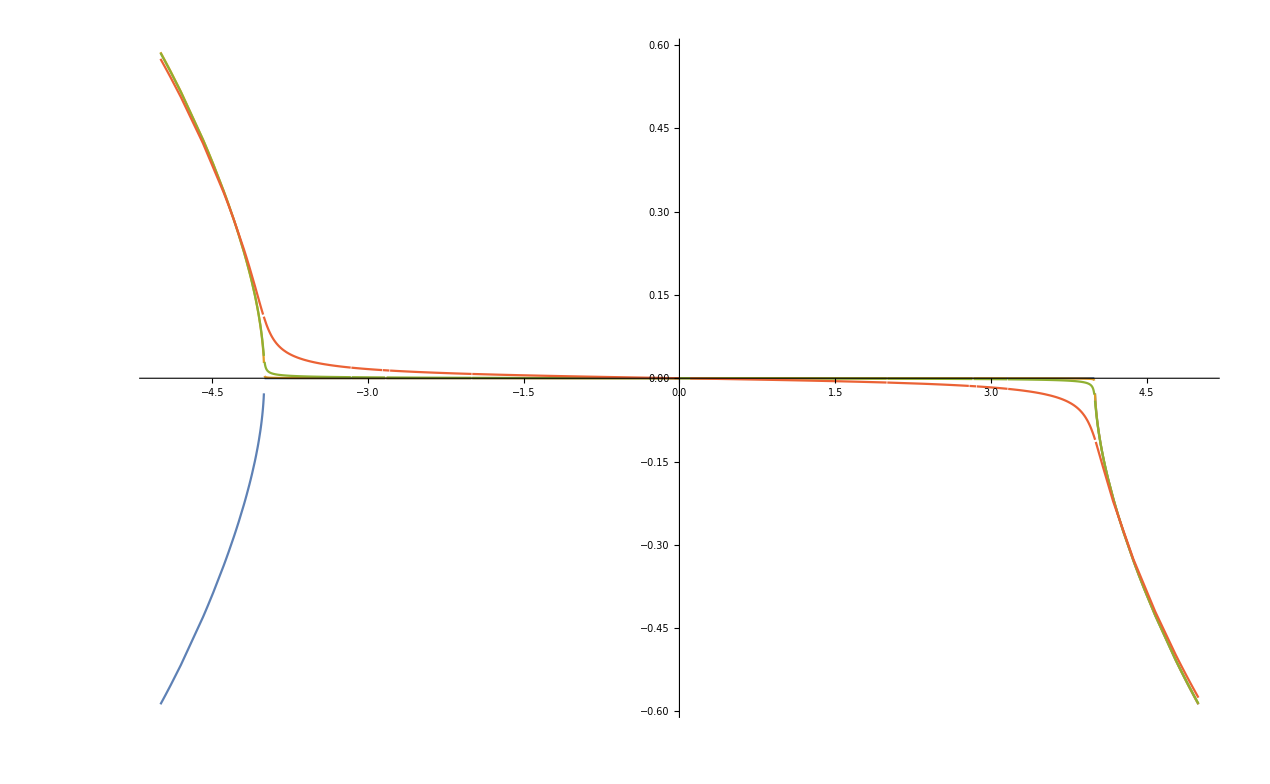

```mathematica
With[{i=2,λ1=1,λ2=3,ε=10^Range[-3,-1]},Plot[{(*Re[Fcont[w,λ1,λ2][[i]]],Re[F[-I(w+I*#),λ1,λ2][[i]]],*)Im[Fcont[w,λ1,λ2][[i]]],Evaluate[Im[F[-I(w+I*#),λ1,λ2][[i]]]&/@ε]},{w,-5,5},WorkingPrecision->100,PlotRange->All]]
```

```mathematica
Table[{p,With[{λ1=1,λ2=2},NIntegrate[x^2*Log[Δ[λ1^2,λ2^2,p^2,x]],{x,0,1}]-F2[p,λ1,λ2]]},{p,Range[1,10]}]
```

{{1,-3.55271×10^-14+0. ⅈ},{2,-1.85096×10^-12+0. ⅈ},{3,-3.43036×10^-11+0. ⅈ},{4,-1.74022×10^-12+0. ⅈ},{5,-7.65293×10^-12+0. ⅈ},{6,-2.72765×10^-11+0. ⅈ},{7,-6.27573×10^-11+0. ⅈ},{8,-1.12767×10^-10+0. ⅈ},{9,-1.68771×10^-10+0. ⅈ},{10,-2.24447×10^-10+0. ⅈ}}

Numerical and analytical integration results coincide!

```mathematica
f0cont[w_,λ1_]:=f0[-I*w,λ1]-2I*(w^2-λ1^2)/w^2*ArcTan[-w^2+λ1^2,0]
f1cont[w_,λ1_]:=f1[-I*w,λ1]-I*(w^4-λ1^4)/w^4*ArcTan[-w^2+λ1^2,0]
f2cont[w_,λ1_]:=f2[-I*w,λ1]-2I/3*(w^6-λ1^6)/w^6*ArcTan[-w^2+λ1^2,0]
f3cont[w_,λ1_]:=f3[-I*w,λ1]-I/2*(w^8-λ1^8)/w^8*ArcTan[-w^2+λ1^2,0]
f4cont[w_,λ1_]:=f4[-I*w,λ1]-2I/5*(w^10-λ1^10)/w^10*ArcTan[-w^2+λ1^2,0]
fcont[w_,λ1_]:={f0cont[w,λ1],f1cont[w,λ1],f2cont[w,λ1],f3cont[w,λ1],f4cont[w,λ1]}
```

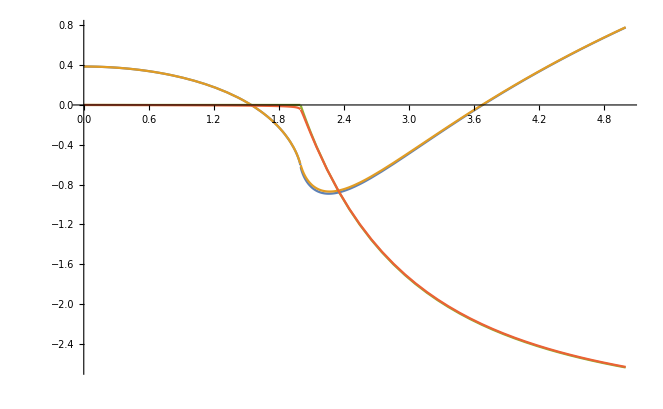

```mathematica
With[{i=1,λ1=2,λ2=3,ε=10^-2},Plot[{Re[fcont[w,λ1][[i]]],Re[f[-I(w+I*ε),λ1][[i]]],Im[fcont[w,λ1][[i]]],Im[f[-I(w+I*ε),λ1][[i]]]},{w,0,5},WorkingPrecision->100]]
```

```mathematica
g0cont[w_,λ2_]:=g0[-I*w,λ2]
g1cont[w_,λ2_]:=g1[-I*w,λ2]
g2cont[w_,λ2_]:=g2[-I*w,λ2]
g3cont[w_,λ2_]:=g3[-I*w,λ2]
g4cont[w_,λ2_]:=g4[-I*w,λ2]
gcont[w_,λ2_]:={g0cont[w,λ2],g1cont[w,λ2],g2cont[w,λ2],g3cont[w,λ2],g4cont[w,λ2]}
```

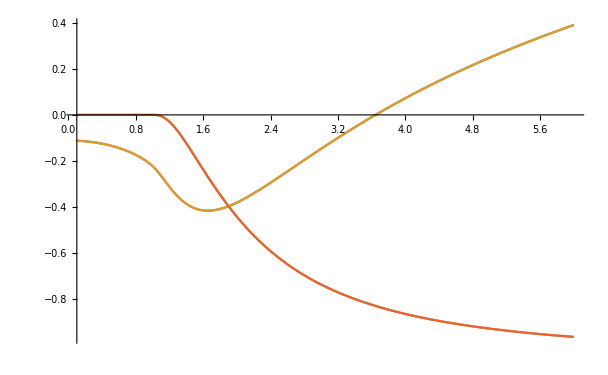

```mathematica
With[{i=3,λ1=1,λ2=3,ε=10^-4},Plot[{Re[gcont[w,λ1][[i]]],Re[g[-I(w+I*ε),λ1][[i]]],Im[gcont[w,λ1][[i]]],Im[g[-I(w+I*ε),λ1][[i]]]},{w,0.1,6}]]
```

```mathematica
h0cont[w_]:=h0[-I*w]
h1cont[w_]:=h1[-I*w]-2*I*ArcTan[0,w]
h2cont[w_]:=h2[-I*w]-4I/3*ArcTan[0,w]
h3cont[w_]:=h3[-I*w]
h4cont[w_]:=h4[-I*w]
hcont[w_]:={h0cont[w],h1cont[w],h2cont[w],h3cont[w],h4cont[w]}
```

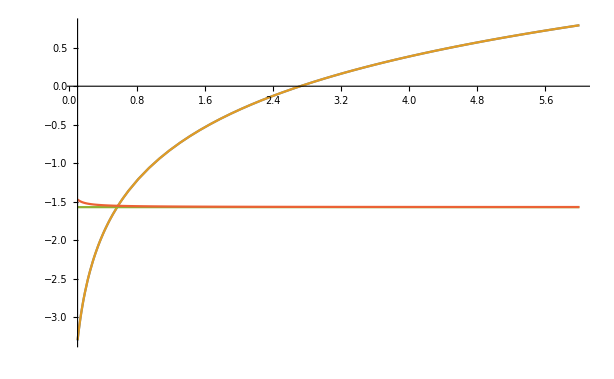

```mathematica
With[{i=2,λ1=1,λ2=3,ε=10^-2},Plot[{Re[hcont[w][[i]]],Re[h[-I(w+I*ε)][[i]]],Im[hcont[w][[i]]],Im[h[-I(w+I*ε)][[i]]]},{w,0.1,6}]]
```

#### Complete diagram (without spectral integrals)

```mathematica
gluonPolContLandauE[p_,gbar_,λ1_,λ2_,μ_]:=(24 gbar^2)/(4π)^2 Sum[Log[4π*μ^2Exp[-EulerGamma]]*(α[p,λ1,λ2][[i]]+δ[p,λ1,λ2][[i]]-β[p,λ1,λ2][[i]]-γ[p,λ1,λ2][[i]])/i-α[p,λ1,λ2][[i]]*F[p,λ1,λ2][[i]]-δ[p,λ1,λ2][[i]]*h[p][[i]]+γ[p,λ1,λ2][[i]]*f[p,λ1][[i]]+β[p,λ1,λ2][[i]]*g[p,λ2][[i]],{i,5}]
gluonPolContLandau[w_,g_,λ1_,λ2_,μ_]:=(24 g^2)/(4π)^2 Sum[Log[4π*μ^2Exp[-EulerGamma]]*(α[-I*w,λ1,λ2][[i]]+δ[-I*w,λ1,λ2][[i]]-β[-I*w,λ1,λ2][[i]]-γ[-I*w,λ1,λ2][[i]])/i-α[-I*w,λ1,λ2][[i]]*Fcont[w,λ1,λ2][[i]]-δ[-I*w,λ1,λ2][[i]]*hcont[w][[i]]+γ[-I*w,λ1,λ2][[i]]*fcont[w,λ1][[i]]+β[-I*w,λ1,λ2][[i]]*gcont[w,λ2][[i]],{i,5}]
DgluonPolContLandauE[p_,g_,λ1_,λ2_,μ_]:=Evaluate[D[gluonPolContLandauE[p,g,λ1,λ2,μ],p]]
```

Test contribution to anomalous dimension (the coefficient of w^2 should be -25/12)

```mathematica
FullSimplify[Sum[(α[p,λ1,λ2][[i]]-γ[p,λ1,λ2][[i]]-β[p,λ1,λ2][[i]]+δ[p,λ1,λ2][[i]])/(3i),{i,5}]]/.{λ1->0,λ2->0}
```

(25 p^2)/12

### Discretization & Interpolation

#### Discretization

The discretized functions are stored in realtime_gluon _spectral _function _data.mx and do not need to be computed during initialization to run the notebook.

```mathematica
wRange=10^Range[-400/99,2,10^-1];
λRange=10^Range[-(400/101),2,10^-1];
```

```mathematica
gluPolμ2TblE={};
DgluPolμ0TblE={};
```

```mathematica
Do[
Do[
AppendTo[gluPolμ0TblE,{{λRange[[j]],λRange[[k]]},N[With[{μ=1/1000,g=1},gluonPolContLandauE[μ,g,λRange[[j]],λRange[[k]],μ]],30]}];
, {k,Length[λRange]}]
, {j, Length[λRange]}]
```

```mathematica
{r,{DgluPolμ2TblE}}=Reap[
Do[
Do[
Sow[{{λRange[[j]],λRange[[k]]},With[{μ=2,g=1},N[DgluonPolContLandauE[μ,g,λRange[[j]],λRange[[k]],μ],30]]}];
, {k,Length[λRange]}]
, {j, Length[λRange]}]
];
```

```mathematica
gluPolTbl={};
```

```mathematica
Do[
Do[
Do[
AppendTo[gluPolTbl,{{wRange[[i]],λRange[[j]],λRange[[k]]},N[gluonPolContLandau[wRange[[i]],1,λRange[[j]],λRange[[k]],2],30]}];
, {k,Length[λRange]}]
, {j, Length[λRange]}]
, {i, Length[wRange]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 («29»+«1»+«1»+1/2 (3/(400000000000000000000000000 10^(181/505))+(3 (-1/1000000000000000000000000+«4»))/(400 10^(181/505))-(3 (-1/(1«6»00)+100 «1») (-1/100000000+500 Power[«2»]))/(40000000000 10^(181/505))-(3 (-1/1000000000000000000000000+9 Power[«2»]+Plus[«2»]/10000000000000000+Plus[«3»]/100000000))/(400 10^(181/505))) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 («30»+«1»+1/2 (3/(400000000000000000000000000 10^(181/505))+(3 (-1/1000000000000000000000000-(7 «1»)/(1000«8»0000)+(3«1»«1»)/(«7»0)+9 Power[«2»]))/(400 10^(181/505))-(3 (-1/(10«4»000)+100 «1») («1»))/(40000000000 10^(181/«3»))-(3 (-1/1000000000000000000000000+Plus[«2»]/10000000000000000+9 Power[«2»]+Plus[«3»]/100000000))/(400 10^(181/505))) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 ((3 (-(2 ⅈ π)/3+1/18 (-13+6 Plus[«2»])))/(400000000000000000000000000 10^(181/505))-(3 (-ⅈ π+1/2 («1»)))/(40000000«11»00000000«1»«1»)+«27»+«1»+1/3 (-3/(400000000000000000000000000 10^(181/505))-(3 (-1/500000000000000000000000+(79 «1»)/(1«11»00)-«1»+9000000 Power[«2»]))/(800 10^(181/505))-(3 («1»))/(800 10^(181/505))+(3 (-1/500000000000000000000000+Plus[«2»]/10000000000000000+9 Power[«2»] Plus[«2»]+Plus[«3»]/100000000))/(800 10^(181/505))) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
gluPolTblE={};
```

```mathematica
Do[
Do[
Do[
AppendTo[gluPolTblE,{{wRange[[i]],λRange[[j]],λRange[[k]]},N[gluonPolContLandauE[wRange[[i]],1,λRange[[j]],λRange[[k]],2],30]}];
, {k,Length[λRange]}]
, {j, Length[λRange]}]
, {i, Length[wRange]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 (-(-13-6 Log[100000000])/(240000000000000000 10^(282/505))+«26»+1/3 (3/(40000000000000000 10^(282/505))-3750000 10^(223/505) (1/500000000000000000000000-(11 Power[«2»])/100000000000000000000000-(29 Power[«2»])/50000000000000000000000+(9 Power[«2»])/100000000000000000000000)-3750000 10^(«1») («1»)+3750000 10^(223/505) (1/500000000000000000000000+9 Power[«2»] Plus[«2»]+Plus[«2»]/10000000000000000+Plus[«3»]/100000000)) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 (-(-13-6 Log[100000000])/(240000000000000000 10^(383/505))+«26»+1/3 (3/(40000000000000000 10^(383/505))-3750000 10^(122/505) (1/500000000000000000000000-(11 Power[«2»])/100000000000000000000000-(29 Power[«2»])/50000000000000000000000+(9 Power[«2»])/100000000000000000000000)-3750000 10^(«1») («1»)+3750000 10^(122/505) (1/500000000000000000000000+Plus[«3»]/100000000+9 Power[«2»] Plus[«2»]+Plus[«2»]/10000000000000000)) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 (-(-13-6 Log[100000000])/(240000000000000000 10^(484/505))+«26»+1/3 (3/(40000000000000000 10^(484/505))-3750000 10^(21/505) (1/500000000000000000000000-(11 Power[«2»])/100000000000000000000000-(29 Power[«2»])/50000000000000000000000+(9 Power[«2»])/100000000000000000000000)-«1»+3750000 10^(21/505) (1/500000000000000000000000+Plus[«3»]/100000000+9 Power[«2»] Plus[«2»]+Plus[«2»]/10000000000000000)) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

#### Interpolation

```mathematica
(*gluPolIntPol=Interpolation[gluPolTbl,Method->"Spline"];
gluPolIntPolE=Interpolation[gluPolTblE,Method->"Spline"];
gluPolμ2IntPolE=Interpolation[gluPolμ2TblE,Method->"Spline"];*)
(*DgluPolμ2IntPolE=Interpolation[DgluPolμ2TblE,Method->"Spline"];*)
(*DgluPolμ0IntPolE=Interpolation[DgluPolμ0TblE,Method->"Spline"];*)
```

### Spectral regularization

```mathematica
gluPolRegIntPol[w_,αs_,λ1_,λ2_,specFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*(gluPolIntPol[w,λ1,λ2]-gluPolIntPolE[μ,λ1,λ2]+(w^2+μ^2)/(2μ)*DgluPolμ2IntPolE[λ1,λ2])]
gluPolRegIntPolE[p_,αs_,λ1_,λ2_,specFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*(gluPolIntPolE[p,λ1,λ2]-gluPolIntPolE[μ,λ1,λ2]-(p^2-μ^2)/(2μ)*DgluPolμ2IntPolE[λ1,λ2])]
```

### Checks

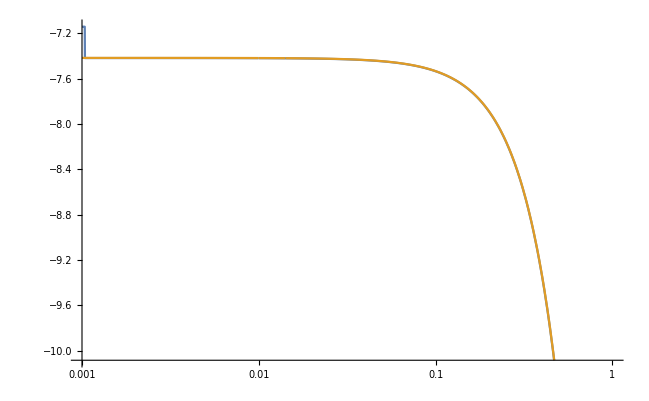

```mathematica
With[{λ1=10^-2,λ2=1,αs=22/100,μ=2,ε=10^-2},LogLinearPlot[{Re[gluonPolContLandau[w,Sqrt[4π*αs],λ1,λ2,μ]],Re[gluonPolContLandauE[-I(w+I*ε),Sqrt[4π*αs],λ1,λ2,μ]]},{w,10^-3,1},WorkingPrecision->30]]
```

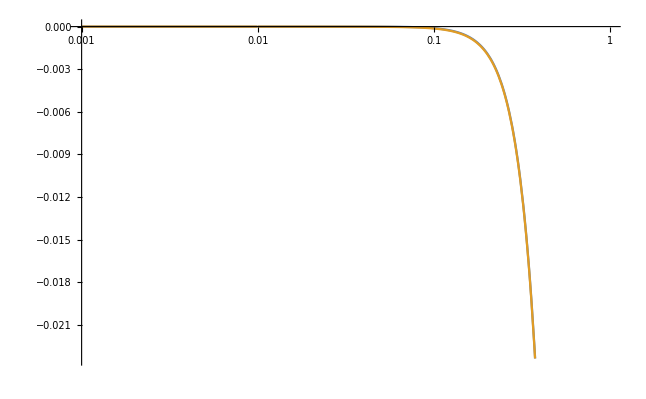

```mathematica
With[{λ1=10^-2,λ2=1,αs=22/100,μ=2,ε=10^-5},LogLinearPlot[{Im[gluonPolContLandau[w,Sqrt[4π*αs],λ1,λ2,μ]],Im[gluonPolContLandauE[-I(w+I*ε),Sqrt[4π*αs],λ1,λ2,μ]]},{w,10^-3,1},WorkingPrecision->30]]
```

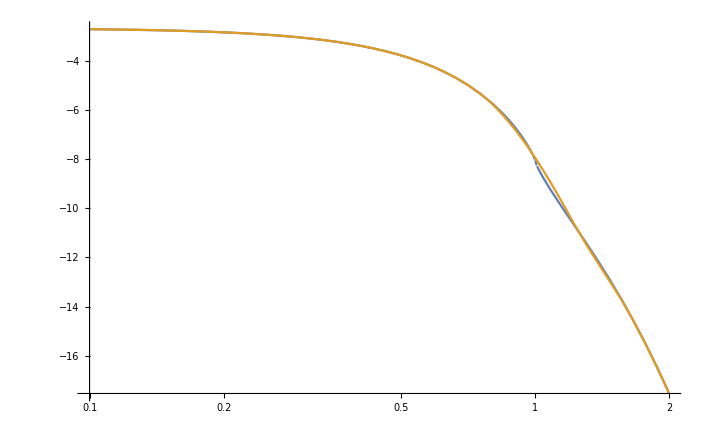

```mathematica
With[{λ1=1,λ2=10^-2,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{Re[gluonPolContLandau[w,g,λ1,λ2,μ]],Re[gluPolIntPol[w,λ1,λ2]]},{w,10^-1,2},WorkingPrecision->30]]
```

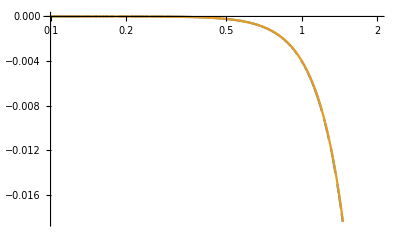

```mathematica
With[{λ1=10^-1,λ2=10,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{Im[gluonPolContLandau[w,g,λ1,λ2,μ]],Im[gluPolIntPol[w,λ1,λ2]]},{w,10^-1,2},WorkingPrecision->30]]
```

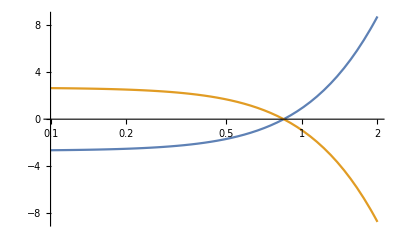

```mathematica
With[{λ1=1,λ2=10^-2,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{gluonPolContLandauE[w,g,λ1,λ2,μ],-gluPolIntPolE[w,λ1,λ2]},{w,10^-1,2},WorkingPrecision->30]]
```

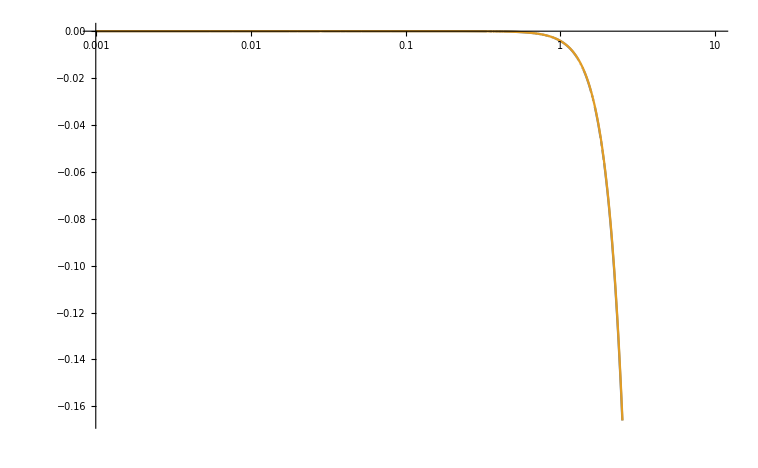

```mathematica
With[{λ1=10^-2,λ2=10^1,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{Im[gluonPolContLandau[w,g,λ1,λ2,μ]],Im[gluPolIntPol[w,λ1,λ2]]},{w,10^-3,10},WorkingPrecision->30]]
```

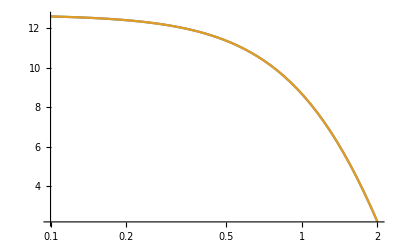

```mathematica
With[{λ1=10^-1,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{gluonPolContLandauE[μ,g,λ1,λ2,μ],gluPolμ2IntPolE[λ1,λ2]},{λ2,10^-1,2},WorkingPrecision->30]]
```

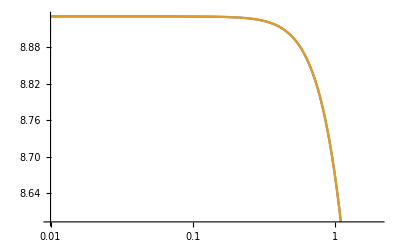

```mathematica
With[{λ2=10^-2,g=1,μ=2,ε=10^Range[-4,-1]},LogLinearPlot[{DgluonPolContLandauE[μ,g,λ1,λ2,μ],DgluPolμ2IntPolE[λ1,λ2]},{λ1,10^-2,2},WorkingPrecision->30]]
```

## Ghost diagram

### Function definitions

#### Euclidean

```mathematica
ghostInt=Integrate[Δ[λ1^2,λ2^2,p^2,x]*Log[Δ[λ1^2,λ2^2,p^2,x]],x]
```

-1/(36 p^4)(6 (p^4+(λ1^2-λ2^2)^2+2 p^2 (λ1^2+λ2^2))^(3/2) ArcTanh[(p^2 (1-2 x)-λ1^2+λ2^2)/(√(p^4+(λ1^2-λ2^2)^2+2 p^2 (λ1^2+λ2^2)))]+3 (p^6-(λ1^2-λ2^2)^3+3 p^4 (λ1^2+λ2^2)-3 p^2 (λ1^4-λ2^4)) Log[p^2 (-1+x) x+(-1+x) λ1^2-x λ2^2]+2 p^2 x (p^4 (3+6 x-4 x^2)+3 (λ1^2-λ2^2)^2+6 p^2 (-(-3+x) λ1^2+(1+x) λ2^2)+3 p^2 (p^2 x (-3+2 x)+3 (-2+x) λ1^2-3 x λ2^2) Log[-p^2 (-1+x) x-(-1+x) λ1^2+x λ2^2]))

```mathematica
fG[p_,λ1_,λ2_]:=1/36 (-10 p^2-(6 (λ1^2-λ2^2)^2)/p^2-24 (λ1^2+λ2^2)-(6 (-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2))^(3/2) ArcTan[(p^2+λ1^2-λ2^2)/(√(-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2)))])/p^4+1/p^4 3 (-2 (-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2))^(3/2) ArcTan[(p^2-λ1^2+λ2^2)/(√(-(p^2+(λ1-λ2)^2) (p^2+(λ1+λ2)^2)))]+(p^2-λ1^2+λ2^2) (p^4+(λ1^2-λ2^2)^2+2 p^2 (2 λ1^2+λ2^2)) Log[-λ1^2])-(3 (p^2-λ1^2+λ2^2) (p^4+(λ1^2-λ2^2)^2+2 p^2 (2 λ1^2+λ2^2)) Log[-λ2^2])/p^4+6 (p^2+3 (λ1^2+λ2^2)) Log[λ2^2])
fGCont[w_,λ1_,λ2_]:=fG[-I*w,λ1,λ2]
```

#### Real - time

#### Complete diagram

The factor of -1 from the fermionic loop has been taken care of when computing the diagram. This means we need to multiply the DSE factor of the ghost diagram by -1.

```mathematica
ghostPol[p_,g_,λ1_,λ2_,μ_]:=(3*24 g^2)/(4π)^2((1/12p^2+1/4(λ1^2+λ2^2))Log[4π*μ^2*Exp[-EulerGamma]]-1/2fG[p,λ1,λ2])
ghostPolCont[w_,g_,λ1_,λ2_,μ_]:=(3*24 g^2)/(4π)^2((-1/12w^2+1/4(λ1^2+λ2^2))Log[4π*μ^2*Exp[-EulerGamma]]-1/2fGCont[w,λ1,λ2])
DghostPol[p_,g_,λ1_,λ2_,μ_]:=Evaluate[D[ghostPol[p,g,λ1,λ2,μ],p]]
```

#### Checks

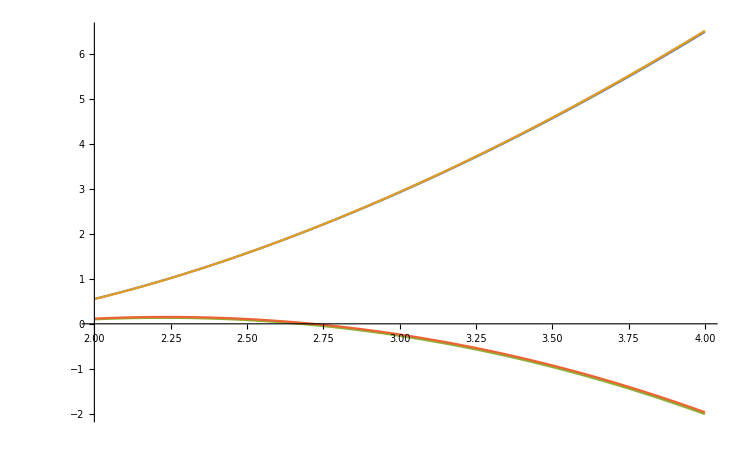

```mathematica
With[{λ1=1,λ2=1/2,ε=10^-2},Plot[{Im[fG[-I(w+I*ε),λ1,λ2]],Im[fGCont[w,λ1,λ2]],Re[fG[-I(w+I*ε),λ1,λ2]],Re[fGCont[w,λ1,λ2]]},{w,2,4},WorkingPrecision->30]]
```

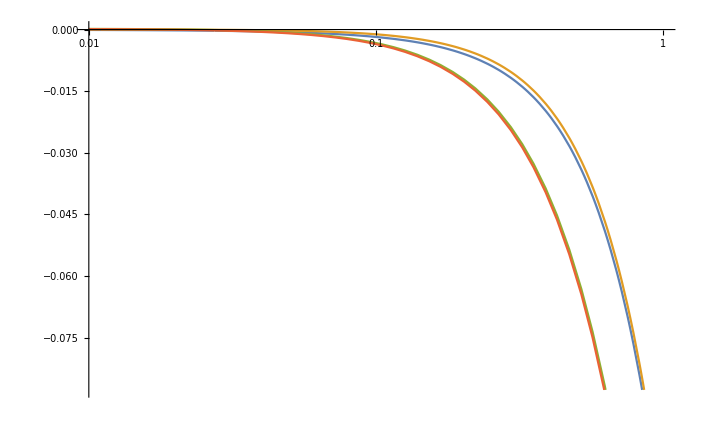

```mathematica
With[{λ1=10^-2,λ2=10^-3,ε=10^-2,g=1,μ=2},LogLinearPlot[{Im[ghostPol[-I(w+I*ε),g,λ1,λ2,μ]],Im[ghostPolCont[w,g,λ1,λ2,μ]],Re[ghostPol[-I(w+I*ε),g,λ1,λ2,μ]],Re[ghostPolCont[w,g,λ1,λ2,μ]]},{w,10^-2,10^0}]]
```

### Discretization & Interpolation

#### Discretization

```mathematica
ghostPolTbl={};
ghostPolTblμ2E={};
DghostPolTblμ2E={};
```

```mathematica
ghostPolTblE={};
```

```mathematica
ghostPolTblESubtr1=tmpTbl;
```

The discretized functions are stored in realtime_gluon _spectral _function _data.mx and do not need to be computed during initialization to run the notebook.

```mathematica
Do[
Do[
Do[

tempRes=With[{g=1,μ=2},N[ghostPolCont[wRange[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[j==1,

tempResLim1=With[{g=1,μ=2},N[ghostPolCont[wRange[[i]],g,10^-6,λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPolCont[wRange[[i]],g,λRangeGhostGlu[[j]],10^-6,μ],30]];
tempResLim12=With[{g=1,μ=2},N[ghostPolCont[wRange[[i]],g,10^-6,10^-6,μ],30]];

AppendTo[
ghostPolTbl,{{wRange[[i]],0,0},tempResLim12}
];
AppendTo[
ghostPolTbl,{{wRange[[i]],0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTbl,{{wRange[[i]],0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

],

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPolCont[wRange[[i]],g,λRangeGhostGlu[[j]],10^-6,μ],30]];

AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTbl,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

]
];

Clear[tempRes,tempResLim1,tempResLim2,tempResLim12];

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
, {i, Length[wRange]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (9 («1»))/(4 π^2).

```mathematica
tmpTbl={};
```

```mathematica
λRange2=Join[10^Range[-50/11,2,1/40],10^Range[2,4,1/80]];
```

```mathematica
61*(Length[λRange2](*+Length[λRange2]*))*1.8/3600//N
```

12.9015

```mathematica
prec=30;
```

```mathematica
Block[{$MaxExtraPrecision=1000},
AbsoluteTiming[{r,{tmpList}}=Reap[

Do[

(*Print[i];*)
Which[i==6,Print["10% finished"],i==12,Print["20% finished"],i==18,Print["30% finished"],i==24,Print["40% finished"],i==30,Print["50% finished"],i==36,Print["60% finished"],i==42,Print["70% finished"],i==48,Print["80% finished"],i==54,Print["90% finished"]];

Do[
(*iterTime=AbsoluteTiming[*)
Do[

Sow[tempRes=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRange2[[j]],λRange2[[k]],μ]-ghostPol[μ,g,λRange2[[j]],λRange2[[k]],μ],prec]]];

If[j==1,

Sow[tempResLim1=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,10^-7,λRange2[[k]],μ]-ghostPol[μ,g,10^-7,λRange2[[k]],μ],prec]]];

If[k==1,

Sow[tempResLim12=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,10^-7,10^-7,μ]-ghostPol[μ,g,10^-7,10^-7,μ],prec]]];
Sow[tempResLim2=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRange2[[j]],10^-7,μ]-ghostPol[μ,g,λRange2[[j]],10^-7,μ],prec]]];
(*AppendTo[
tmpTbl,{{wRange[[i]],0,0},tempResLim12}
];
AppendTo[
tmpTbl,{{wRange[[i]],0,λRange2[[k]]},tempResLim1}
];
AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],0},tempResLim2}
];
AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],λRange2[[k]]},tempRes}
];*),

Null
(*AppendTo[
tmpTbl,{{wRange[[i]],0,λRange2[[k]]},tempResLim1}
];
AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],λRange2[[k]]},tempRes}
];*)

],

If[k==1,

Sow[tempResLim2=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRange2[[j]],10^-7,μ]-ghostPol[μ,g,λRange2[[j]],10^-7,μ],prec]]];

(*AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],0},tempResLim2}
];
AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],λRange2[[k]]},tempRes}
];*),

(*AppendTo[
tmpTbl,{{wRange[[i]],λRange2[[j]],λRange2[[k]]},tempRes}
];*)
Null
]
];

, {k,Length[λRange2]}]
(*][[1]];*)
(*Print[iterTime];*)
, {j, Length[λRange2]}]
, {i, Length[wRange]}]
];
]]
```

10% finished

$Aborted

```mathematica
Do[
Do[
Do[

tempRes=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[j==1,

tempResLim1=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,10^-6,λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRangeGhostGlu[[j]],10^-6,μ],30]];
tempResLim12=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,10^-6,10^-6,μ],30]];

AppendTo[
ghostPolTblE,{{wRange[[i]],0,0},tempResLim12}
];
AppendTo[
ghostPolTblE,{{wRange[[i]],0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTblE,{{wRange[[i]],0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

],

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPol[wRange[[i]],g,λRangeGhostGlu[[j]],10^-6,μ],30]];

AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTblE,{{wRange[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

]
];

Clear[tempRes,tempResLim1,tempResLim2,tempResLim12];

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
, {i, Length[wRange]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (9 («1»))/(4 π^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
Do[
Do[

tempRes=With[{g=1,μ=2},N[ghostPol[μ,g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[j==1,

tempResLim1=With[{g=1,μ=2},N[ghostPol[μ,g,10^-6,λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPol[μ,g,λRangeGhostGlu[[j]],10^-6,μ],30]];
tempResLim12=With[{g=1,μ=2},N[ghostPol[μ,g,10^-6,10^-6,μ],30]];

AppendTo[
ghostPolTblμ2E,{{0,0},tempResLim12}
];
AppendTo[
ghostPolTblμ2E,{{0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTblμ2E,{{0,λRangeGhostGlu[[k]]},tempResLim1}
];
AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

],

If[k==1,

tempResLim2=With[{g=1,μ=2},N[ghostPol[μ,g,λRangeGhostGlu[[j]],10^-6,μ],30]];

AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],0},tempResLim2}
];
AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostPolTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];

]
];

Clear[tempRes,tempResLim1,tempResLim2,tempResLim12];

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
```

```mathematica
{r,{DghostPolμ2TblE}}=Reap[
Do[
Do[
Sow[{{λRange[[j]],λRange[[k]]},tempRes=With[{μ=2,g=1},N[DghostPol[μ,g,λRange[[j]],λRange[[k]],μ],30]]}];
, {k,Length[λRange]}]
, {j, Length[λRange]}]
];
```

#### Interpolation

```mathematica
(*ghostPolIntPol=Interpolation[ghostPolTbl];
ghostPolIntPolE=Interpolation[ghostPolTblE,Method->"Spline"];
ghostPolIntPolESubtr1=Interpolation[ghostPolTblESubtr1,Method->"Spline"];
ghostPolμ2IntPolE=Interpolation[ghostPolTblμ2E,Method->"Spline"];*)
(*DghostPolμ2IntPolE=Interpolation[DghostPolμ2TblE,Method->"Spline"];*)
(*DghostPolμ0IntPolE=Interpolation[DghostPolμ0TblE,Method->"Spline"];*)
```

### Spectral regularization

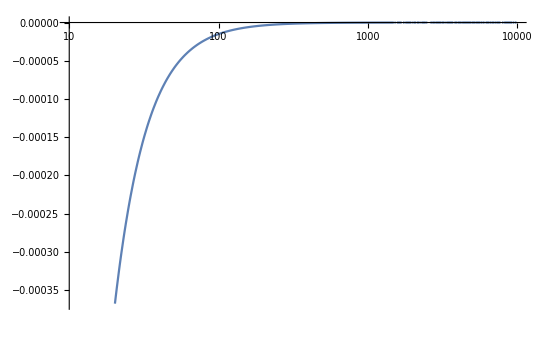

```mathematica
With[{μ=2,g=1,λ2=10^-2,w=1/10},LogLinearPlot[{Re[ghostPol[w,g,λ1,λ2,μ]-ghostPol[μ,g,λ1,λ2,μ]+(-w^2+μ^2)/(2μ)*DghostPol[μ,g,λ1,λ2,μ]]},{λ1,10^1,10^4},WorkingPrecision->100]]
```

```mathematica
ghostPolRegIntPol[w_,αs_,λ1_,λ2_,specFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*(ghostPolIntPol[w,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]+(w^2+μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
ghostPolReg0[αs_,λ1_,λ2_,specFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*ghostPolIntPolE[μ,λ1,λ2]]
ghostPolReg1[αs_,λ1_,λ2_,specFunc_]:=4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*DghostPolμ2IntPolE[λ1,λ2]
ghostPolRegIntPolE[p_,αs_,λ1_,λ2_,specFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*specFunc[λ1]*specFunc[λ2]*(ghostPolIntPolE[p,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]-(p^2-μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
ghostPolRegIntPolPole[w_,αs_,λ1_,specFunc_]:=With[{μ=2,λ2=10^-4},4π*αs*λ1/π*specFunc[λ1]*(ghostPolIntPol[w,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]+(w^2+μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
ghostPolRegIntPolPoleE[p_,αs_,λ1_,specFunc_]:=With[{μ=2,λ2=10^-4},4π*αs*λ1/π*specFunc[λ1]*(ghostPolIntPolE[p,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]-(p^2-μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
ghostPolRegIntPolPolePole[w_,αs_]:=With[{μ=2,λ1=λ2=10^-4},4π*αs*(ghostPolIntPol[w,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]+(w^2+μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
ghostPolRegIntPolPolePoleE[p_,αs_]:=With[{μ=2,λ1=λ2=10^-4},4π*αs*(ghostPolIntPolE[p,λ1,λ2]-ghostPolIntPolE[μ,λ1,λ2]-(p^2-μ^2)/(2μ)*DghostPolμ2IntPolE[λ1,λ2])]
```

#### Checks

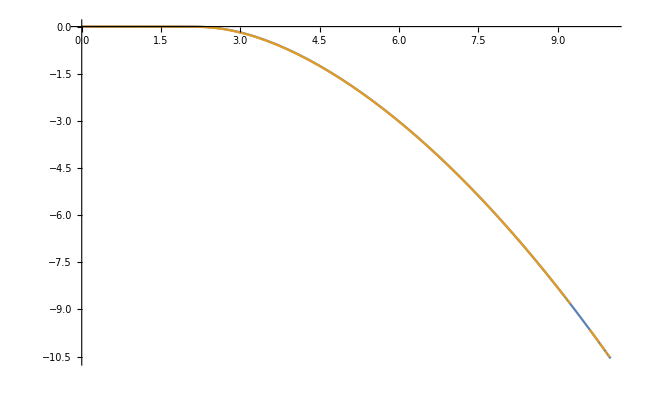

```mathematica
With[{αs=22/100,mc=10^-6,μ=2,ε=10^-2},Plot[{Im[ghostPolCont[w,1,mc,μ,μ]],Im[ghostPol[-I(w+I*ε),1,mc,μ,μ]]},{w,10^-3,10^1},WorkingPrecision->30]]
```

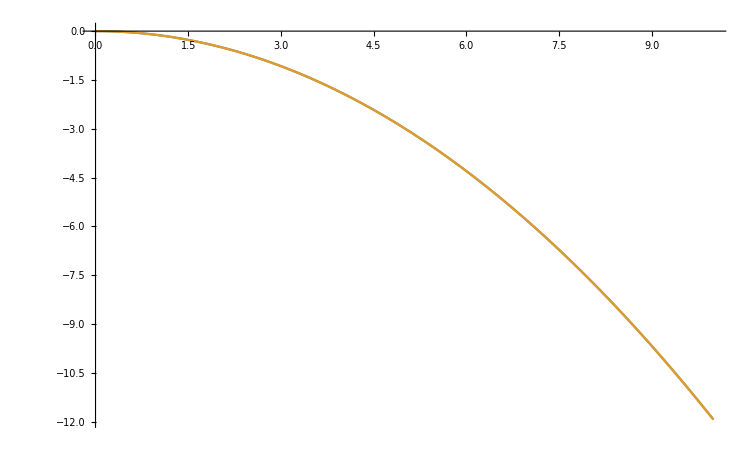

```mathematica
With[{αs=22/100,mc=10^-6,μ=2},Plot[{Im[ghostPolCont[w,1,mc,mc,μ]],Im[ghostPolIntPol[w,mc,mc]]},{w,10^-3,10^1},WorkingPrecision->30]]
```

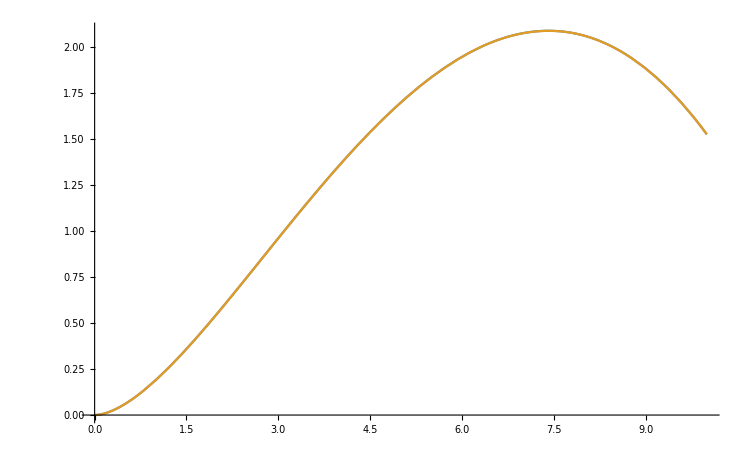

```mathematica
With[{αs=22/100,mc=10^-6,μ=2},Plot[{ghostPol[w,1,mc,mc,μ],ghostPolIntPolE[w,mc,mc]},{w,10^-3,10^1},WorkingPrecision->30]]
```

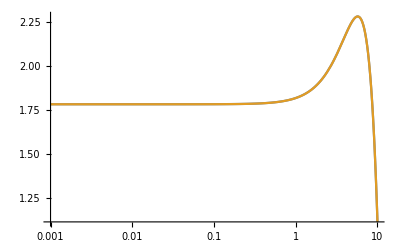

```mathematica
With[{αs=22/100,mc=10^-6,μ=2},LogLinearPlot[{ghostPol[w,1,μ,μ,μ],ghostPolIntPolE[w,μ,μ]},{w,10^-3,10^1},WorkingPrecision->30,PlotRange->All]]
```

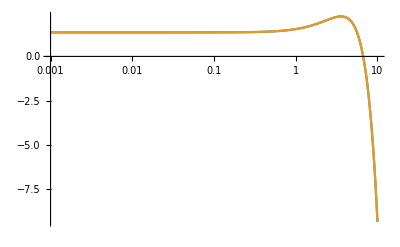

```mathematica
With[{αs=22/100,mc=10^-6,μ=2},LogLinearPlot[{ghostPol[μ,1,λ1,μ,μ],ghostPolIntPolE[μ,λ1,μ]},{λ1,10^-3,10^1},WorkingPrecision->30,PlotRange->All]]
```

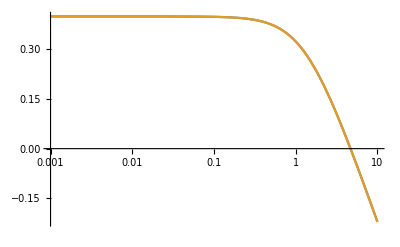

```mathematica
With[{αs=22/100,mc=10^-6,μ=2},LogLinearPlot[{DghostPol[μ,1,λ1,mc,μ],DghostPolμ2IntPolE[mc,λ1]},{λ1,10^-3,10^1},WorkingPrecision->30,PlotRange->All]]
```

## Ghost-gluon diagram (ghost propagator DSE)

### Lorentz structure

#### Defining tensors and performing contractions and projections

Vertex Lorentz structure before and after performing the shift q -> q-xp

```mathematica
Nghost[p_,q_]:=vec[p,μ](vec[p,ν]+vec[q,ν])
NghostShift[p_,q_,x_]:=vec[p,μ]((1-x)vec[p,ν]+vec[q,ν])
```

Symmetrize q^α q^ν→ 1/d*δ^αν*q^2 and contract with Lorentz structure from the propagators

```mathematica
Nghost1shift[p_,q_,x_]:=Evaluate[FormTrace[NghostShift[p,q,x]*deltaLorentz[μ,ν]]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]^2->1/4*p^2*q^2,sp[q,p]^2->1/4*p^2*q^2,sp[p,q]->0,sp[q,p]->0}]
Nghost2shift[p_,q_,x_]:=Evaluate[FormTrace[NghostShift[p,q,x]*(vec[q,μ]-x*vec[p,μ])(vec[q,ν]-x*vec[p,ν])]/.{sp[p,p]->p^2,sp[q,q]->q^2,sp[p,q]^2->1/4*p^2*q^2,sp[q,p]^2->1/4*p^2*q^2,sp[p,q]->0,sp[q,p]->0}]
```

#### Collecting coefficients for momentum integration

```mathematica
Aghost2[p_,x_,λ1_]:=Evaluate[Coefficient[(Nghost1shift[p,q,x]+λ1^-2*Nghost2shift[p,q,x]),q^4]]
Aghost1[p_,x_,λ1_]:=Evaluate[Coefficient[(Nghost1shift[p,q,x]+λ1^-2*Nghost2shift[p,q,x]),q^2]]
Aghost0[p_,x_,λ1_]:=Evaluate[(Nghost1shift[p,q,x]+λ1^-2*Nghost2shift[p,q,x])/.q->0]

Bghost2[p_,x_,λ1_]:=Evaluate[Coefficient[λ1^-2*Nghost2shift[p,q,x],q^4]]
Bghost1[p_,x_,λ1_]:=Evaluate[Coefficient[λ1^-2*Nghost2shift[p,q,x],q^2]]
Bghost0[p_,x_,λ1_]:=Evaluate[λ1^-2*Nghost2shift[p,q,x]/.q->0]

Aghost[p_,x_,λ1_]:={Aghost0[p,x,λ1],Aghost1[p,x,λ1],Aghost2[p,x,λ1]}
Bghost[p_,x_,λ1_]:={Bghost0[p,x,λ1],Bghost1[p,x,λ1],Bghost2[p,x,λ1]}
```

#### Perform momentum integration and collect coefficients for Feynman parameter integration

```mathematica
αghost0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(Aghost0[p,x,λ1]-2Aghost1[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]+3Aghost2[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]^2)/.x->0]]
αghost1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Aghost0[p,x,λ1]-2Aghost1[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]+3Aghost2[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]^2),x]]]
αghost2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Aghost0[p,x,λ1]-2Aghost1[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]+3Aghost2[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]^2),x^2]]]
αghost3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Aghost0[p,x,λ1]-2Aghost1[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]+3Aghost2[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]^2),x^3]]]
αghost4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Aghost0[p,x,λ1]-2Aghost1[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]+3Aghost2[p,x,λ1]Δ[λ1^2,λ2^2,p^2,x]^2),x^4]]]

βghost0[p_,λ1_,λ2_]:=Evaluate[FullSimplify[(Bghost0[p,x,λ1]-2Bghost1[p,x,λ1]Δ[0,λ2^2,p^2,x]+3Bghost2[p,x,λ1]Δ[0,λ2^2,p^2,x]^2)/.x->0]]
βghost1[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Bghost0[p,x,λ1]-2Bghost1[p,x,λ1]Δ[0,λ2^2,p^2,x]+3Bghost2[p,x,λ1]Δ[0,λ2^2,p^2,x]^2),x]]]
βghost2[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Bghost0[p,x,λ1]-2Bghost1[p,x,λ1]Δ[0,λ2^2,p^2,x]+3Bghost2[p,x,λ1]Δ[0,λ2^2,p^2,x]^2),x^2]]]
βghost3[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Bghost0[p,x,λ1]-2Bghost1[p,x,λ1]Δ[0,λ2^2,p^2,x]+3Bghost2[p,x,λ1]Δ[0,λ2^2,p^2,x]^2),x^3]]]
βghost4[p_,λ1_,λ2_]:=Evaluate[FullSimplify[Coefficient[(Bghost0[p,x,λ1]-2Bghost1[p,x,λ1]Δ[0,λ2^2,p^2,x]+3Bghost2[p,x,λ1]Δ[0,λ2^2,p^2,x]^2),x^4]]]

αghost[p_,λ1_,λ2_]:={αghost0[p,λ1,λ2],αghost1[p,λ1,λ2],αghost2[p,λ1,λ2],αghost3[p,λ1,λ2],αghost4[p,λ1,λ2]}
βghost[p_,λ1_,λ2_]:={βghost0[p,λ1,λ2],βghost1[p,λ1,λ2],βghost2[p,λ1,λ2],βghost3[p,λ1,λ2],βghost4[p,λ1,λ2]}
```

```mathematica
FullSimplify[Sum[(αghost[-I*w,λ1,λ2][[i]]-βghost[-I*w,λ1,λ2][[i]])/i,{i,5}]](*/.{λ1->0,λ2->0}*)
```

-(3 w^2)/4

### Function definitions

Dimensionless functions appearing after momentum and Feynman parameter integration.
The appearing functions are identical to those of the gluon polarization diagram.

#### Complete diagram

```mathematica
ghostGluLoopLandau[p_,gbar_,λ1_,λ2_,μ_]:=(24gbar^2)/(4π)^2 Sum[Log[4π*μ^2Exp[-EulerGamma]]*(αghost[p,λ1,λ2][[i]]-βghost[p,λ1,λ2][[i]])/i-αghost[p,λ1,λ2][[i]]*F[p,λ1,λ2][[i]]+βghost[p,λ1,λ2][[i]]*g[p,λ2][[i]],{i,4}]
ghostGluLoopContLandau[w_,g_,λ1_,λ2_,μ_]:=(24g^2)/(4π)^2 Sum[Log[4π*μ^2Exp[-EulerGamma]]*(αghost[-I*w,λ1,λ2][[i]]-βghost[-I*w,λ1,λ2][[i]])/i-αghost[-I*w,λ1,λ2][[i]]*Fcont[w,λ1,λ2][[i]]+βghost[-I*w,λ1,λ2][[i]]*gcont[w,λ2][[i]],{i,4}]
DghostGluLoopLandau[p_,gbar_,λ1_,λ2_,μ_]:=Evaluate[D[ghostGluLoopLandau[p,gbar,λ1,λ2,μ],p]]
```

Check if anomalous dimension is in line with PT (should be -3/4):

```mathematica
FullSimplify[Sum[(αghost[p,λ1,λ2][[i]]-βghost[p,λ1,λ2][[i]])/i,{i,5}]]/.{λ1->0,λ2->0,p->ⅈ*ω}
```

-(3 ω^2)/4

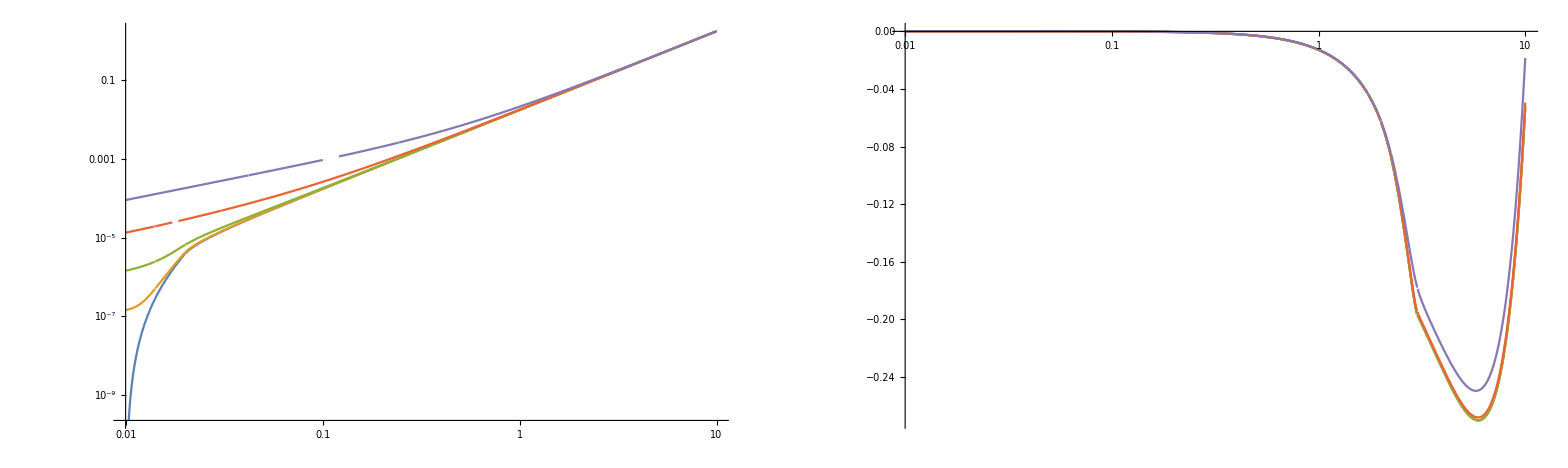

```mathematica
With[{ε=10^Range[-4,-1]},GraphicsRow[{LogLogPlot[{-Im[ghostGluLoopContLandau[ω,22/100,10^-2,10^-2,2]],Evaluate[-Im[ghostGluLoopLandau[-I(ω+I*#),22/100,10^-2,10^-2,2]]&/@ε]},{ω,10^-2,10^1},WorkingPrecision->30],LogLinearPlot[{Re[ghostGluLoopContLandau[ω,22/100,1,2,2]],Evaluate[Re[ghostGluLoopLandau[-I(ω+I*#),22/100,1,2,2]]&/@ε]},{ω,10^-2,10^1},WorkingPrecision->30]},ImageSize->1600]]
```

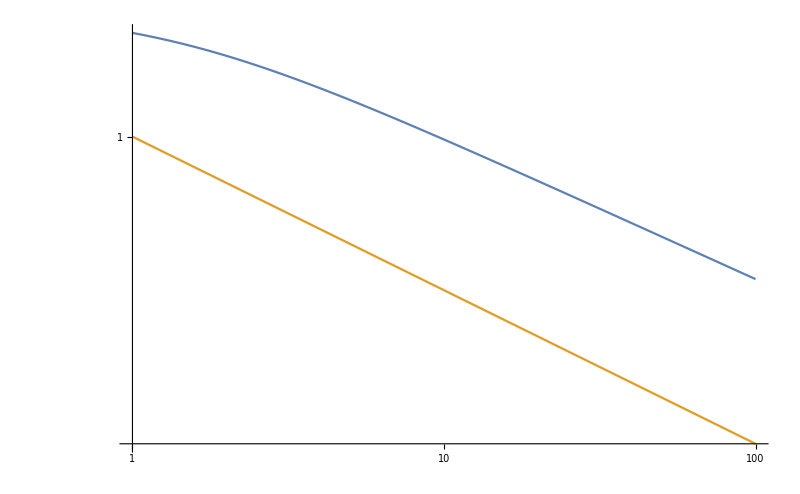

```mathematica
LogLogPlot[{1/(1-1/24*ghostGluLoopLandau[p,22/100,1,1/10000,2]/p^2),p^(-5/10000)(*,1/Log[100+p^2]*)},{p,10^0,10^2},WorkingPrecision->30,ImageSize->800]
```

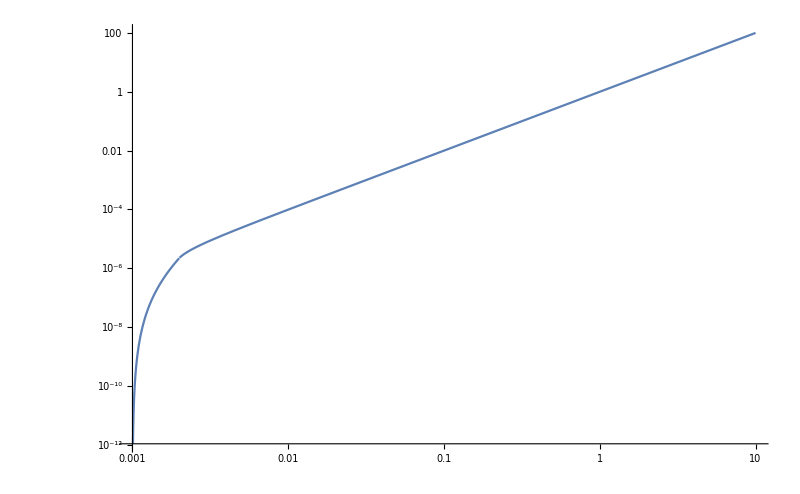

```mathematica
LogLogPlot[-Im[ghostGluLoopContLandau[w,Sqrt[4π*22/100],1/1000,1/1000,2]],{w,.001,10},WorkingPrecision->30,ImageSize->800]
```

### Discretization & Interpolation

#### Discretization

The discretized functions are stored in realtime_gluon _spectral _function _data.mx and do not need to be computed during initialization to run the notebook.

Need to resolve the IR, as the ghost constitutes the IR tail of the gluon spectral function. Need to adapt the grid such that the limit of λ1,λ2->0 can be resolved for each Minkowski frequency as the function becomes constant for λ1+λ2<w. In this way, the ghost self energy diagram can be interpolated up to λ1,λ2=0. This enables us to fully resolve the (analytic) ghost spectral function in the deep IR. Consequently, we can determine a lower integration bound for the ghost spectral integration upon inspection of the convergence behaviour. 
In a first step, an appropriate w_minof the frequency grid needs to determined. This is done be comparing the magnitudes of gluon and ghost polarization diagram, as this reveals from which lower frequency bound on it is sensible to resolve the ghost loop.

Initialize tables for discretization of not done yet.

```mathematica
ghostGluLoopTbl={};
ghostGluLoopTblE={};
DghostGluLoopTblμ2E={};
```

```mathematica
wRangeGhostGlu=10^Range[-5,4,1/10];
λRangeGhostGlu=10^Range[-500/101,4,1/20];
```

Discretize Minkowski diagram

```mathematica
Do[
Do[
Do[

tempRes=With[{g=1,μ=2},N[ghostGluLoopContLandau[wRangeGhostGlu[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim=With[{g=1,μ=2},N[ghostGluLoopContLandau[wRangeGhostGlu[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]/100,μ],30]];

AppendTo[
ghostGluLoopTbl,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],0},tempResLim}
];
AppendTo[
ghostGluLoopTbl,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostGluLoopTbl,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];
]

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
, {i, Length[wRangeGhostGlu]}]
```

Discretize Minkowski diagram

```mathematica
Do[
Do[
Do[

tempRes=With[{g=1,μ=2},N[ghostGluLoopLandau[wRangeGhostGlu[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim=With[{g=1,μ=2},N[ghostGluLoopLandau[wRangeGhostGlu[[i]],g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]/100,μ],30]];

AppendTo[
ghostGluLoopTblE,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],0},tempResLim}
];
AppendTo[
ghostGluLoopTblE,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
ghostGluLoopTblE,{{wRangeGhostGlu[[i]],λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];
]

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
, {i, Length[wRangeGhostGlu]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 («13»+1/3 (-5000000 10^(93«1»«3») (9/10000000000000000+(3 «1»)/5000000)+«1») Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 («13»+1/3 (-5000000 10^(«1») (9/10000000000000000+(3«1»«5»«1»«1»])/5000000)+«1») Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

Discretize Euclidean derivative

```mathematica
DghostGluLoopp0TblE={};
```

```mathematica
λRangeDGhostGlu=10^Range[-600/101,2,1/10];
```

```mathematica
{r,{DghostGluLoopp0TblE}}=Reap[
Do[
Do[

Sow[{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes=With[{g=1,μ=2},N[DghostGluLoopLandau[10^-8,g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]]}];

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (3 ((«1»)/(150000000000000 10^(10/101))+«27»+1/3 (9/(100000000000000 10^(10/101))-500000000 10^(91/101) (9/250000000000000000000000+(3 Power[«2»])/2500000000000)+30 10^(91/101) (3/10000000000000000-Power[«2»]/500000000+Power[«2»]/50000)) Log[16 ⅇ^-EulerGamma π]))/(2 π^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{Null,{{{{1/(10000 10^(96/101)),1/(10000 10^(96/101))},5.89541796510737912233777841005×10^-8+0. ⅈ},{{1/(10000 10^(96/101)),1/(10000 10^(1819/2020))},5.86816530466791808870527741948×10^-8+0. ⅈ},{{1/(10000 10^(96/101)),1/(10000 10^(859/1010))},5.8389105546125670556176454607×10^-8+0. ⅈ},32394,{{1000 10^(2019/2020),1000 10^(1817/2020)},0``-5.7708843707887905+0. ⅈ},{{1000 10^(2019/2020),1000 10^(959/1010)},0``-4.188932312776665+0. ⅈ},{{1000 10^(2019/2020),1000 10^(2019/2020)},-3.5008×10^-8+0. ⅈ}}}}
 |  |  |  |

```mathematica
{r,{DghostGluLoopTblE}}=Reap[
Do[
Do[

Sow[{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes=With[{g=1,μ=2},DghostGluLoopLandau[μ,g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ]]}];

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
];
```

```mathematica
Do[
Do[

tempRes=With[{g=1,μ=2},N[DghostGluLoopLandau[μ,g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]],μ],30]];

If[k==1,

tempResLim=With[{g=1,μ=2},N[DghostGluLoopLandau[μ,g,λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]/100,μ],30]];

AppendTo[
DghostGluLoopTblμ2E,{{λRangeGhostGlu[[j]],0},tempResLim}
];
AppendTo[
DghostGluLoopTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];,

AppendTo[
DghostGluLoopTblμ2E,{{λRangeGhostGlu[[j]],λRangeGhostGlu[[k]]},tempRes}
];
]

, {k,Length[λRangeGhostGlu]}]
, {j, Length[λRangeGhostGlu]}]
```

#### Interpolation

```mathematica
(*ghostGluLoopIntPol=Interpolation[ghostGluLoopTbl];
ghostGluLoopIntPolE=Interpolation[ghostGluLoopTblE];
DghostGluLoopμ2IntPolE=Interpolation[DghostGluLoopTblμ2E];*)
(*DghostGluLoopp0IntPolE=Interpolation[DghostGluLoopp0TblE];*)
```

### Spectral regularization

```mathematica
ghostGluLoopRegIntPol[w_,αs_,λ1_,λ2_,gluSpecFunc_,ghostSpecFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*gluSpecFunc[λ1]*ghostSpecFunc[λ2]*(ghostGluLoopIntPol[w,λ1,λ2]+w^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
ghostGluLoopRegIntPolE[p_,αs_,λ1_,λ2_,gluSpecFunc_,ghostSpecFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*gluSpecFunc[λ1]*ghostSpecFunc[λ2]*(ghostGluLoopIntPolE[p,λ1,λ2]-p^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
ghostGluLoopRegIntPolPole[w_,αs_,λ1_,gluSpecFunc_]:=With[{μ=2,λ2=0},4π*αs*λ1/π*gluSpecFunc[λ1]*(ghostGluLoopIntPol[w,λ1,λ2]+w^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
ghostGluLoopRegIntPolPoleE[p_,αs_,λ1_,gluSpecFunc_]:=With[{μ=2,λ2=0},4π*αs*λ1/π*gluSpecFunc[λ1]*(ghostGluLoopIntPolE[p,λ1,λ2]-p^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
DghostGluLoopp0RegIntPolE[αs_,λ1_,λ2_,gluSpecFunc_,ghostSpecFunc_]:=With[{μ=2},4π*αs*λ1*λ2/π^2*gluSpecFunc[λ1]*ghostSpecFunc[λ2]*(DghostGluLoopp0IntPolE[λ1,λ2]/(2*10^-8)-1/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
DghostGluLoopp0RegIntPolPoleE[αs_,λ1_,gluSpecFunc_]:=With[{μ=2,λ2=λRangeDGhostGlu[[1]]},4π*αs*λ1/π*gluSpecFunc[λ1]*(DghostGluLoopp0IntPolE[λ1,λ2]/(2*10^-8)-1/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2])]
```

DghostGluLoopp0EIntPol is a derivative wrt p. As we need the derivative wrt p^2, we need to divide by 2 p at the point where we take p to be zero, which is 10^-8.

## Analytic spectral functions ρ_A and ρ_c (0th iteration)

```mathematica
intPolFunc[w_,gridvals_,grid_]:=f[w]/.{f -> Interpolation[
Table[{grid[[j]],gridvals[[j]]},{j,Length[grid]}]
]
}
```

```mathematica
ΓA2[w_,αs_,mA_,mc_,μ_]:=-w^2+mA^2-1/24(gluonPolContLandau[w,Sqrt[4π*αs],mA,mA,μ]+ghostPolCont[w,Sqrt[4π*αs],mc,mc,μ])
ρA[w_,αs_,mA_,mc_,μ_]:=-2Im[ΓA2[w,αs,mA,mc,μ]]/(Re[ΓA2[w,αs,mA,mc,μ]]^2+Im[ΓA2[w,αs,mA,mc,μ]]^2)
```

```mathematica
ΓA2E[p_,αs_,mA_,mc_,μ_]:=p^2+mA^2-1/24(gluonPolContLandauE[p,Sqrt[4π*αs],mA,mA,μ]+ghostPol[p,Sqrt[4π*αs],mc,mc,μ])
Γc2E[p_,αs_,mA_,mc_,μ_]:=p^2-1/24ghostGluLoopLandau[p,Sqrt[4π*αs],mA,mc,μ]
```

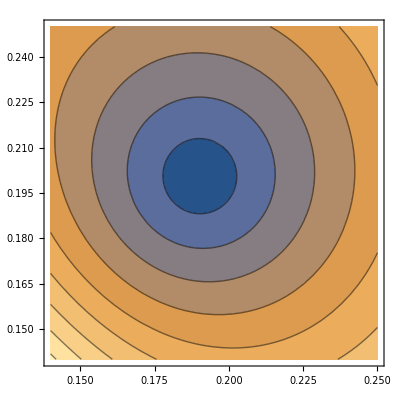

```mathematica
With[{αs=22/100,mA=1/2,mc=10^-6,μ=2},ContourPlot[Abs[ΓA2E[x+ⅈ*y,αs,mA,mc,μ]],{x,.14,.25},{y,.14,.25},WorkingPrecision->100,PlotPoints->10,MaxRecursion->2]]
```

```mathematica
With[{αs=22/100,mA=1/2,mc=10^-6,μ=2},FindRoot[ΓA2E[z,αs,mA,mc,μ],{z,1/10+.1*I}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{z→-0.213508+0.98585 ⅈ}

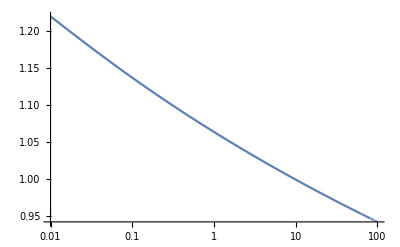

```mathematica
LogLinearPlot[p^2/Γc2E[p,22/100,10^-3,10^-3,2],{p,10^-2,10^2},WorkingPrecision->30]
```

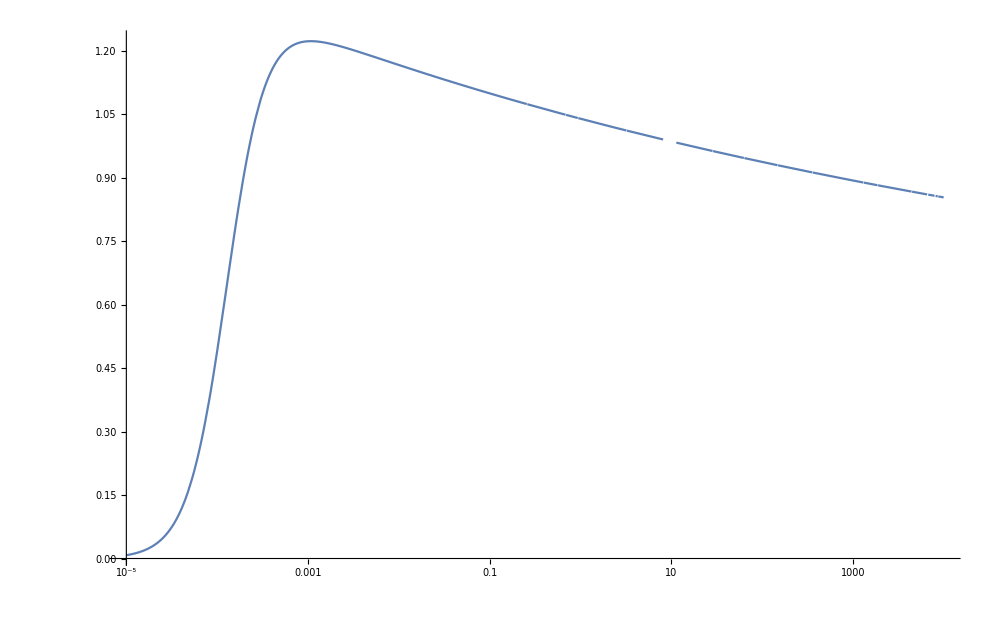

```mathematica
With[{mA=10^-4,μ=1,αs=22/1000},LogLinearPlot[{p^2/(ΓA2E[p,αs,mA,mA,μ])},{p,10^-5,10^4},WorkingPrecision->100,ImageSize->1000,PlotRange->All]]
```

```mathematica
Γc2[w_,αs_,mA_,mc_,μ_]:=-w^2+1/24ghostGluLoopContLandau[w,Sqrt[4π*αs],mA,mc,μ]
ρc[w_,αs_,mA_,mc_,μ_]:=-2Im[Γc2[w,αs,mA,mc,μ]]/(Re[Γc2[w,αs,mA,mc,μ]]^2+Im[Γc2[w,αs,mA,mc,μ]]^2)
```

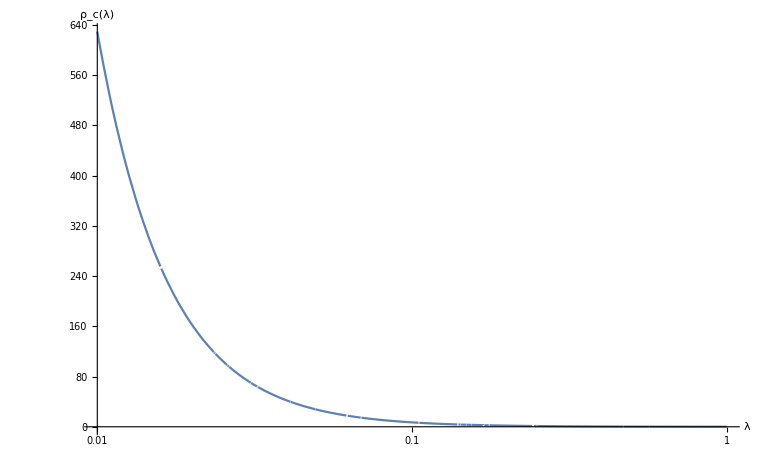

```mathematica
With[{αs=22/100,mc=λRangeGhostGlu[[1]],λmin=10^-2,λmax=10^0,μ=2},LogLinearPlot[{ρc[λ,αs,mc,mc,μ]},{λ,λmin,λmax},AxesLabel->{Style["λ",FontSize->14],Style["ρ_c(λ)",FontSize->14]},PlotRange->{{λmin,λmax},All},TicksStyle->Directive[14],WorkingPrecision->30]]
```

## Numeric spectral functions (iterative computation)

#### Iteration functions

```mathematica
ΓA2Iter[w_,mAsq_,gluPolIter_,ghostPolIter_]:=-w^2+mAsq-1/24(gluPolIter[w]+ghostPolIter[w])
ΓA2IterE[p_,mAsq_,gluPolIterE_,ghostPolIterE_]:=p^2+mAsq-1/24(gluPolIterE[p]+ghostPolIterE[p])
ρAIter[w_,mAsq_,gluPolIter_,ghostPolIter_]:=2Im[1/ΓA2Iter[w,mAsq,gluPolIter,ghostPolIter]]
```

```mathematica
ΓA2IterScal[w_,Z_,mA_,gluPolIter_,ghostPolIter_,a_,b_]:=-Z*w^2+mA-1/24(a*gluPolIter[w]+b*ghostPolIter[w])+a/24Re[gluPolIter[10^-4]+ghostPolIter[10^-4]]
ΓA2IterEScal[p_,Z_,mA_,gluPolIterE_,ghostPolIterE_,a_,b_]:=Z*p^2+mA-1/24(a*gluPolIterE[p]+b*ghostPolIterE[p])+a/24Re[gluPolIterE[10^-4]+ghostPolIterE[10^-4]]
ρAIterScal[w_,Z_,mA_,gluPolIter_,ghostPolIter_,a_,b_]:=-2Im[ΓA2IterScal[w,Z,mA,gluPolIter,ghostPolIter,a,b]]/(Re[ΓA2IterScal[w,Z,mA,gluPolIter,ghostPolIter,a,b]]^2+Im[ΓA2IterScal[w,Z,mA,gluPolIter,ghostPolIter,a,b]]^2)
```

```mathematica
Γc2Iter[w_,ghostGluLoopIter_]:=-w^2-1/24ghostGluLoopIter[w]
Γc2IterE[p_,ghostGluLoopIterE_]:=p^2-1/24ghostGluLoopIterE[p]
DΓc2p0IterE[DghostGluLoopIterE_]:=1-1/24DghostGluLoopIterE
ρcIter[w_,ghostGluLoopIter_]:=2Im[1/Γc2Iter[w,ghostGluLoopIter]]
```

#### Interpolated initial spectral functions

```mathematica
(*ρAIntPolScal=Interpolation[With[{cO=8/10,cOR=1},Table[{λ,10^-1*ρAScal[λ,cO,cOR]},{λ,10^Join[Range[-4,-1,1/50],Range[-.9,2,1/20]]}]]];*)
ρcIntPolScal=Interpolation[Table[{λ,With[{ε=10^-2,a=0},ρcScal[λ,ε,a]]},{λ,10^Range[-6,2,1/30]}]];
```

```mathematica
ρAIntPolBW=Interpolation[With[{Γ=(-10I+1)/1000,m=(-I+1)/10000},Table[{λ,Re[BWmod[λ,Γ,m]]},{λ,10^Join[Range[-4,-1,1/50],Range[-.9,2,1/20]]}]]];
ρcIntPolBW=Interpolation[With[{αs=22/100,μ=2,m=101/100*10^-4},Table[{λ,N[2Im[1/Γc2[λ,αs,m,m,μ]],20]},{λ,10^Range[-4,4,1/50]}]]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(11 (-(18103 √7701 Re[2 Log[Plus[«2»]]-2 Log[Plus[«2»]]])/102010000000000-(5201 √7701 Re[-2 Log[Plus[«2»]]+2 Log[Plus[«2»]]])/51005000000000))/(100 π ((-1/100000000+(11 (Times[«2»]+Times[«2»]+Times[«2»]+«1»+«1»+Times[«2»]+Times[«2»]+Times[«2»]))/(200 π))^2+(121 (-(18103 Power[«2»] Re[«1»])/102010000000000-(«1»)/(51«10»00))^2)/(40000 π^2))).

#### Breit - Wiegners

```mathematica
BWE[p_,Γ_,m_]:=1/((p+Γ)^2+m)
BWmod[w_,Γ_,m_]:=Exp[-(w-10^-2)^2*10^5]/(10^2((I*w+Γ)^2+m^2))
BW2[w_,Γ_,m_]:=1/(((I*w+Γ)^2+m^2)^2)
```

#### Scaling functions

```mathematica
ρAScal[λ_,crossOverStart_,crossOverEnd_]:=(-2λ^(2(-1+2*κ)))(1-((1-Exp[-λ+crossOverStart])(UnitStep[λ-crossOverStart]UnitStep[crossOverEnd-λ](λ-crossOverStart)/(crossOverEnd-crossOverStart)+UnitStep[λ-crossOverEnd])))-10^1*λ^-2((1-Exp[-λ+crossOverStart])(UnitStep[λ-crossOverStart]UnitStep[crossOverEnd-λ](λ-crossOverStart)/(crossOverEnd-crossOverStart)+UnitStep[λ-crossOverEnd]))+10^3*Exp[-(λ-crossOverStart)^2/(1/2*10^-1)]
ρcScal[λ_,ε_,a_]:=2Im[1/(Γc2ScalE[-I(λ+I*ε),a])-1/(λ^2*Log[1-100λ^2])]
```

```mathematica
logistFunc[x_,x0_,r_]:=1/(1+Exp[r(-x+x0)]);
κ=(93-Sqrt[1201])/98;
```

```mathematica
Γc2ScalE[p_,ε_]:=With[{x0=1,r=2},p^2(p^2+ε)^κ]
Γc2Scal[w_]:=With[{x0=2,r=2},(-I*w)^(2+2κ)(1-logistFunc[w,x0,r])-UnitStep[w-(x0-1)]w^2(Log[-w^2]-2I*π)logistFunc[w,x0,r]]
```

#### Plots

General::munfl: Exp[-788.632] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1020.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1316.26] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

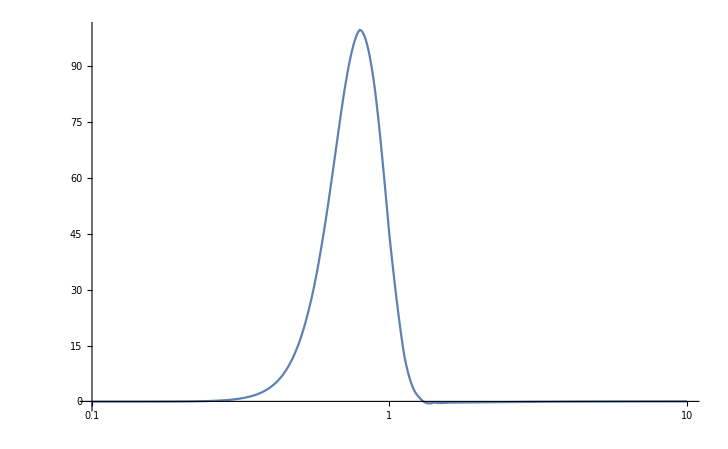

```mathematica
With[{mA=Sqrt[1/5],mc=λRangeGhostGlu[[1]],μ=2,αs=22/100},LogLinearPlot[{ρAIntPolScal[λ](*,1/10λ^(2(-1+2*κ))*)(*,λ^-2*)},{λ,10^-1,10^1},PlotRange->All]]
```

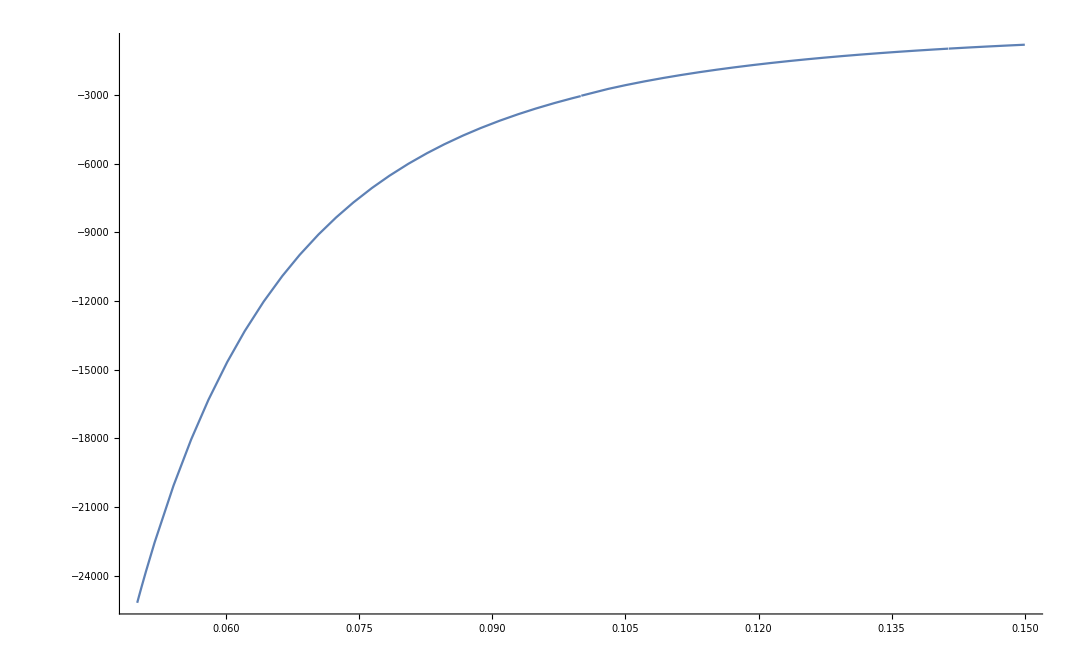

```mathematica
Plot[{ρcScal[λ,10^-2,0](*,λ^-(2+2κ)*)},{λ,.05,.15},PlotRange->All]
```

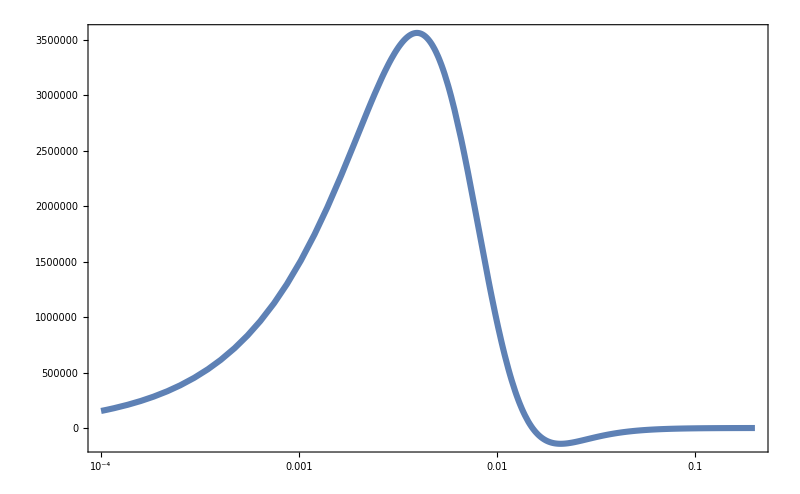

```mathematica
With[{mA=Sqrt[1/5],mc=λRangeGhostGlu[[1]],μ=2,αs=22/100},LogLinearPlot[{ρcIntPolScal[λ]},{λ,10^-4,.2}(*,WorkingPrecision->30*),PlotRange->All,ImageSize->800]]
```

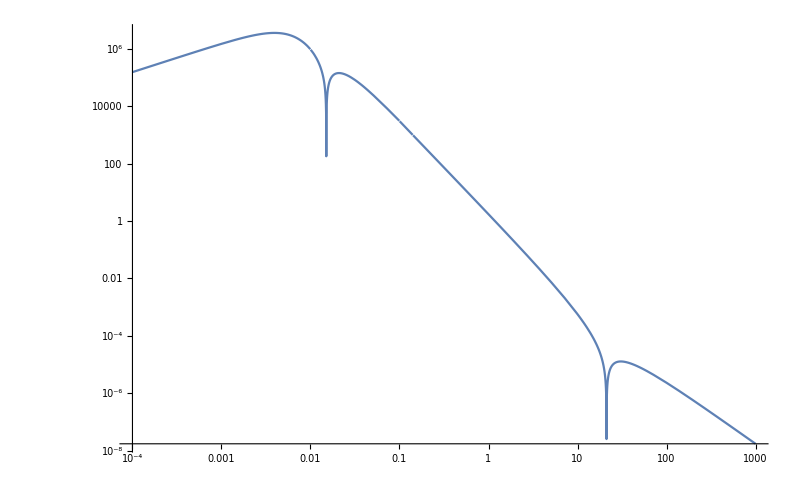

```mathematica
LogLogPlot[{Abs[ρcScal[λ,10^-2,0]]},{λ,10^-4,10^3}(*,WorkingPrecision->30*),PlotRange->All,ImageSize->800]
```

#### Initialization of lists for iteration

```mathematica
ghostGluLoopIters={};
```

```mathematica
gluPolIters={};
ghostPolIters={};
ghostGluLoopIters={};
gluPolItersE={};
ghostPolItersE={};
ghostGluLoopItersE={};
DghostGluLoopp0ItersE={};
ghostPoleResidues={};
ghostSpecFuncs={};
gluSpecFuncs={};
```

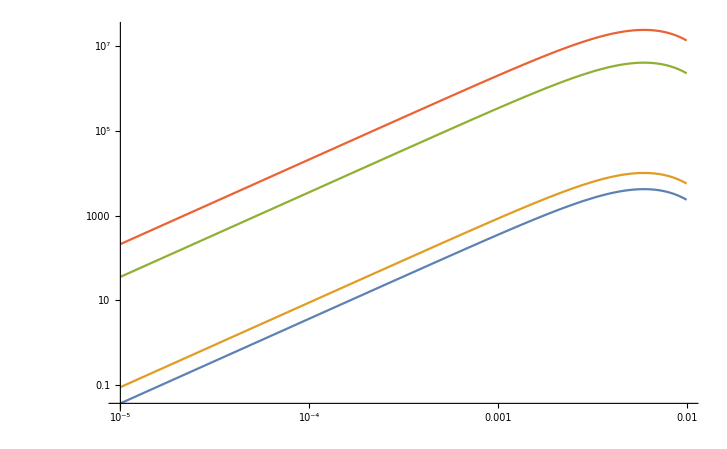

```mathematica
With[{p={1,10,50,100}},LogLogPlot[{Evaluate[Abs[(ghostPolIntPolE[#,λ1,1]-ghostPolIntPolE[2,λ1,1])ρcIntPol[λ1]λ1]&/@p]},{λ1,10^-5,10^-2},PlotRange->All]]
```

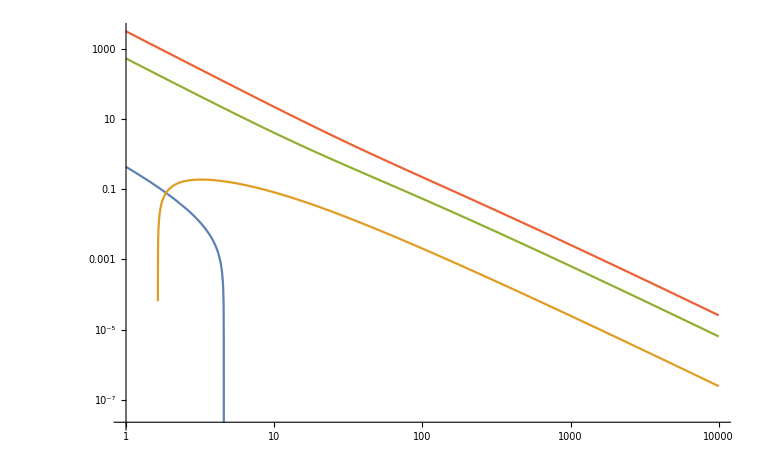

```mathematica
With[{p={1,10,50,100}},LogLogPlot[{Evaluate[(ghostPolIntPolE[#,λ1,1]-ghostPolIntPolE[2,λ1,1])ρcIntPol[λ1]λ1&/@p]},{λ1,10^0,10^4},PlotRange->All]]
```

```mathematica
gluPolIters=allScalLong2[[1]];
ghostPolIters=allScalLong2[[2]];
gluPolItersE=allScalLong2[[3]];
ghostPolItersE=allScalLong2[[4]];
gluSpecFuncs=allScalLong2[[5]];
```

Cut data set

```mathematica
gluPolIters//Length
```

7

```mathematica
With[{r=Range[1,7]},
gluPolIters=gluPolIters[[r]];
gluPolItersE=gluPolItersE[[r]];
ghostPolIters=ghostPolIters[[r]];
ghostPolItersE=ghostPolItersE[[r]];
gluSpecFuncs=gluSpecFuncs[[r]];
ghostSpecFuncs=ghostSpecFuncs[[r]];
ghostPoleResidues=ghostPoleResidues[[r]];
];
```

```mathematica
gluPolIters=specRep1[[1]];
ghostPolIters=specRep1[[2]];
gluPolItersE=specRep1[[3]];
ghostPolItersE=specRep1[[4]];
gluSpecFuncs=specRep1[[5]];
```

```mathematica
Clear[specFunccTmp]
```

```mathematica
<<"specRepGhostScalAnton.mx"
```

```mathematica
<<"specRepCoupled.mx"
```

```mathematica
asdf
```

#### Coupled system

```mathematica
Do[
With[{mAsq=-20,Z=10^0,b=1,αs=2,μ=2,λAmin=λRange[[1]],λAmax=80,λcmin=10^-3,λcmax=80,momRange=Join[10^Range[-3,1,1/20],10^Range[1.1,3,1/10]]},


If[i==1,

(*Use interpolated analytic spectral function in first iteration*)
specFuncATmp=ρAIntPolScal;
specFunccTmp=ρcScal[#,10^-2,0]&;
(*specFunccTmp[λ_]:=Evaluate[ghostSpecFuncStandalone];
ghostPoleResTmp=ghostResidueStandalone;*)

(*ghostPolReg0Int=NIntegrate[ghostPolReg0[αs,λ1,λ2,specFunccTmp],{λ1,λcmin,λcmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive"(*,"SymbolicProcessing"->0*)},PrecisionGoal->3];
ghostPolReg1Int=NIntegrate[ghostPolReg1[αs,λ1,λ2,specFunccTmp],{λ1,λcmin,λcmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive"(*,"SymbolicProcessing"->0*)},PrecisionGoal->3];*)
,

specFuncATmp[λ_]:=Evaluate[gluSpecFuncs[[-1]]];
specFunccTmp[λ_]:=Evaluate[ghostSpecFuncs[[-1]]];
ghostPoleResTmp=ghostPoleResidues[[-1]];

];

(*Compute iterated diagram employing the updated spectral functions*)
iterT=AbsoluteTiming[


(*GLUON POLARIZATION*)


Print["Computing gluon loop realtime"];
AppendTo[
gluPolIters,gluPolVals(*=ShowProgress[Table[
{w=momRange[[j]],NIntegrate[gluPolRegIntPol[w,αs,λ1,λ2,specFuncATmp],{λ1,λAmin,zeroXRe,λAmax},{λ2,λAmin,zeroXRe,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{j,Length[momRange]}
]]*)
];

Print["Computing gluon loop imaginary time"];
(*Euclidean*)
AppendTo[
gluPolItersE,gluPolEVals(*=ShowProgress[Table[
{p=momRange[[j]],NIntegrate[gluPolRegIntPolE[p,αs,λ1,λ2,specFuncATmp],{λ1,λAmin,zeroXRe,λAmax},{λ2,λAmin,zeroXRe,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{j,Length[momRange]}
]]*)
];
(*AppendTo[gluPolIters,gluPolIters[[-1]]];
AppendTo[gluPolItersE,gluPolItersE[[-1]]];*)

(*GHOST POLARIZATION*)

(*This stays the same if the ghost spec func is not iterated and the ghost loop is computed only in the first iteration.*)

(*Minkowski*)
Print["Computing ghost loop realtime"];
AppendTo[
ghostPolIters,ghostPolVals=ShowProgress[Table[
{w=momRange[[j]],ghostPoleResTmp^2*ghostPolRegIntPolPolePole[w,αs]+2ghostPoleResTmp*NIntegrate[ghostPolRegIntPolPole[w,αs,λ1,specFunccTmp],{λ1,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[ghostPolRegIntPol[w,αs,λ1,λ2,specFunccTmp],{λ1,λcmin,λcmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive"(*,"SymbolicProcessing"->0*)},PrecisionGoal->2]},{j,Length[momRange]}
]]
];

(*Euclidean*)
Print["Computing ghost loop imaginary time"];
AppendTo[
ghostPolItersE,ghostPolEVals=ShowProgress[Table[
{p=momRange[[j]],ghostPoleResTmp^2*ghostPolRegIntPolPolePoleE[p,αs]+2ghostPoleResTmp*NIntegrate[ghostPolRegIntPolPoleE[p,αs,λ1,specFunccTmp],{λ1,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[ghostPolRegIntPolE[p,αs,λ1,λ2,specFunccTmp],{λ1,λcmin,λcmax},{λ2,λcmin,λcmax},Method->"InterpolationPointsSubdivision",PrecisionGoal->2]},{j,Length[momRange]}
]]
];

(*GHOST SELF ENERGY*)

(*Minkowski*)
Print["Computing ghost gluon loop real time"];
AppendTo[
ghostGluLoopIters,ghostGluLoopVals=ShowProgress[Table[
{w=momRange[[j]],ghostPoleResTmp*NIntegrate[ghostGluLoopRegIntPolPole[w,αs,λ1,specFuncATmp],{λ1,λAmin,zeroXRe,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+Sqrt[b]*NIntegrate[ghostGluLoopRegIntPol[w,αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,zeroXRe,λAmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{j,Length[momRange]}
]]
];

(*Euclidean*)
Print["Computing ghost gluon loop imaginary time"];
AppendTo[
ghostGluLoopItersE,ghostGluLoopValsE=ShowProgress[Table[
{p=momRange[[j]],ghostPoleResTmp*NIntegrate[ghostGluLoopRegIntPolPoleE[p,αs,λ1,specFuncATmp],{λ1,λAmin,zeroXRe,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->2]+Sqrt[b]*NIntegrate[ghostGluLoopRegIntPolE[p,αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,zeroXRe,λAmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->2]},{j,Length[momRange]}
]]
];

(*Extract residue of ghost spectral function*)
AppendTo[
DghostGluLoopp0ItersE,
ghostPoleResTmp*NIntegrate[DghostGluLoopp0RegIntPolPoleE[αs,λ1,specFuncATmp],{λ1,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[DghostGluLoopp0RegIntPolE[αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,λAmax},{λ2,λcmin,zeroXRe,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]
];

AppendTo[
ghostPoleResidues,1/DΓc2p0IterE[DghostGluLoopp0ItersE[[-1]]]
];


(*CALCULATE UPDATED SPECTRAL FUNCTIONS*)

(*gluon*)
(*BW*)
(*gluSpecFuncUp=ρAIter[λ,mAsq,Interpolation[Join[{{0,Re[gluPolIters[[i]][[1]][[2]]]}},gluPolIters[[i]]]],Interpolation[Join[{{0,Re[ghostPolIters[[i]][[1]][[2]]]}},ghostPolIters[[i]]]]];*)

(*Scaling*)
gluSpecFuncUp=ρAIterScal[λ,Z,mAsq,Interpolation[gluPolIters[[-1]]],Interpolation[ghostPolIters[[-1]]],1,b];

AppendTo[
gluSpecFuncs, gluSpecFuncUp
];

(*ghost*)
ghostSpecFuncUpTbl=Table[{ghostGluLoopIters[[-1,j,1]],val=2Im[ghostGluLoopIters[[-1,j,2]]/24]/Abs[-ghostGluLoopIters[[-1,j,1]]^2-1/24*ghostGluLoopIters[[-1,j,2]]]^2;N[Round[val,10^(MantissaExponent[val][[2]]-2.3)]]},{j,Length[ghostGluLoopIters[[-1]]]}];
ghostSpecFuncUp=Interpolation[ghostSpecFuncUpTbl][λ];

AppendTo[
ghostSpecFuncs,ghostSpecFuncUp
];


][[1]];
(*SAVE FILES*)
(*allScalLong2={
(*LOOPS MINKOWSKI*)
gluPolIters,ghostPolIters,(*ghostGluLoopIters,ghostPoleResidues,*)
(*LOOPS EUCLIDEAN*)
gluPolItersE,ghostPolItersE,(*ghostGluLoopItersE,DghostGluLoopp0ItersE,*)
(*SPECTRAL FUNCTIONS*)
gluSpecFuncs(*,ghostSpecFuncs*)};*)

(*DumpSave["realtime_gluon_spectral_function_data.mx",{
(*SPECTRAL FUNCTIONS*)
ghostSpecFuncStandalone,ghostPoleResidueStandalone,
(*GLUON INTERPOLATING FUNCTIONS*)
gluPolIntPol,gluPolIntPolE,DgluPolμ0IntPolE,DgluPolμ2IntPolE,(*gluPolTbl,DgluPolμ2TblE,gluPolμ2TblE,gluPolTblE,*)
(*GHOST LOOP INTERPOLATING FUNCTIONS*)
ghostPolIntPol,ghostPolIntPolE,DghostPolμ0IntPolE,DghostPolμ2IntPolE,(*ghostPolTbl,ghostPolTblE,ghostPolTblESubtr1,ghostPolTblμ2E,DghostPolTblμ2E,*)
(*GHOST GLUON LOOP INTERPOLATING FUNCTIONS*)
ghostGluLoopIntPol,ghostGluLoopIntPolE,DghostGluLoopμ2IntPolE,DghostGluLoopp0IntPolE(*ghostGluLoopTbl,ghostGluLoopTblE,DghostGluLoopp0TblE,DghostGluLoopTblμ2E,*),
(*RESULTS*)
allBWmA0,allBWmAn0p4,allscal,allScalLong,allScalLong2}];*)

(*Print iteration time*)
Print[StringForm["Iteration `` complete. (tIter = ``)",i,iterT]];

(*Clean up*)
Clear[specFuncATmp,specFunccTmp];
]
, {i,7,7}
]
```

Computing gluon loop realtime

Computing gluon loop imaginary time

Computing ghost loop realtime

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ1 near {λ1} = {0.553599}. NIntegrate obtained 0.199944-5.39346×10^-16 ⅈ and 0.00180938 for the integral and error estimates.

$Aborted

```mathematica
DumpSave["local_kernel.mx","Global`"];
```

```mathematica
ghostPoleResidues
```

{0.777577,1.00021+0. ⅈ,1.00101+0. ⅈ,0.998511+0. ⅈ,1.00029+0. ⅈ,-13.3357+0. ⅈ}

```mathematica
ghostSpecFuncs[[-1]]=ghostSpecFuncs[[-1]]/10;
```

```mathematica
ghostPoleResTmp
```

1.00032+0. ⅈ

```mathematica
ghostPoleResidues[[-1]]=ghostPoleResidues[[-1]]/10
```

0.100031+0. ⅈ

```mathematica
gluPolIters=gluPolIters[[Range[1,10]]];
gluPolItersE=gluPolItersE[[Range[1,10]]];
ghostPolIters=Drop[ghostPolIters,-1];
ghostPolItersE=Drop[ghostPolItersE,-1];
gluSpecFuncs=Drop[gluSpecFuncs,-1];
```

```mathematica
ghostPoleResidues=ghostPoleResidues[[Range[1,3]]];
```

```mathematica
gluSpecFuncs=Drop[gluSpecFuncs,-1];
```

```mathematica
gluPolItersE=Drop[gluPolItersE,-1];
```

```mathematica
ghostPolIters=Drop[ghostPolIters,-1];
```

```mathematica
ghostSpecFuncs=Drop[ghostSpecFuncs,-1];
```

```mathematica
ghostPoleResidues=Drop[ghostPoleResidues,-1];
```

```mathematica
ghostPropIter=Table[{p,ghostPoleResidues[[-1]]/p^2+NIntegrate[ghostSpecFuncs[[-1]]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}];
```

```mathematica
ghostDressIter=With[{c=c1},Table[{ghostDressPropContr[[i,1]],c*ghostPoleResidues[[-1]]+ghostDressPropContr[[i,2]]/c},{i,Length[ghostDressPropContr]}]];
```

```mathematica
ghostDressPropContr=Table[{p,p^2*NIntegrate[ghostSpecFuncs[[-1]]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}];
```

```mathematica
ghostDressPropContr[[31,1]]//Length
```

0

```mathematica
ghostPoleResidues[[-1]]*=c1;
```

```mathematica
ghostSpecFuncs[[-1]]*=1/c1;
```

```mathematica
ghostPoleResidues
```

{0.777577,1.00021+0. ⅈ,1.00101+0. ⅈ,0.998511+0. ⅈ,1.00029+0. ⅈ,1.62156+0. ⅈ}

```mathematica
ghostPoleResidues[[-1]]=ghostPoleResidues[[-2]];
```

```mathematica
ghostDressIter
```

{{1/1000,1.62153+0. ⅈ},{1/(100 10^(9/10)),1.62151+0. ⅈ},{1/(100 10^(4/5)),1.62148+0. ⅈ},{1/(100 10^(7/10)),1.62144+0. ⅈ},{1/(100 10^(3/5)),1.62138+0. ⅈ},{1/(100 √10),1.62129+0. ⅈ},{1/(100 10^(2/5)),1.62116+0. ⅈ},{1/(100 10^(3/10)),1.62096+0. ⅈ},{1/(100 10^(1/5)),1.62066+0. ⅈ},{1/(100 10^(1/10)),1.62022+0. ⅈ},{1/100,1.61958+0. ⅈ},{1/(10 10^(9/10)),1.61863+0. ⅈ},{1/(10 10^(4/5)),1.61725+0. ⅈ},{1/(10 10^(7/10)),1.61525+0. ⅈ},{1/(10 10^(3/5)),1.61239+0. ⅈ},{1/(10 √10),1.60833+0. ⅈ},{1/(10 10^(2/5)),1.60261+0. ⅈ},{1/(10 10^(3/10)),1.59467+0. ⅈ},{1/(10 10^(1/5)),1.5838+0. ⅈ},{1/(10 10^(1/10)),1.56914+0. ⅈ},{1/10,1.54974+0. ⅈ},{1/10^(9/10),1.52457+0. ⅈ},{1/10^(4/5),1.49267+0. ⅈ},{1/10^(7/10),1.45325+0. ⅈ},{1/10^(3/5),1.40587+0. ⅈ},{1/(√10),1.35061+0. ⅈ},{1/10^(2/5),1.28817+0. ⅈ},{1/10^(3/10),1.21989+0. ⅈ},{1/10^(1/5),1.14764+0. ⅈ},{1/10^(1/10),1.07359+0. ⅈ},{1,1.+0. ⅈ},{10^(1/10),0.928885+0. ⅈ},{10^(1/5),0.861882+0. ⅈ},{10^(3/10),0.800141+0. ⅈ},{10^(2/5),0.74433+0. ⅈ},{√10,0.694693+0. ⅈ},{10^(3/5),0.651135+0. ⅈ},{10^(7/10),0.61332+0. ⅈ},{10^(4/5),0.580758+0. ⅈ},{10^(9/10),0.552879+0. ⅈ},{10,0.529098+0. ⅈ},{10 10^(1/10),0.508855+0. ⅈ},{10 10^(1/5),0.491637+0. ⅈ},{10 10^(3/10),0.476995+0. ⅈ},{10 10^(2/5),0.464542+0. ⅈ},{10 √10,0.453959+0. ⅈ},{10 10^(3/5),0.44499+0. ⅈ},{10 10^(7/10),0.437445+0. ⅈ},{10 10^(4/5),0.431182+0. ⅈ},{10 10^(9/10),0.426097+0. ⅈ},{100,0.422092+0. ⅈ}}

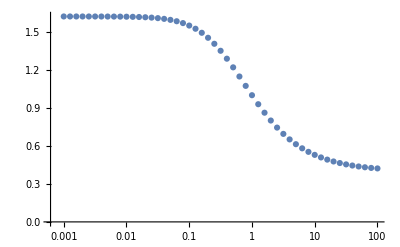

```mathematica
ListLogLinearPlot[ghostDressIter]
```

```mathematica
ghostPoleResidues
```

{0.777577,1.00021+0. ⅈ,1.00101+0. ⅈ,0.998511+0. ⅈ,1.00029+0. ⅈ,1.62156+0. ⅈ,-0.195331+0. ⅈ}

```mathematica
NIntegrate[λ*gluSpecFuncs[[-2]]/2/π,{λ,10^-3,10^1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.27208}. NIntegrate obtained 0.394688 and 0.00114534 for the integral and error estimates.

0.394688

```mathematica
Solve[c*ghostPoleResidues[[-2]]+ghostDressPropContr[[31,2]]/c==1/10,c,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→-0.758041},{c→0.81971}}

```mathematica
c1
```

-0.621373

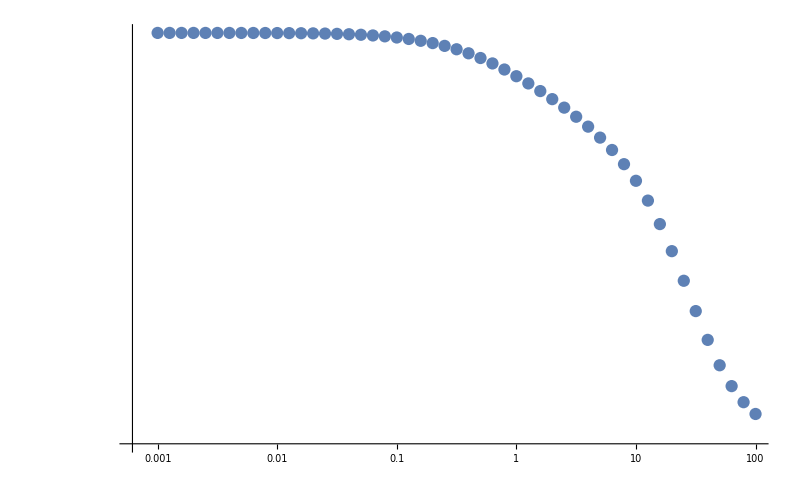

```mathematica
Show[{ListLogLogPlot[ghostDressIter,ImageSize->800]}]
```

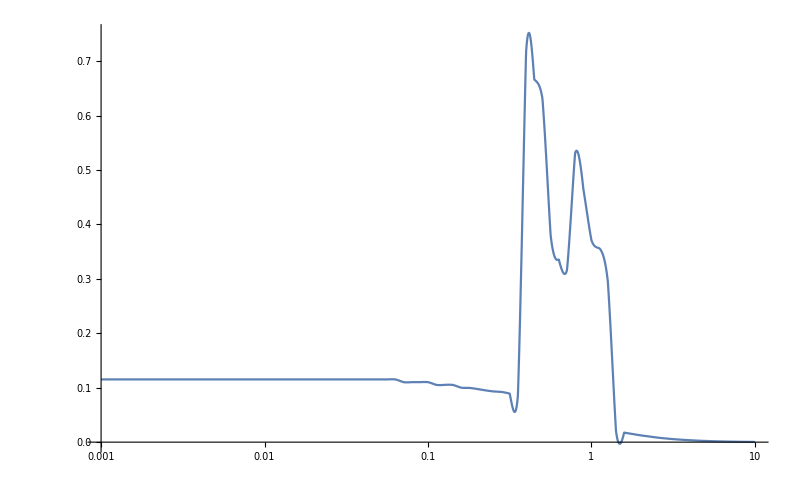

```mathematica
LogLinearPlot[{ghostSpecFuncs[[-1]](*,ρcIter[λ,Interpolation[ghostGluLoopIters[[-1]]]]*)},{λ,10^-3,10^1},ImageSize->800,WorkingPrecision->30,PlotRange->All]
```

```mathematica
Table[{p,AbsoluteTiming[NIntegrate[ghostGluLoopRegIntPol[p,22/100,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,10^-3,80},{λ2,10^-3,80},Method->"GlobalAdaptive",PrecisionGoal->3]]},{p,10^Range[-2,-2]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in λ1 near {λ1,λ2} = {1.2920955220130852539736638207888751803123547726262132426057847513,4.5324601029721831605803575915805144692844624168485663780500028163}. NIntegrate obtained 2.9756×10^-8+4.91005×10^-18 ⅈ and 4.23579×10^-11 for the integral and error estimates.

{{1/100,{2.6408,2.9756×10^-8}}}

```mathematica
AbsoluteTiming[With[{p=1/100},NIntegrate[4/π*22/100*λ1*λ2*specFuncATmp[λ1]*specFunccTmp[λ2]*(ghostGluLoopContLandau[p,1,λ1,λ2,2]+p^2/4*DghostGluLoopLandau[2,1,λ1,λ2,2]),{λ1,10^-3,87},{λ2,10^-3,87},Method->"GlobalAdaptive",PrecisionGoal->3]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in λ1 near {λ1,λ2} = {1.2920473583109218086127141654704953373705353194745784926472008944,78.7379}. NIntegrate obtained 1.24324×10^13+4.93535×10^9 ⅈ and 3.71934×10^13 for the integral and error estimates.

{2.7949,1.24324×10^13+4.93535×10^9 ⅈ}

```mathematica
Table[{p,AbsoluteTiming[With[{μ=2,αs=22/100,λmax=80},NIntegrate[4π*αs*λ1*λ2/π^2*specFuncATmp[λ1]*specFunccTmp[λ2]*(ghostGluLoopIntPol[p,λ1,λ2]+p^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2]),{λ1,10^-3,λmax},{λ2,10^-3,λmax},Method->"GlobalAdaptive",PrecisionGoal->3]](*+With[{μ=2,αs=22/100},NIntegrate[4π*αs*λ1*λ2/π^2*specFuncATmp[λ1]*specFunccTmp[λ2]*(ghostGluLoopIntPol[p,λ1,λ2]+p^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2]),{λ1,10,87},{λ2,10,87},Method->"GlobalAdaptive",PrecisionGoal->3]]*)]},{p,10^Range[-2,-2]}]
```

{{1/100,{3.03545,2.96755×10^-8}}}

```mathematica
ghostSpecFuncs[[-1]]=Interpolation[ghostSpecFuncUpTbl][λ];
```

```mathematica
Table[{p,AbsoluteTiming[With[{μ=2,αs=22/100},NIntegrate[4π*αs*λ1*λ2/π^2*specFuncATmp[λ1]*specFunccTmp[λ2]*(ghostGluLoopIntPol[p,λ1,λ2]+p^2/(2μ)*DghostGluLoopμ2IntPolE[λ1,λ2]),{λ1,10^-4,50},{λ2,10^-4,50},Method->"GlobalAdaptive",PrecisionGoal->2]]]},{p,10^Range[-3,2]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
Length[ghostSpecFuncs]
```

7

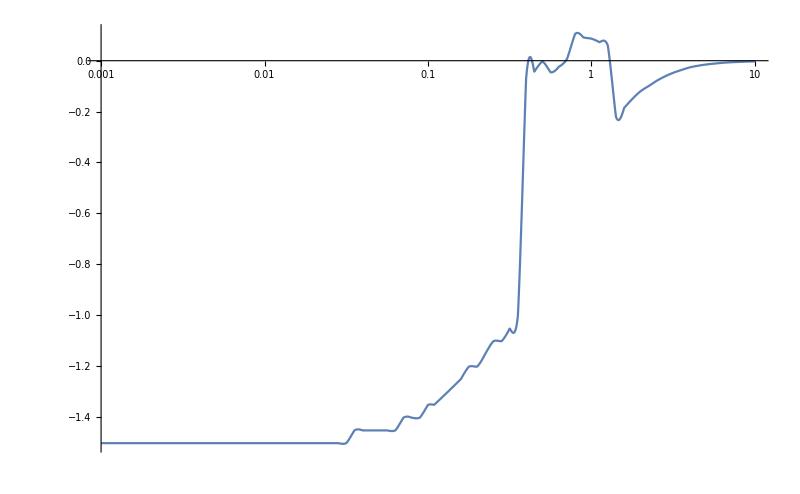

```mathematica
With[{i={-1}},LogLinearPlot[{Evaluate[ghostSpecFuncs[[#]]&/@i]},{λ,10^-3,10},ImageSize->800,PlotRange->All]]
```

```mathematica
ghostSpecFuncUpTbl=Table[{ghostGluLoopIters[[-1,j,1]],val=2Im[ghostGluLoopIters[[-1,j,2]]/24]/Abs[-ghostGluLoopIters[[-1,j,1]]^2-1/24*ghostGluLoopIters[[-1,j,2]]]^2;N[Round[val,10^(MantissaExponent[val][[2]]-2.3)]]},{j,Length[ghostGluLoopIters[[-1]]]}];
ghostSpecFuncUp=Interpolation[ghostSpecFuncUpTbl][λ];
```

```mathematica
ghostSpecFuncs[[-1]]=ghostSpecFuncUp;
```

```mathematica
ghostPoleResidues
```

{0.777577,1.00021+0. ⅈ,1.00101+0. ⅈ,0.998511+0. ⅈ,1.00359+0. ⅈ,1.00335+0. ⅈ,1.00024+0. ⅈ,0.100031+0. ⅈ,1.00003+0. ⅈ}

#### Checks for iteration

```mathematica
<<"specRepCoupled.mx"
```

```mathematica
Length[gluPolIters]
```

6

```mathematica
DumpSave["specRepCoupled.mx",{gluPolIters,gluPolItersE,ghostPolIters,ghostPolItersE,ghostGluLoopIters,ghostGluLoopItersE,DghostGluLoopp0ItersE,gluSpecFuncs,ghostPoleResidues,ghostSpecFuncs}];
```

```mathematica
DumpSave["specRepGhostScalAnton.mx",{gluPolIters,gluPolItersE,ghostPolIters,ghostPolItersE,gluSpecFuncs}];
```

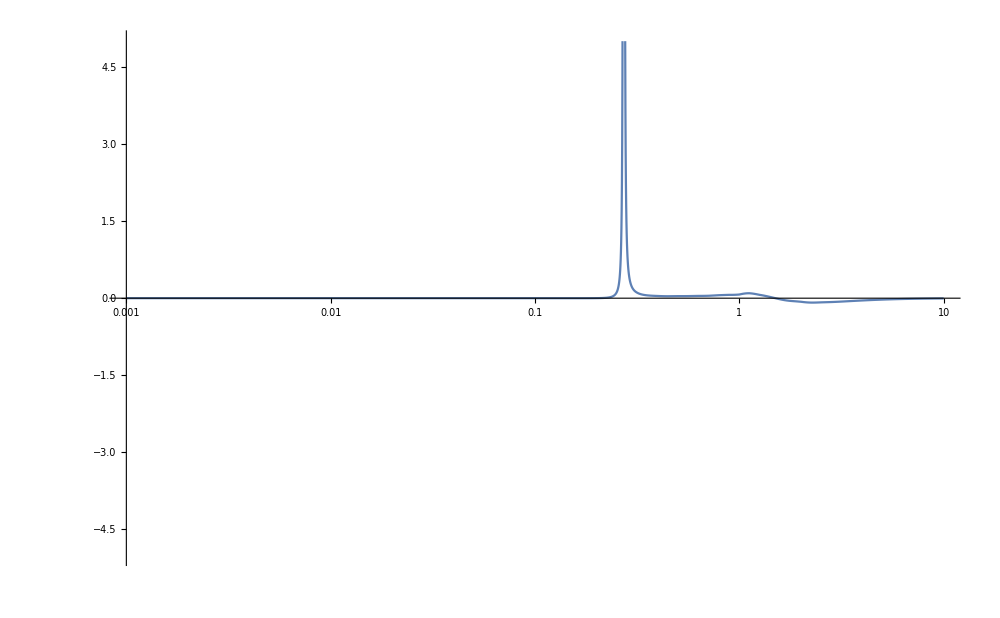

```mathematica
With[{mA=5,Z=3,b=10^-2,αs=22/100,i={-2},λmin=10^-3,λmax=10},LogLinearPlot[{(*Evaluate[allScalLong[[-1]][[#]]&/@i]*)(*Evaluate[ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[#]]],Interpolation[allScalLong2[[2]][[#]]],1,b]&/@i],*)Evaluate[gluSpecFuncs[[#]]&/@i](*,allScalLong2[[5]][[2]]*)},{λ,λmin,λmax},(*PlotRange->All,*)ImageSize->1000,PlotRange->{{λmin,λmax},{-5,5}}]]
```

```mathematica
gluSpecFuncs[[-1]]=ρAIterScal[λ,3,5,Interpolation[gluPolIters[[-1]]],Interpolation[ghostPolIters[[-1]]],1,1/100];
```

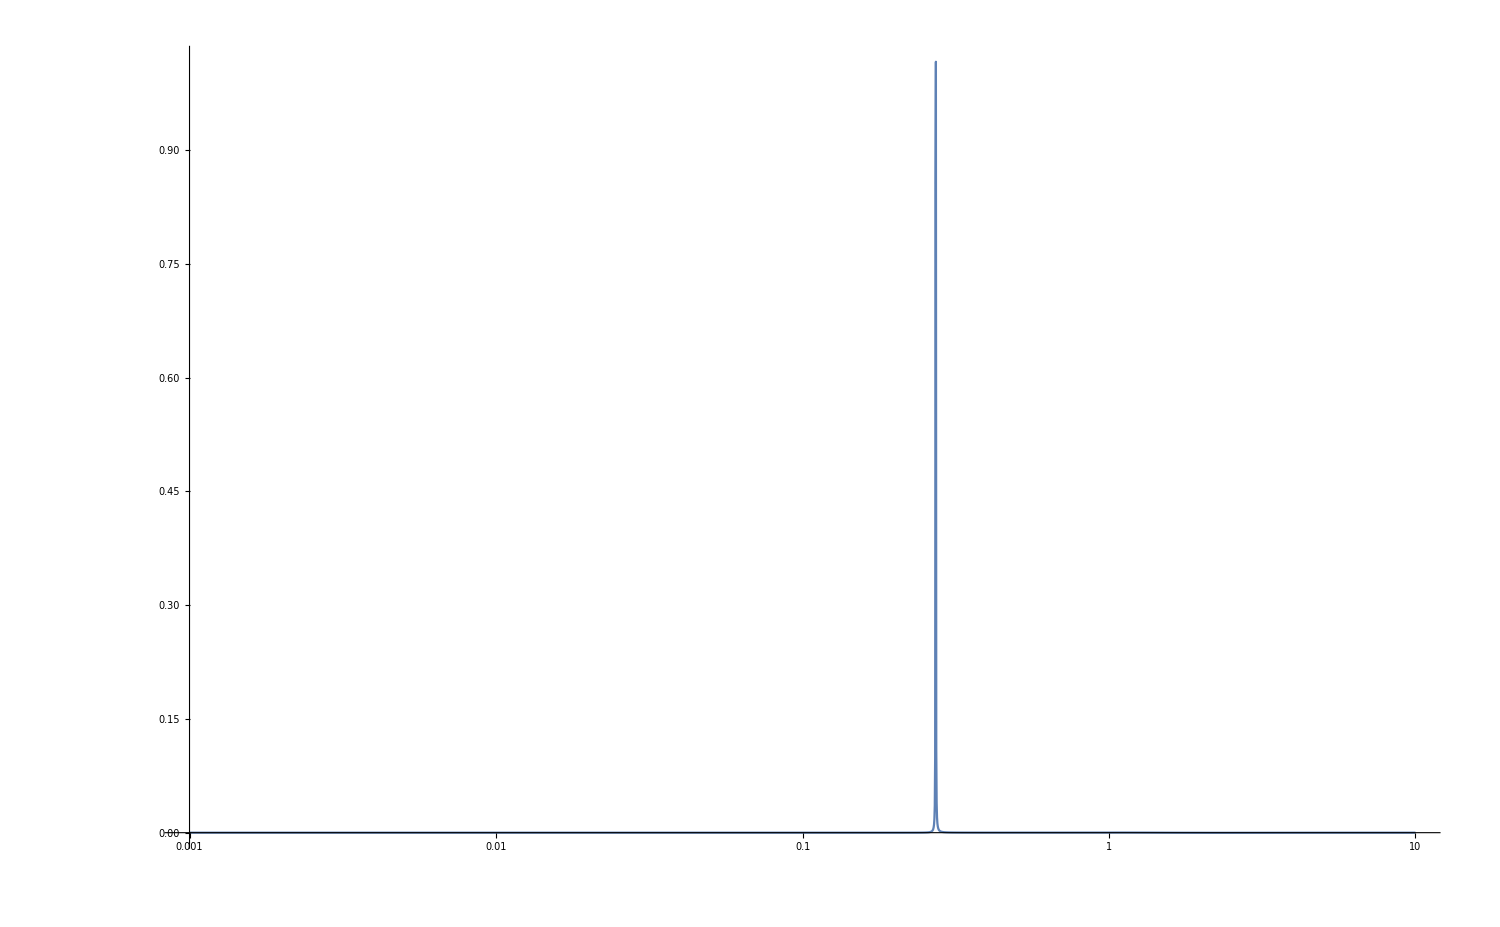

```mathematica
With[{mA=-20,Z=10^0,b=10^0,αs=22/100,i={-1},λmin=10^-3,λmax=10},LogLinearPlot[{Evaluate[Im[1/(-Z*ω^2+mA-1/24(Interpolation[gluPolIters[[#]]][ω]+b*Interpolation[ghostPolIters[[#]]][ω]-Interpolation[gluPolIters[[#]]][10^-4]-b*Interpolation[ghostPolIters[[#]]][10^-4]))]&/@i]},{ω,λmin,λmax},(*PlotRange->All,*)ImageSize->1500,PlotRange->(*{{λmin,λmax},{-.002,.002}}*)All]]
```

```mathematica
-Z*w^2+mA-1/24(a*gluPolIter[w]+b*ghostPolIter[w])+a/24Re[gluPolIter[10^-4]+ghostPolIter[10^-4]]
```

```mathematica
gluPolIters[[-1]]
```

{{1/1000,-92.9169+3.12748×10^-16 ⅈ},{1/(100 10^(19/20)),-84.8209+5.60211×10^-16 ⅈ},{1/(100 10^(9/10)),-84.8209+1.14702×10^-15 ⅈ},{1/(100 10^(17/20)),-84.821+2.23024×10^-15 ⅈ},{1/(100 10^(4/5)),-84.821+4.56637×10^-15 ⅈ},{1/(100 10^(3/4)),-84.8211+8.87875×10^-15 ⅈ},{1/(100 10^(7/10)),-84.8212+1.81791×10^-14 ⅈ},{1/(100 10^(13/20)),-92.9173+3.83685×10^-14 ⅈ},{1/(100 10^(3/5)),-92.9174+7.85587×10^-14 ⅈ},{1/(100 10^(11/20)),-84.8215+1.40719×10^-13 ⅈ},{1/(100 √10),-92.9177+3.12748×10^-13 ⅈ},{1/(100 10^(9/20)),-92.918+6.08099×10^-13 ⅈ},{1/(100 10^(2/5)),-84.8222+1.14702×10^-12 ⅈ},{1/(100 10^(7/20)),-92.9187+2.42089×10^-12 ⅈ},{1/(100 10^(3/10)),-84.823+4.56637×10^-12 ⅈ},{1/(100 10^(1/4)),-92.9198+9.63772×10^-12 ⅈ},{1/(100 10^(1/5)),-84.8243+1.81791×10^-11 ⅈ},{1/(100 10^(3/20)),-92.9216+3.83685×10^-11 ⅈ},{1/(100 10^(1/10)),-84.8263+7.23722×10^-11 ⅈ},{1/(100 10^(1/20)),-84.8277+1.40719×10^-10 ⅈ},{1/100,-84.8295+2.88119×10^-10 ⅈ},{1/(10 10^(19/20)),-84.8318+5.60211×10^-10 ⅈ},{1/(10 10^(9/10)),-84.8346+1.14702×10^-9 ⅈ},{1/(10 10^(17/20)),-92.9358+2.42089×10^-9 ⅈ},{1/(10 10^(4/5)),-84.8427+4.56637×10^-9 ⅈ},{1/(10 10^(3/4)),-84.8484+8.87875×10^-9 ⅈ},{1/(10 10^(7/10)),-84.8555+1.81791×10^-8 ⅈ},{1/(10 10^(13/20)),-92.9645+3.83685×10^-8 ⅈ},{1/(10 10^(3/5)),-92.9768+7.85587×10^-8 ⅈ},{1/(10 10^(11/20)),-92.9924+1.52748×10^-7 ⅈ},{1/(10 √10),-84.9081+2.88119×10^-7 ⅈ},{1/(10 10^(9/20)),-84.9308+5.60211×10^-7 ⅈ},{1/(10 10^(2/5)),-84.9593+1.14702×10^-6 ⅈ},{1/(10 10^(7/20)),-93.1069+2.42089×10^-6 ⅈ},{1/(10 10^(3/10)),-93.1562+4.95672×10^-6 ⅈ},{1/(10 10^(1/4)),-93.2184+9.63772×10^-6 ⅈ},{1/(10 10^(1/5)),-93.2968+0.0000197331 ⅈ},{1/(10 10^(3/20)),-93.3957+0.0000383685 ⅈ},{1/(10 10^(1/10)),-93.5213+0.0000785588 ⅈ},{1/(10 10^(1/20)),-93.679+0.000152748 ⅈ},{1/10,-93.8781+0.000312748 ⅈ},{1/10^(19/20),-94.13+0.0006081 ⅈ},{1/10^(9/10),-94.449+0.00124507 ⅈ},{1/10^(17/20),-94.8536+0.00241363 ⅈ},{1/10^(4/5),-88.3802+0.00462812 ⅈ},{1/10^(3/4),-88.9906+0.00898646 ⅈ},{1/10^(7/10),-89.7756+0.0186118 ⅈ},{1/10^(13/20),-90.783+0.0406835 ⅈ},{1/10^(3/5),-92.1188+0.0761202 ⅈ},{1/10^(11/20),-101.253+0.187651 ⅈ},{1/(√10),-103.936+0.211719 ⅈ},{1/10^(9/20),-107.779+0.0073068 ⅈ},{1/10^(2/5),-103.349-0.898475 ⅈ},{1/10^(7/20),-114.28-3.79074 ⅈ},{1/10^(3/10),-117.492-8.4917 ⅈ},{1/10^(1/4),-127.791-16.9911 ⅈ},{1/10^(1/5),-129.593-26.9653 ⅈ},{1/10^(3/20),-132.644-36.3733 ⅈ},{1/10^(1/10),-143.013-49.0032 ⅈ},{1/10^(1/20),-149.101-63.187 ⅈ},{1,-155.609-80.6228 ⅈ},{10^(1/20),-162.345-102.475 ⅈ},{10^(1/10),-168.721-129.851 ⅈ},{10^(3/20),-173.694-164.502 ⅈ},{10^(1/5),-171.75-203.411 ⅈ},{10^(1/4),-189.969-282.72 ⅈ},{10^(3/10),-101.505-232.96 ⅈ},{10^(7/20),-157.864-440.343 ⅈ},{10^(2/5),-120.419-543.801 ⅈ},{10^(9/20),-39.9911-501.605 ⅈ},{√10,27.1805-796.571 ⅈ},{10^(11/20),147.364-962.045 ⅈ},{10^(3/5),294.285-824.582 ⅈ},{10^(13/20),475.526-942.147 ⅈ},{10^(7/10),823.249-1648.24 ⅈ},{10^(3/4),999.909-1425.52 ⅈ},{10^(4/5),1704.29-2334.13 ⅈ},{10^(17/20),2353.-2778.54 ⅈ},{10^(9/10),2554.27-2248.41 ⅈ},{10^(19/20),4413.63-4275.96 ⅈ},{10,5889.45-5144.04 ⅈ},{12.5893,9893.59-6865.41 ⅈ},{15.8489,17732.8-11062.4 ⅈ},{19.9526,30710.8-16927.6 ⅈ},{25.1189,51073.2-24689.9 ⅈ},{31.6228,85782.3-37302. ⅈ},{39.8107,143438.-56708.7 ⅈ},{50.1187,238820.-86560.3 ⅈ},{63.0957,404543.-137781. ⅈ},{79.4328,669538.-212374. ⅈ},{100.,624881.-111110. ⅈ},{125.893,1.0013×10^6-179166. ⅈ},{158.489,1.59536×10^6-310330. ⅈ},{199.526,4.85306×10^6-1.4523×10^6 ⅈ},{251.189,7.92674×10^6-2.50617×10^6 ⅈ},{316.228,6.19768×10^6-2.23166×10^6 ⅈ},{398.107,2.12365×10^7-8.03842×10^6 ⅈ},{501.187,1.46287×10^7-9.29841×10^6 ⅈ},{630.957,2.20173×10^7-1.90604×10^7 ⅈ},{794.328,3.24737×10^7-3.89996×10^7 ⅈ},{1000.,1.68255×10^8-1.03121×10^8 ⅈ}}

```mathematica
ghostPolIters[[-1]]
```

{{1/1000,-4.51097-7.41992×10^-6 ⅈ},{1/(100 10^(19/20)),-4.51097-9.46137×10^-6 ⅈ},{1/(100 10^(9/10)),-4.51098-0.0000120319 ⅈ},{1/(100 10^(17/20)),-4.511-0.0000152684 ⅈ},{1/(100 10^(4/5)),-4.51101-0.0000193432 ⅈ},{1/(100 10^(3/4)),-4.51103-0.0000244733 ⅈ},{1/(100 10^(7/10)),-4.51106-0.000030932 ⅈ},{1/(100 10^(13/20)),-4.51109-0.000039063 ⅈ},{1/(100 10^(3/5)),-4.51113-0.0000492995 ⅈ},{1/(100 10^(11/20)),-4.51117-0.0000621866 ⅈ},{1/(100 √10),-4.51123-0.0000784106 ⅈ},{1/(100 10^(9/20)),-4.5113-0.0000988354 ⅈ},{1/(100 10^(2/5)),-4.51139-0.000124549 ⅈ},{1/(100 10^(7/20)),-4.5115-0.00015692 ⅈ},{1/(100 10^(3/10)),-4.51163-0.000197673 ⅈ},{1/(100 10^(1/4)),-4.51179-0.000248978 ⅈ},{1/(100 10^(1/5)),-4.51199-0.000313567 ⅈ},{1/(100 10^(3/20)),-4.51223-0.00039488 ⅈ},{1/(100 10^(1/10)),-4.51254-0.000497247 ⅈ},{1/(100 10^(1/20)),-4.51291-0.00062612 ⅈ},{1/100,-4.51336-0.00078836 ⅈ},{1/(10 10^(19/20)),-4.51392-0.00099261 ⅈ},{1/(10 10^(9/10)),-4.5146-0.00124974 ⅈ},{1/(10 10^(17/20)),-4.51543-0.00157346 ⅈ},{1/(10 10^(4/5)),-4.51645-0.00198099 ⅈ},{1/(10 10^(3/4)),-4.5177-0.00249404 ⅈ},{1/(10 10^(7/10)),-4.51922-0.00313993 ⅈ},{1/(10 10^(13/20)),-4.52107-0.00395306 ⅈ},{1/(10 10^(3/5)),-4.52333-0.00497673 ⅈ},{1/(10 10^(11/20)),-4.52608-0.00626546 ⅈ},{1/(10 √10),-4.52943-0.00788786 ⅈ},{1/(10 10^(9/20)),-4.53348-0.00993035 ⅈ},{1/(10 10^(2/5)),-4.5384-0.0125017 ⅈ},{1/(10 10^(7/20)),-4.54435-0.0157388 ⅈ},{1/(10 10^(3/10)),-4.55154-0.0198141 ⅈ},{1/(10 10^(1/4)),-4.5602-0.0249446 ⅈ},{1/(10 10^(1/5)),-4.57063-0.0314036 ⅈ},{1/(10 10^(3/20)),-4.58315-0.0395349 ⅈ},{1/(10 10^(1/10)),-4.58826-0.0497718 ⅈ},{1/(10 10^(1/20)),-4.60605-0.0626592 ⅈ},{1/10,-4.62721-0.0788837 ⅈ},{1/10^(19/20),-4.65228-0.0982237 ⅈ},{1/10^(9/10),-4.68188-0.123313 ⅈ},{1/10^(17/20),-4.71661-0.154715 ⅈ},{1/10^(4/5),-4.75721-0.193948 ⅈ},{1/10^(3/4),-4.80426-0.24289 ⅈ},{1/10^(7/10),-4.85849-0.303804 ⅈ},{1/10^(13/20),-4.92029-0.379456 ⅈ},{1/10^(3/5),-4.99-0.473099 ⅈ},{1/10^(11/20),-5.06822-0.588611 ⅈ},{1/(√10),-5.15382-0.730511 ⅈ},{1/10^(9/20),-5.24585-0.903967 ⅈ},{1/10^(2/5),-5.34315-1.11496 ⅈ},{1/10^(7/20),-5.44218-1.36985 ⅈ},{1/10^(3/10),-5.54341-1.67618 ⅈ},{1/10^(1/4),-5.62913-2.04114 ⅈ},{1/10^(1/5),-5.71758-2.47405 ⅈ},{1/10^(3/20),-5.77183-2.9823 ⅈ},{1/10^(1/10),-5.79532-3.57684 ⅈ},{1/10^(1/20),-5.77091-4.26607 ⅈ},{1,-5.68769-5.06314 ⅈ},{10^(1/20),-5.52409-5.97774 ⅈ},{10^(1/10),-5.25142-7.02852 ⅈ},{10^(3/20),-4.85957-8.25447 ⅈ},{10^(1/5),-4.29124-9.61221 ⅈ},{10^(1/4),-3.51811-11.1954 ⅈ},{10^(3/10),-2.47308-13.0178 ⅈ},{10^(7/20),-1.08713-15.1144 ⅈ},{10^(2/5),0.734026-17.5351 ⅈ},{10^(9/20),3.13038-20.3421 ⅈ},{√10,6.26271-23.6047 ⅈ},{10^(11/20),10.305-27.4151 ⅈ},{10^(3/5),15.5686-31.8886 ⅈ},{10^(13/20),22.3817-37.153 ⅈ},{10^(7/10),31.1886-43.3545 ⅈ},{10^(3/4),42.5844-50.7074 ⅈ},{10^(4/5),57.2758-59.4126 ⅈ},{10^(17/20),76.1629-69.9179 ⅈ},{10^(9/10),100.592-82.4626 ⅈ},{10^(19/20),131.971-97.4663 ⅈ},{10,172.343-115.531 ⅈ},{12.5893,291.346-163.871 ⅈ},{15.8489,487.595-235.184 ⅈ},{19.9526,810.578-340.749 ⅈ},{25.1189,1342.59-499.326 ⅈ},{31.6228,2215.53-738.028 ⅈ},{39.8107,3647.75-1099.61 ⅈ},{50.1187,5993.7-1644.03 ⅈ},{63.0957,9801.51-2481.22 ⅈ},{79.4328,16014.8-3776.57 ⅈ},{100.,26123.2-5769.49 ⅈ},{125.893,42582.2-8865.99 ⅈ},{158.489,69439.-13721. ⅈ},{199.526,113259.-21198.4 ⅈ},{251.189,185223.-32927. ⅈ},{316.228,303962.-51241.7 ⅈ},{398.107,501292.-79857.1 ⅈ},{501.187,832329.-124755. ⅈ},{630.957,1.40687×10^6-199024. ⅈ},{794.328,2.33094×10^6-265818. ⅈ},{1000.,4.18652×10^6-594811. ⅈ}}

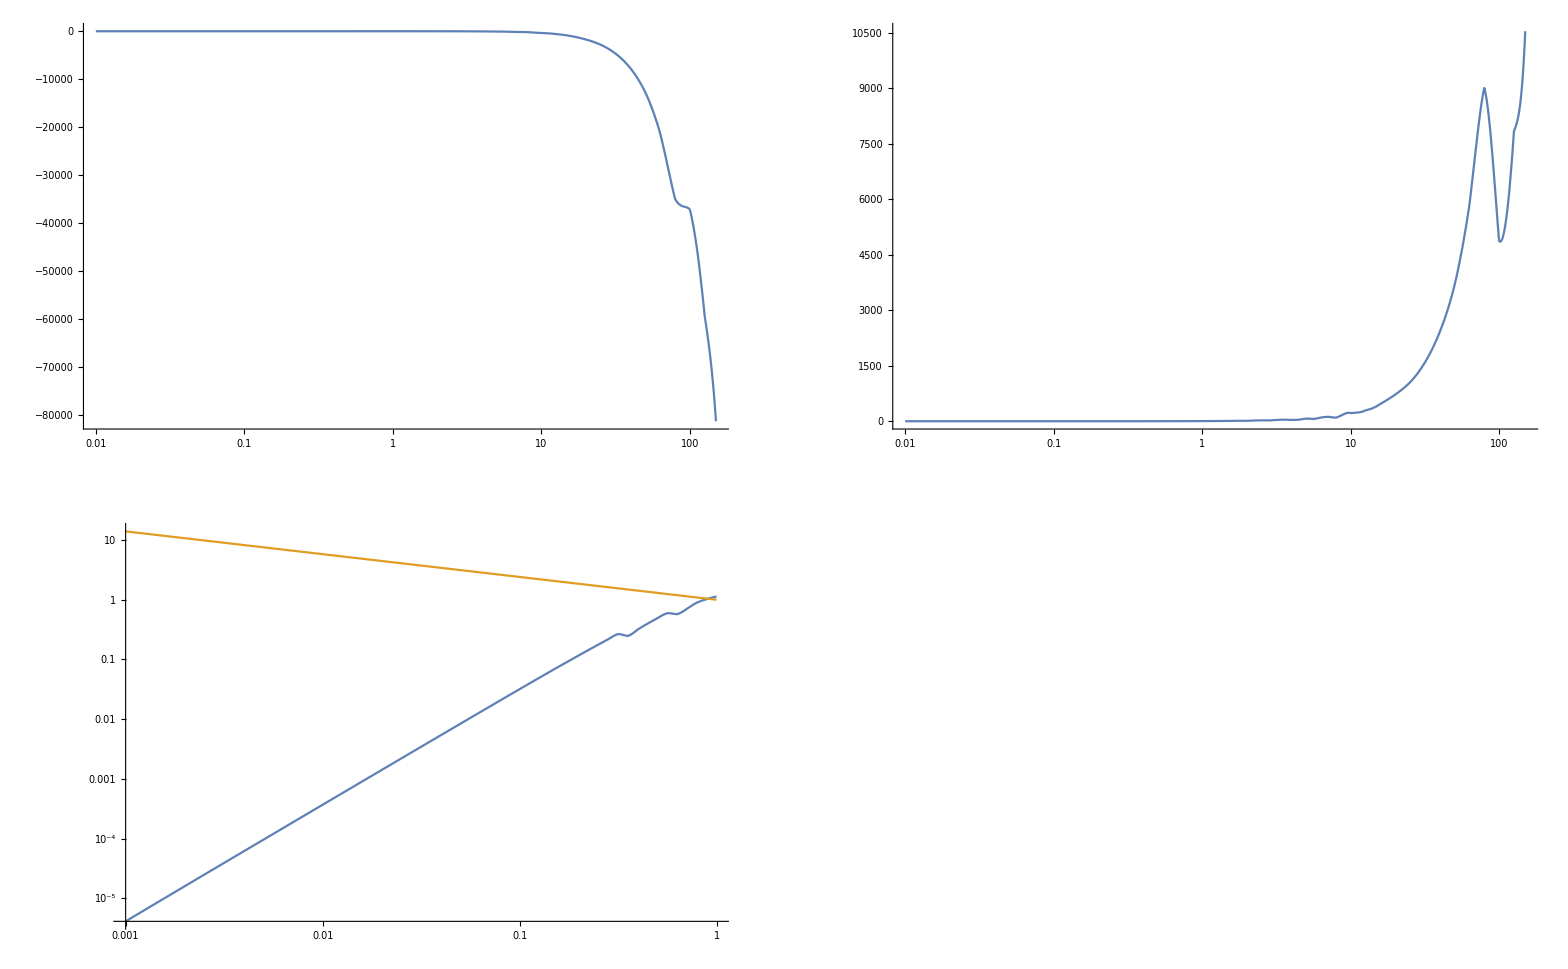

```mathematica
With[{mA=0,Z=10^0,b=10^0,αs=22/100,i={-1},ωmin=10^-2,ωmax=150},GraphicsGrid[{{LogLinearPlot[{Evaluate[Re[-Z*ω^2+mA-1/24(Interpolation[gluPolIters[[#]]][ω]+b*Interpolation[ghostPolIters[[#]]][ω]-Interpolation[gluPolIters[[#]]][10^-4]-b*Interpolation[ghostPolIters[[#]]][10^-4])]&/@i]},{ω,ωmin,ωmax},(*PlotRange->All,*)PlotRange->All],LogLinearPlot[{Evaluate[Im[-Z*ω^2+mA-1/24(Interpolation[gluPolIters[[#]]][ω]+b*Interpolation[ghostPolIters[[#]]][ω]-Interpolation[gluPolIters[[#]]][10^-4]-b*Interpolation[ghostPolIters[[#]]][10^-4])]&/@i]},{ω,ωmin,ωmax},(*PlotRange->All,*)PlotRange->All]},{LogLogPlot[{Evaluate[-Re[Z*p^2+mA-1/24(Interpolation[gluPolItersE[[#]]][p]+b*Interpolation[ghostPolItersE[[#]]][p]-Interpolation[gluPolItersE[[#]]][10^-4]-b*Interpolation[ghostPolItersE[[#]]][10^-4])]&/@i],p^(2(1-2κ))},{p,10^-3,1},(*PlotRange->All,*)PlotRange->All]}},ImageSize->1600]]
```

```mathematica
zeroXRe=ω/.With[{i={-1},mA=-20,Z=10^0,b=10^0,αs=22/100},FindRoot[Evaluate[Re[-Z*ω^2+mA-1/24(Interpolation[gluPolIters[[#]]][ω]+b*Interpolation[ghostPolIters[[#]]][ω]-Interpolation[gluPolIters[[#]]][10^-4]-b*Interpolation[ghostPolIters[[#]]][10^-4])]&/@i],{ω,.3}]]
```

0.272053

```mathematica
gluSpecFuncs[[-1]]=With[{mA=-20,Z=10^0,b=10^0,αs=22/100,i=-1,λmin=10^-2,λmax=1/2},ρAIterScal[λ,Z,mA,Interpolation[gluPolIters[[i]]],Interpolation[ghostPolIters[[i]]],1,b]];
```

```mathematica
gluDressSpec=With[{i=-1},Table[{p,p^2*NIntegrate[(*ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[i]]],Interpolation[allScalLong2[[2]][[i]]],1,b]*)gluSpecFuncs[[i]]*λ/π/(p^2+λ^2),{λ,10^-3,zeroXRe,10^2},PrecisionGoal->3]},{p,10^Range[-4,4,1/10]}]];
```

```mathematica
gluSpecFuncs[[-1]]=gluSpecFuncs[[-1]]/gluDressSpec[[41,2]];
```

```mathematica
gluDressSpec[[41]]
```

{1,1.}

```mathematica
gluPropSpec=With[{i=-1},Table[{p,NIntegrate[(*ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[i]]],Interpolation[allScalLong2[[2]][[i]]],1,b]*)gluSpecFuncs[[i]]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}]];
```

```mathematica
FindMaximum[gluSpecFuncs[[6]],λ]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2030.57,{λ→1.27888}}

#### Plots & checks

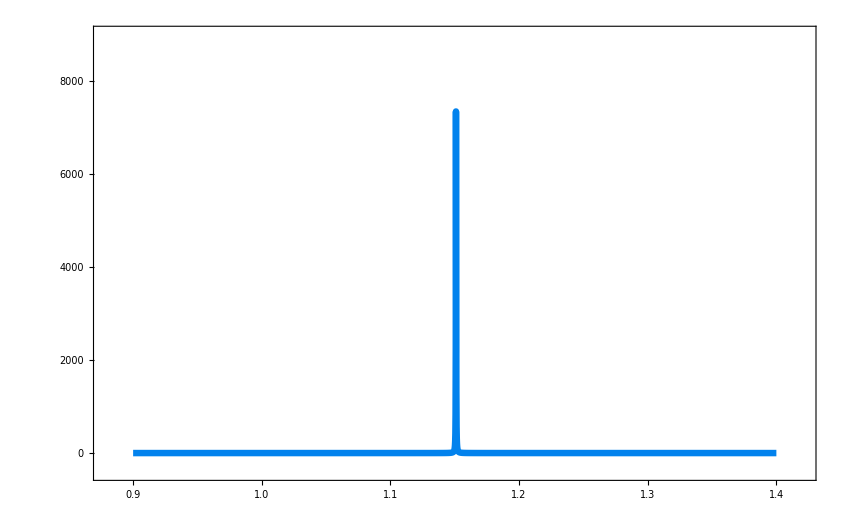

```mathematica
Module[{c=4,mA=3.5,Z=3,b=0.1,αs=22/100,i={9},localPlotColors=clearPlotColors},
scalSpecFuncModPlotInlet=Plot[c*(gluSpecFuncs[[6]]/.{λ->1/.9l}),{l,.9,1.4},Exclusions->None,
PlotRange->{xRange={.88,1.42},yRange={c*-100,c*2250}},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LinTicks[Sequence@@xRange,ShowMinorTickLabels->False,ShowMinorTicks->False],LinTicks[Sequence@@xRange,ShowMinorTickLabels->False,ShowMinorTicks->False,ShowTickLabels->False]}},

LabelStyle->Directive[Red,FontFamily->defaultFontStyle,12],
PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],


ImagePadding->{{35,2},{30,2}}
]
]
```

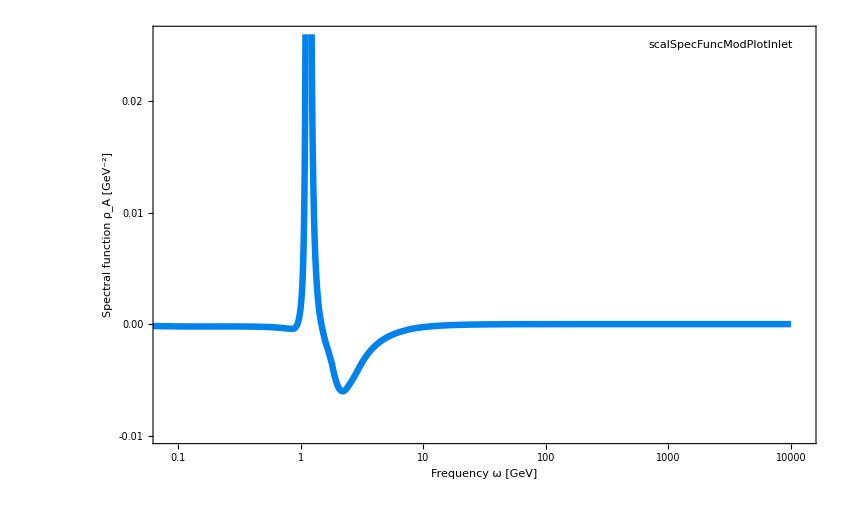

```mathematica
With[{c=4,mA=3.5,Z=3,b=0.1,αs=22/100,i={9},localPlotColors=clearPlotColors},
gluSpecFuncZoom=LogLinearPlot[
c*gluSpecFuncs[[6]]/.{λ->1/.9l},{l,10^-3,10^4},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

FrameLabel->{"Frequency ω [GeV]","Spectral function ρ_A [GeV^-2]"},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],
PlotRange->{xRange={10^-1.1,10^4.1},yRange={c*-.0025,c*.0065}},
Epilog->{Inset[scalSpecFuncModPlotInlet,{Log[xRange⟦2⟧]-.2,yRange⟦2⟧-.0005},{Right,Top},Scaled[0.5]]},
ImagePadding->All

]
]
exportFigure[gluSpecFuncZoom];
```

```mathematica
gluDressSpec=With[{c=4,i=6},Table[{p,p^2*NIntegrate[(*ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[i]]],Interpolation[allScalLong2[[2]][[i]]],1,b]*)gluSpecFuncs[[i]]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-4,4,1/10]}]];
```

```mathematica
gluPropSpec=With[{i=6},Table[{p,NIntegrate[(*ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[i]]],Interpolation[allScalLong2[[2]][[i]]],1,b]*)gluSpecFuncs[[i]]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}]];
```

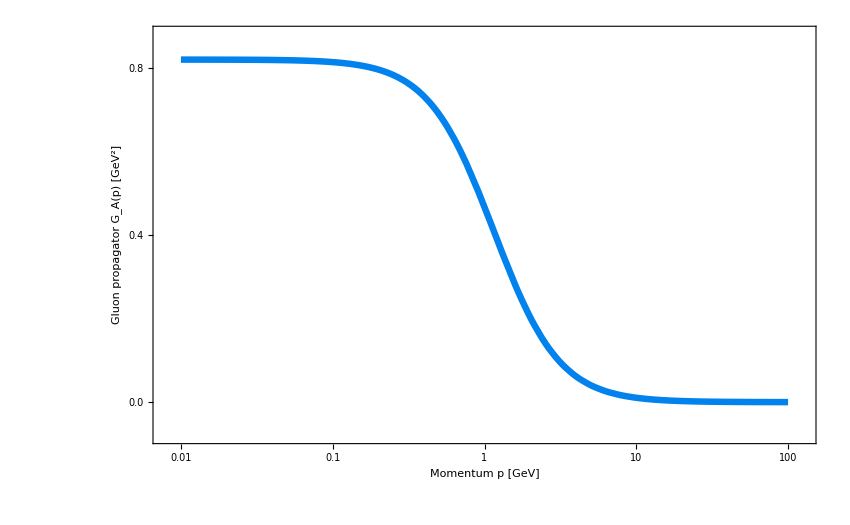

/Users/janhorak/Documents/physics/phd/realtimeFRG/realtime_general/notebooks/spec_funcs/scalarDSE/plots/gluPropSpecPlot.pdf

```mathematica
With[{mA=5,Z=3,b=10^-2,αs=22/100,i=6,localPlotColors=clearPlotColors},
gluPropSpecPlot=Show[
LogLinearPlot[
Interpolation[gluPropSpec][1/.9p]
(*1/(ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]],1,b])*),{p,10^-2,10^2},

PlotRange->{xRange={10^-2.1,10^2.1},yRange={-.08,0.88}},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],


FrameLabel->{"Momentum p [GeV]","Gluon propagator G_A(p) [GeV^2]"}(*,

PlotLegends->{
Placed[SwatchLegend[
{Gray,Black},{"Direct comp","Spec rep"},
LegendMarkers->{legendMarkerLine,Graphics[{EdgeForm[{Black,Thick,Opacity[1]}],FaceForm[Gray],Polygon[CirclePoints[4]]}]},
LegendMarkerSize->{legendSizeLine,legendSizeSquare}
],
{Scaled[{.82,.65}],{.6,0}}]
}*)
],

(*ListLogLinearPlot[gluPropSpec,
Joined->False,
PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[localPlotColors[[1]]],Polygon[CirclePoints[4]]}],0.035}
],*)

ImagePadding->All

]
]
exportFigure[gluPropSpecPlot]
```

```mathematica
<<AwesomeFancyPlots`
```

LinTicks::shdw: Symbol LinTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

LogTicks::shdw: Symbol LogTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

ShowTickLabels::shdw: Symbol ShowTickLabels appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

ShowMinorTicks::shdw: Symbol ShowMinorTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

TickLabelStep::shdw: Symbol TickLabelStep appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

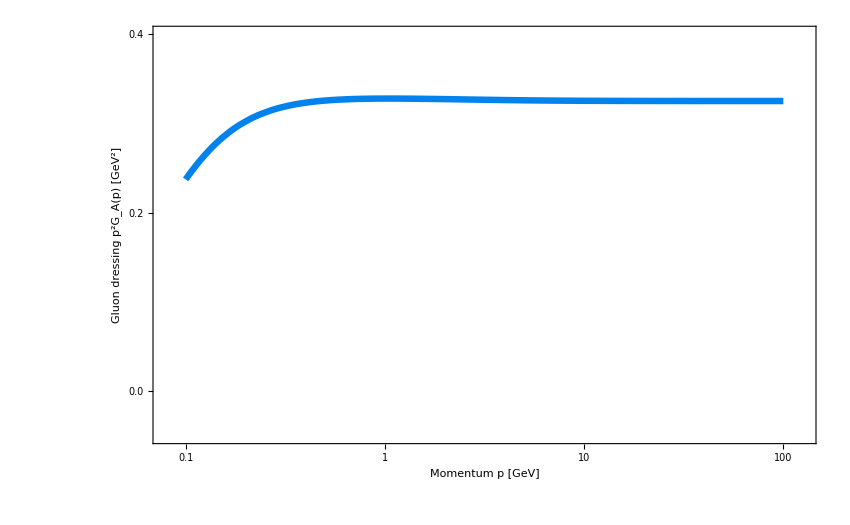

```mathematica
With[{mA=5,Z=3,b=10^-2,αs=22/100,i=6,localPlotColors=clearPlotColors},
gluDressSpecPlot=Show[
LogLinearPlot[
Interpolation[gluDressSpec][20p]
(*1/(ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]],1,b])*),{p,10^-1,10^2},

PlotRange->{xRange={10^-1.1,10^2.1},yRange={-.05,.4}},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],


FrameLabel->{"Momentum p [GeV]","Gluon dressing p^2G_A(p) [GeV^2]"}(*,

PlotLegends->{
Placed[SwatchLegend[
{Gray,Black},{"Direct comp","Spec rep"},
LegendMarkers->{legendMarkerLine,Graphics[{EdgeForm[{Black,Thick,Opacity[1]}],FaceForm[Gray],Polygon[CirclePoints[4]]}]},
LegendMarkerSize->{legendSizeLine,legendSizeSquare}
],
{Scaled[{.82,.65}],{.6,0}}]
}*)
],

(*ListLogLinearPlot[gluPropSpec,
Joined->False,
PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[localPlotColors[[1]]],Polygon[CirclePoints[4]]}],0.035}
],*)

ImagePadding->All

]
]
exportFigure[gluDressSpecPlot];
```

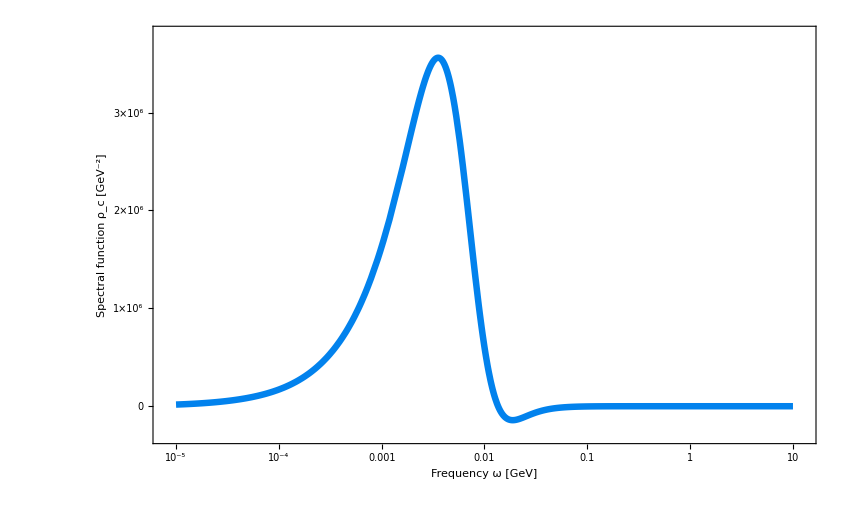

```mathematica
Module[
{ε=10^-2,a=10^-1,localPlotColors=clearPlotColors},

ghostSpecInitPlot=LogLinearPlot[

ρcIntPolScal[1/.9λ(*,ε,a*)],{λ,10^-5,10^1},

PlotRange->{xRange={10^-5.1,10^1.1},yRange={-3*10^5,3.8*10^6}},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False,TickLabelFunction->Evaluate[NumberForm[N[#1],{1,0},NumberPoint->""]&]],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,TickLabelStep->2,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],

FrameLabel->{"Frequency ω [GeV]","Spectral function ρ_c [GeV^-2]"},

ImagePadding->All,

PlotRange->All]]
exportFigure[ghostSpecInitPlot];
```

```mathematica
gluPropAnton=Import["~/Documents/physics/gluon_prop_sca_sym_point.dat"]
```

{{0.00290031,3.6889},{0.00320545,3.72308},{0.00354269,3.76344},{0.00391542,3.81084},{0.00432736,3.86616},{0.00478264,3.93014},{0.00528582,4.00329},{0.00584194,4.0858},{0.00645657,4.17742},{0.00713586,4.27749},{0.00788663,4.38517},{0.00871638,4.49963},{0.00963342,4.62016},{0.010647,4.74625},{0.0117671,4.87752},{0.0130051,5.01371},{0.0143734,5.15464},{0.0158856,5.30024},{0.017557,5.45045},{0.0194041,5.60529},{0.0214456,5.76482},{0.0237019,5.92908},{0.0261956,6.0981},{0.0289516,6.27206},{0.0319976,6.45103},{0.0353641,6.63509},{0.0390847,6.82432},{0.0431968,7.01881},{0.0477416,7.21858},{0.0527644,7.42363},{0.0583158,7.63396},{0.0644512,7.84974},{0.0712321,8.0697},{0.0787264,8.29459},{0.0870092,8.52351},{0.0961634,8.75575},{0.106281,8.99029},{0.117463,9.22581},{0.129821,9.46048},{0.143479,9.69192},{0.158575,9.91707},{0.175258,10.1321},{0.193697,10.3317},{0.214076,10.5105},{0.236599,10.6604},{0.261491,10.7726},{0.289003,10.8364},{0.319409,10.8404},{0.353014,10.7712},{0.390154,10.6152},{0.431202,10.3592},{0.476569,9.99196},{0.526709,9.50506},{0.582124,8.89581},{0.643369,8.16891},{0.711058,7.33902},{0.785868,6.43227},{0.868549,5.4868},{0.959929,4.54942},{1.06092,3.66892},{1.17254,2.88627},{1.29591,2.22642},{1.43225,1.69526},{1.58293,1.28288},{1.74947,0.970352},{1.93354,0.736417},{2.13696,0.561837},{2.36179,0.431153},{2.61028,0.332736},{2.8849,0.2581},{3.18842,0.201113},{3.52388,0.157329},{3.89462,0.123503},{4.30438,0.0972428},{4.75724,0.0767687},{5.25775,0.0607468},{5.81092,0.0481679},{6.42228,0.0382639},{7.09797,0.0304462},{7.84474,0.0242615},{8.67009,0.019359},{9.58227,0.0154658},{10.5904,0.0123693},{11.7046,0.00990289},{12.9361,0.00793574},{14.2971,0.00636493},{15.8013,0.00510925},{17.4637,0.00410447},{19.3011,0.00329974},{21.3317,0.00265467},{23.576,0.00213718},{26.0565,0.00172173},{28.7979,0.00138799},{31.8277,0.00111969},{35.1763,0.000903889},{38.8772,0.000730203},{42.9674,0.000590336},{47.488,0.00047764},{52.4842,0.000386787},{58.0061,0.000313502}}

```mathematica
gluPropScal=Table[{p,NIntegrate[λ/π*ρAIterScal[λ,1,0,Interpolation[allScalLong[[1]][[9]]],Interpolation[allScalLong[[2]][[9]]],1,1]/(p^2+λ^2),{λ,10^-3,10^2}]},{p,10^Range[-3,2,1/10]}];
```

InterpolatingFunction::dmval: Input value {1/10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.0570247}. NIntegrate obtained 0.450067 and 0.470551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.0570247}. NIntegrate obtained 0.449982 and 0.470466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.0570247}. NIntegrate obtained 0.449847 and 0.470332 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

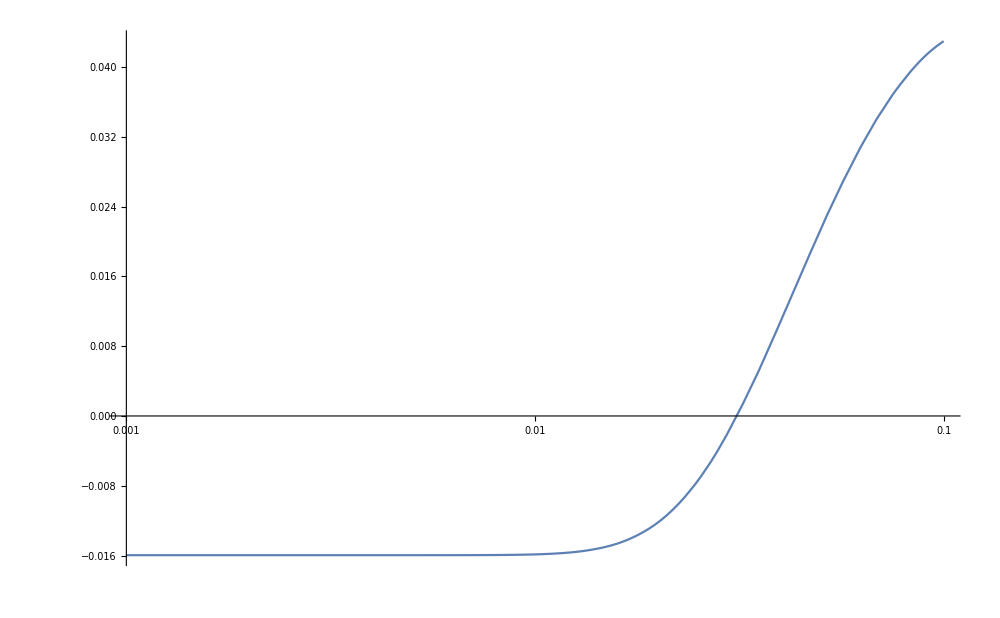

```mathematica
With[{mA=0,i=1},LogLinearPlot[{Im[ΓA2IterScal[λ,1,mA,Interpolation[gluPolIters[[i]]],Interpolation[ghostPolIters[[i]]],1,1]]},{λ,10^-3,10^-1},(*PlotRange->All,*)ImageSize->1000]]
```

Gluon propagator dressing

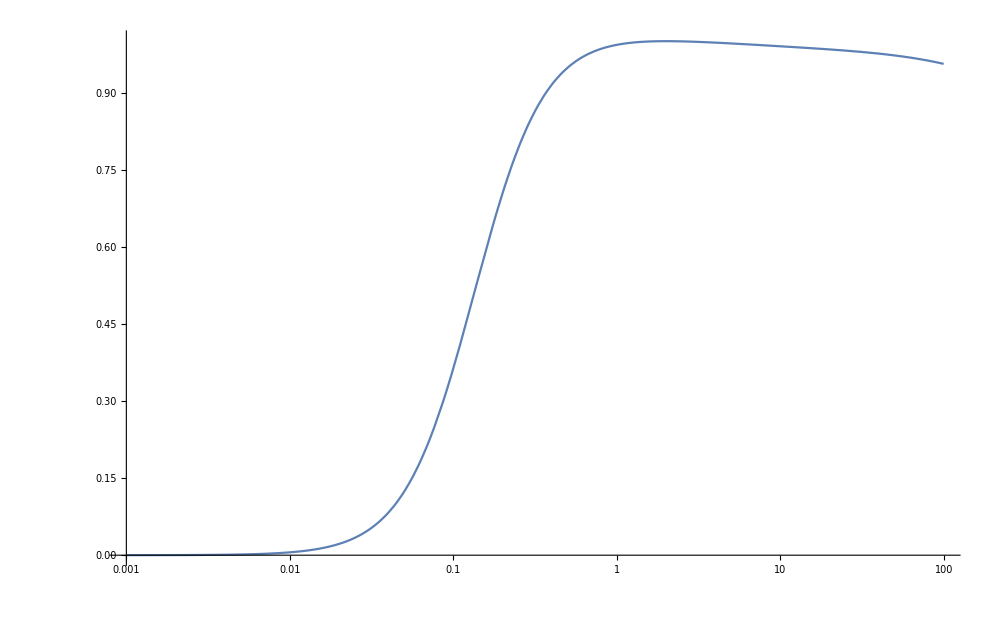

```mathematica
With[{mA=0,i=1},LogLinearPlot[λ^2/(ΓA2IterE[λ,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]]]),{λ,10^-3,10^2},(*PlotRange->All,*)ImageSize->1000]]
```

```mathematica
invPropTbl=With[{mA=5,Z=3,b=0.01,αs=22/100,i=5},Table[{p,1/(ΓA2IterEScal[p,Z,mA,Interpolation[allScalLong2[[3]][[i]]],Interpolation[allScalLong2[[4]][[i]]],1,b])},{p,10^Range[-3,2,1/10]}]];
```

InterpolatingFunction::dmval: Input value {1/10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
specPropTbl=With[{mA=5,Z=3,b=0.01,αs=22/100,i=5},Table[{p,NIntegrate[ρAIterScal[λ,Z,mA,Interpolation[allScalLong2[[1]][[i]]],Interpolation[allScalLong2[[2]][[i]]],1,b]*λ/π/(p^2+λ^2),{λ,10^-3,10^2},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}]];
```

InterpolatingFunction::dmval: Input value {1/10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Check if Euclidean propagators coincide

```mathematica
Length[gluSpecFuncs]
```

6

```mathematica
discr
```

{{1/1000,2.04866×10^-7},{1/(100 10^(9/10)),3.24691×10^-7},{1/(100 10^(4/5)),5.146×10^-7},{1/(100 10^(7/10)),8.15586×10^-7},{1/(100 10^(3/5)),1.29261×10^-6},{1/(100 √10),2.04865×10^-6},{1/(100 10^(2/5)),3.24688×10^-6},{1/(100 10^(3/10)),5.14594×10^-6},{1/(100 10^(1/5)),8.15569×10^-6},{1/(100 10^(1/10)),0.0000129257},{1/100,0.0000204854},{1/(10 10^(9/10)),0.0000324661},{1/(10 10^(4/5)),0.0000514526},{1/(10 10^(7/10)),0.0000815398},{1/(10 10^(3/5)),0.000129214},{1/(10 √10),0.000204745},{1/(10 10^(2/5)),0.000324386},{1/(10 10^(3/10)),0.000513831},{1/(10 10^(1/5)),0.000813645},{1/(10 10^(1/10)),0.00128772},{1/10,0.00203635},{1/10^(9/10),0.003216},{1/10^(4/5),0.00506861},{1/10^(7/10),0.00796278},{1/10^(3/5),0.0124471},{1/(√10),0.0193076},{1/10^(2/5),0.0296018},{1/10^(3/10),0.0446079},{1/10^(1/5),0.0655845},{1/10^(1/10),0.0932499},{1,0.127064},{10^(1/10),0.164744},{10^(1/5),0.202632},{10^(3/10),0.236967},{10^(2/5),0.265244},{√10,0.286714},{10^(3/5),0.301989},{10^(7/10),0.312312},{10^(4/5),0.319002},{10^(9/10),0.323168},{10,0.325644},{10 10^(1/10),0.327017},{10 10^(1/5),0.327682},{10 10^(3/10),0.327899},{10 10^(2/5),0.32784},{10 √10,0.327616},{10 10^(3/5),0.3273},{10 10^(7/10),0.326946},{10 10^(4/5),0.32659},{10 10^(9/10),0.32626},{100,0.325974}}

```mathematica
gluDressSpec[1]
```

0.127064

```mathematica
FindMaximum[gluDressSpec[x],x]
```

{0.327911,{x→21.2884}}

```mathematica
Max[discr[[All,2]]]
```

0.327906

```mathematica
bumpScal=10 10^(8/25);
```

```mathematica
bumpScal//N
```

20.893

```mathematica
gluDressScal=discr;
```

```mathematica
Max[gluPropSpec[[All,2]]]
```

0.204866

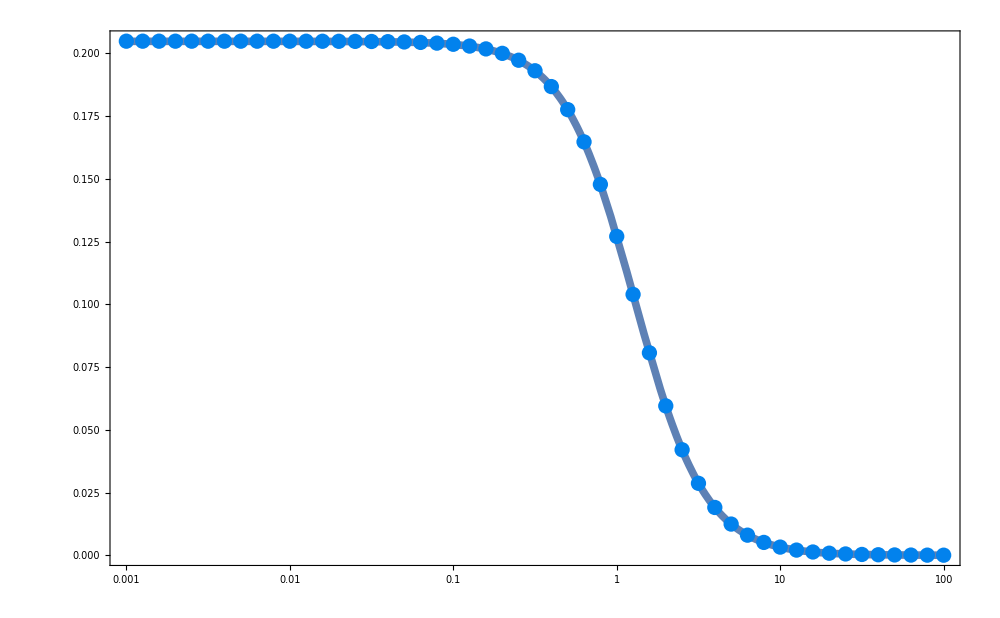

```mathematica
With[{mA=5,Z=3,b=0.01,αs=22/100,i=6,c=4},

Show[LogLinearPlot[(*.9/(p^2+1/1.5)+*)1/(ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]],1,b]),{p,10^-3,10^2},PlotRange->All],ListLogLinearPlot[gluPropSpec,AxesLabel->{p,"G(p)"},PlotRange->All,Joined->False,PlotStyle->{clearPlotColors[[1]]}],ImageSize->1000]
]
```

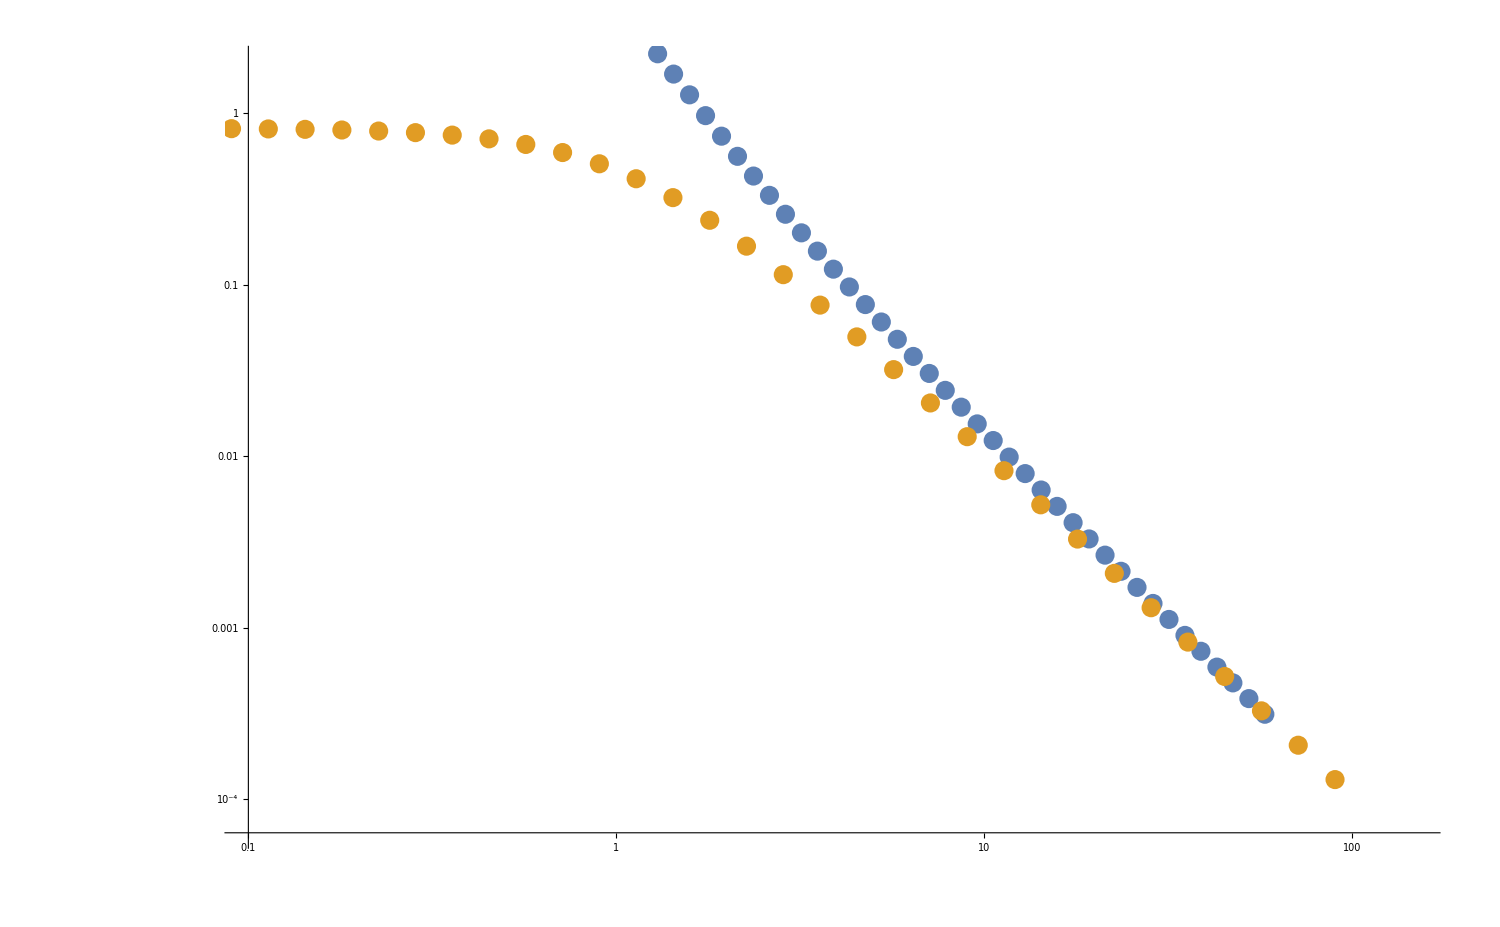

```mathematica
propComparisonPlot=With[{a=.9,c=1},ListLogLogPlot[{gluPropAnton,Table[{a*gluPropSpec[[i,1]],c*gluPropSpec[[i,2]]},{i,Length[gluPropSpec]}]},PlotRange->{{.10,150},{-.02,2}},ImageSize->1500]]
```

```mathematica
Show[propComparisonPlot,ImageSize->Tiny]
```

```mathematica
exportFigure[propComparisonPlot];
```

```mathematica
gluDressAnton
```

{{0.00290031,0.0000310301},{0.00320545,0.0000382542},{0.00354269,0.0000472336},{0.00391542,0.0000584221},{0.00432736,0.0000723978},{0.00478264,0.0000898964},{0.00528582,0.000111851},{0.00584194,0.000139441},{0.00645657,0.000174145},{0.00713586,0.000217812},{0.00788663,0.000272753},{0.00871638,0.00034186},{0.00963342,0.000428764},{0.010647,0.000538024},{0.0117671,0.000675367},{0.0130051,0.000847986},{0.0143734,0.00106492},{0.0158856,0.00133753},{0.017557,0.00168008},{0.0194041,0.0021105},{0.0214456,0.00265132},{0.0237019,0.00333084},{0.0261956,0.00418457},{0.0289516,0.00525722},{0.0319976,0.00660488},{0.0353641,0.00829797},{0.0390847,0.010425},{0.0431968,0.0130969},{0.0477416,0.016453},{0.0527644,0.020668},{0.0583158,0.0259611},{0.0644512,0.0326075},{0.0712321,0.0409457},{0.0787264,0.0514086},{0.0870092,0.0645281},{0.0961634,0.0809679},{0.106281,0.101551},{0.117463,0.127293},{0.129821,0.159441},{0.143479,0.19952},{0.158575,0.249374},{0.175258,0.311211},{0.193697,0.387631},{0.214076,0.481681},{0.236599,0.596758},{0.261491,0.736605},{0.289003,0.905083},{0.319409,1.10596},{0.353014,1.34229},{0.390154,1.61584},{0.431202,1.92614},{0.476569,2.26935},{0.526709,2.63691},{0.582124,3.01451},{0.643369,3.38131},{0.711058,3.71063},{0.785868,3.9725},{0.868549,4.13912},{0.959929,4.19212},{1.06092,4.12958},{1.17254,3.96821},{1.29591,3.73899},{1.43225,3.47755},{1.58293,3.21449},{1.74947,2.96992},{1.93354,2.75314},{2.13696,2.56569},{2.36179,2.405},{2.61028,2.26711},{2.8849,2.14808},{3.18842,2.04453},{3.52388,1.95367},{3.89462,1.87331},{4.30438,1.80168},{4.75724,1.73738},{5.25775,1.67928},{5.81092,1.62647},{6.42228,1.57822},{7.09797,1.53391},{7.84474,1.49305},{8.67009,1.45522},{9.58227,1.42007},{10.5904,1.38731},{11.7046,1.35668},{12.9361,1.32798},{14.2971,1.30103},{15.8013,1.27568},{17.4637,1.25179},{19.3011,1.22926},{21.3317,1.20799},{23.576,1.18791},{26.0565,1.16895},{28.7979,1.15108},{31.8277,1.13425},{35.1763,1.11845},{38.8772,1.10365},{42.9674,1.08988},{47.488,1.07713},{52.4842,1.06544},{58.0061,1.05484}}

```mathematica
bumpAnton=.96;
```

```mathematica
gluDressAnton=Table[{gluPropAnton[[i,1]],gluPropAnton[[i,2]]*gluPropAnton[[i,1]]^2},{i,Length[gluPropAnton]}];
```

```mathematica
relDif
```

{0.0039625,0.0039625,0.0039625,0.0039625,0.00396249,0.00396248,0.00396247,0.00396245,0.00396242,0.00396237,0.00396229,0.00396217,0.00396197,0.00396166,0.00396116,0.00396036,0.00395908,0.00395706,0.00395384,0.00394874,0.00394066,0.00392789,0.00390782,0.00387643,0.00382775,0.00375323,0.00364138,0.00347827,0.0032502,0.00294927,0.00258128,0.00217099,0.00175828,0.00138447,0.00107765,0.000847206,0.000688044,0.000588509,0.000536546,0.000520547,0.000505155,0.000537376,0.000597861,0.000689562,0.000904756,0.000574379,0.000760223,0.00104074,0.00144834,0.00221905,0.00299678}

```mathematica
With[{g=10^-0,mA=0,i=0,c=4},
ghostPropEucl = Table[{p,c(*ghostPoleResidues[[i]]/p^2+*)NIntegrate[ρcIntPolScal[λ]*λ/π/(p^2+λ^2),{λ,10^-5,10^3},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}];
ghostDress= Table[{p,c*(*ghostPoleResidues[[i]]+*)p^2*NIntegrate[ρcIntPolScal[λ]*λ/π/(p^2+λ^2),{λ,10^-5,10^3},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}]
];
```

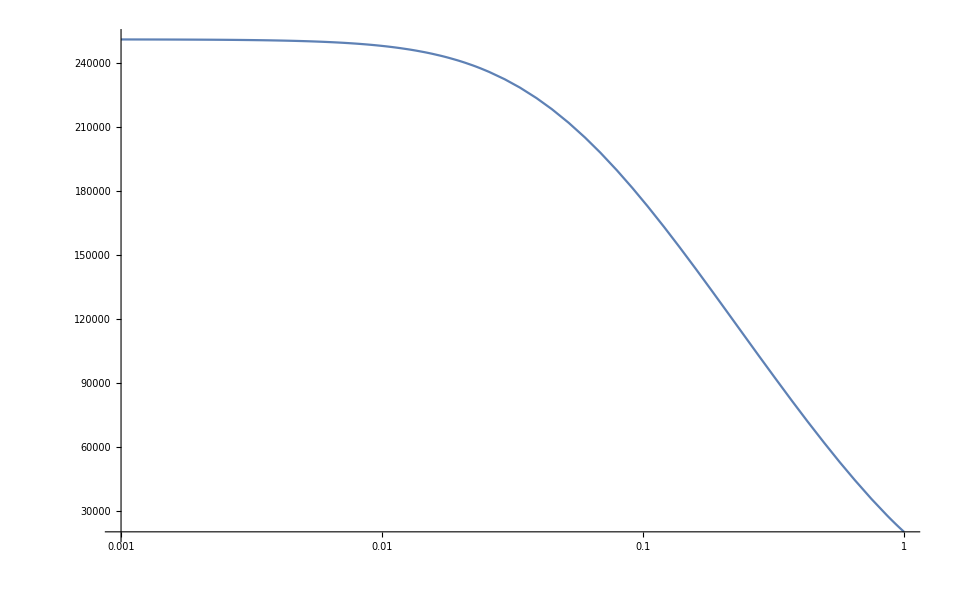

```mathematica
With[{mAsq=0,i=1},LogLinearPlot[{(*(p^2)^(1-2κ),*)-Interpolation[gluPolItersE[[i]]][p]-10^5Interpolation[ghostPolItersE[[i]]][p]},{p,10^-3,10^0},PlotRange->All]]
```

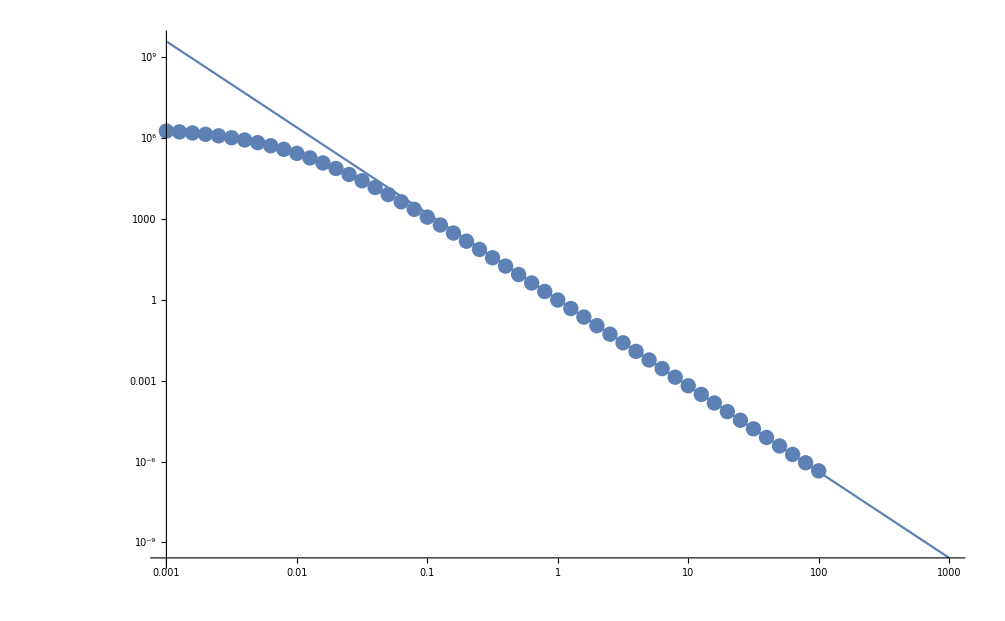

```mathematica
Show[With[{mA=1/Sqrt[5],a=10^0,ε=10^-2,αs=22/100,i=3},LogLogPlot[(*Re[1/Γc2ScalE[-I(w+I*ε),a]]*)1/w^(2+2κ),{w,10^-3,10^3},PlotRange->All]],ListLogLogPlot[ghostPropEucl,AxesLabel->{p,"G(p)"},PlotRange->All]]
```

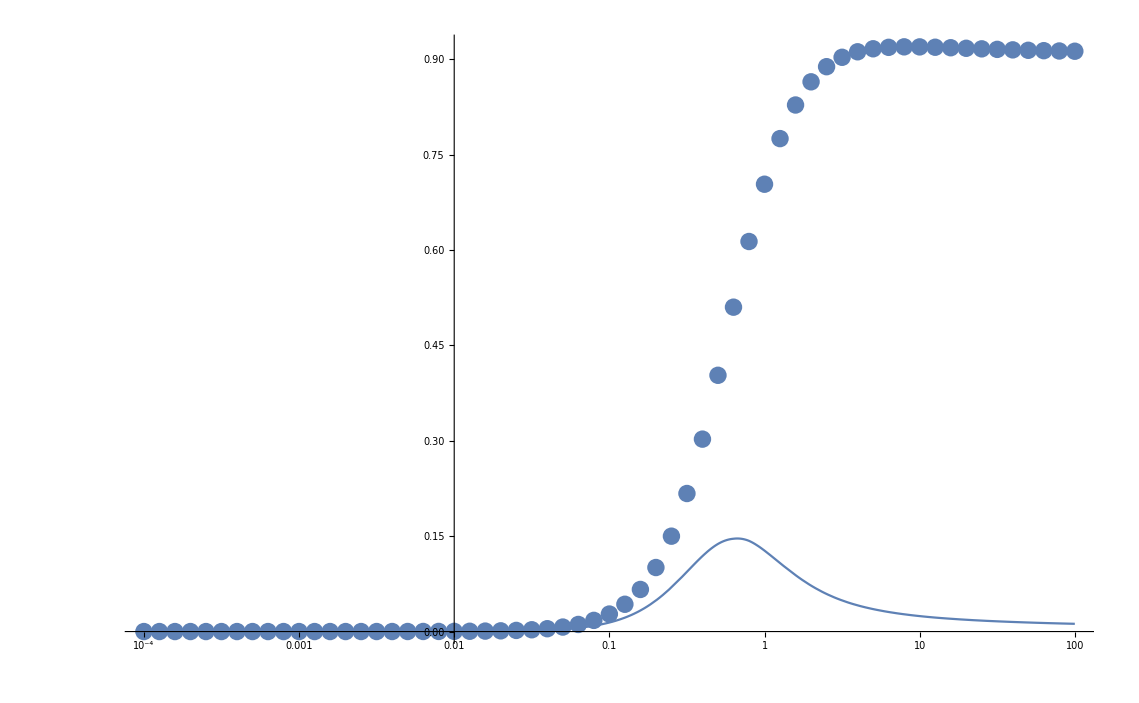

```mathematica
With[{i=1,mA=1/1.5,Z=20},Show[LogLinearPlot[(*p^2(.9/(p^2+1/1.5))+*)p^2/ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[10^-1*ghostPolItersE[[i]]]],{p,10^-2,10^2},PlotRange->All],ListLogLinearPlot[gluPropEuclDress,AxesLabel->{p,"p^2*G(p)"},PlotRange->All]]]
```

Ghost dressing

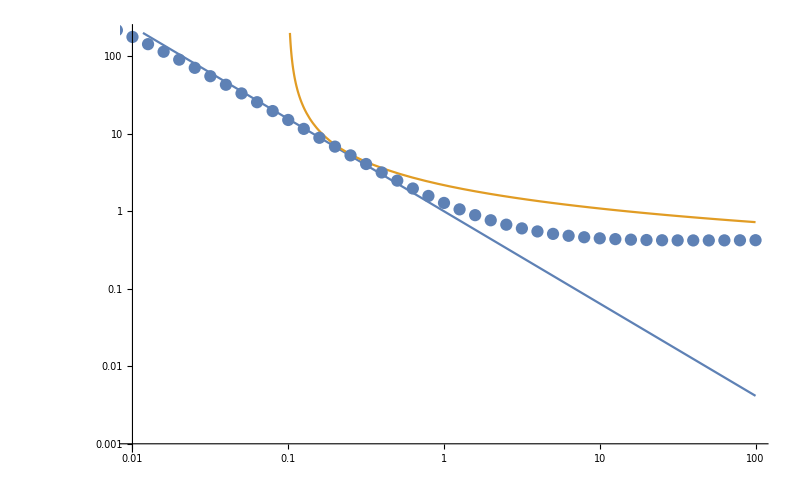

```mathematica
With[{i=3,λmin=10^-2,λmax=10^2},Show[LogLogPlot[(*p^2/Γc2IterE[p,Interpolation[ghostGluLoopItersE[[i]]]]*){p^(-2κ),10/Log[100p^2]},{p,λmin,λmax},PlotRange->{{λmin,λmax},{.001,200}}],ListLogLogPlot[ghostDress,AxesLabel->{p,"p^2 G(p)"},PlotRange->{{λmin,λmax},All}],ImageSize->800]]
```

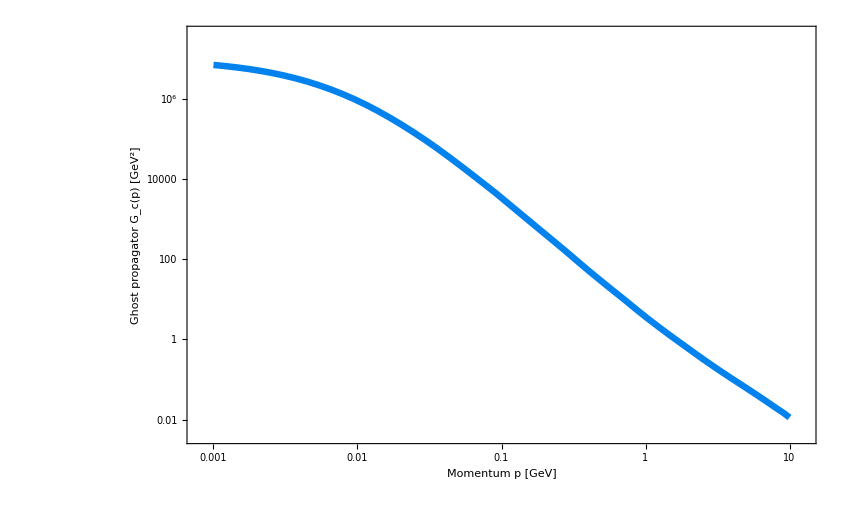

/Users/janhorak/Documents/physics/phd/realtimeFRG/realtime_general/notebooks/spec_funcs/scalarDSE/plots/ghostPropSpecPlot.pdf

```mathematica
With[{mA=5,Z=3,b=10^-2,αs=22/100,i=6,c=4,localPlotColors=clearPlotColors},
ghostPropSpecPlot=Show[
LogLogPlot[
{Interpolation[ghostPropEucl][1/.9p](*,p^(-2κ-2)*)}
(*1/(ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]],1,b])*),{p,10^-3,10^1},

PlotRange->{xRange={10^-3.1,10^1.1},yRange=c*{10^-3,10^7}},
FrameTicks->{{LogTicks[Sequence@@yRange,ShowMinorTicks->False(*,TickLabelStep->2*),LogPlot->True],LogTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False,LogPlot->True]},{LogTicks[Sequence@@xRange,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],


FrameLabel->{"Momentum p [GeV]","Ghost propagator G_c(p) [GeV^2]"}(*,

PlotLegends->{
Placed[SwatchLegend[
{Gray,Black},{"Direct comp","Spec rep"},
LegendMarkers->{legendMarkerLine,Graphics[{EdgeForm[{Black,Thick,Opacity[1]}],FaceForm[Gray],Polygon[CirclePoints[4]]}]},
LegendMarkerSize->{legendSizeLine,legendSizeSquare}
],
{Scaled[{.82,.65}],{.6,0}}]
}*)
],

(*ListLogLinearPlot[gluPropSpec,
Joined->False,
PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[localPlotColors[[1]]],Polygon[CirclePoints[4]]}],0.035}
],*)

ImagePadding->All

]
]
exportFigure[ghostPropSpecPlot]
```

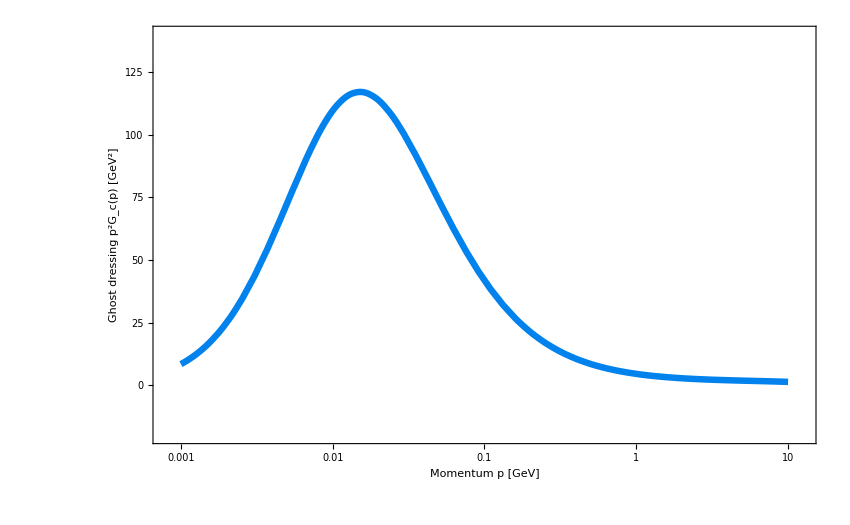

/Users/janhorak/Documents/physics/phd/realtimeFRG/realtime_general/notebooks/spec_funcs/scalarDSE/plots/ghostDressSpecPlot.pdf

```mathematica
With[{mA=5,Z=3,b=10^-2,αs=22/100,i=6,c=4,localPlotColors=clearPlotColors},
ghostDressSpecPlot=Show[
LogLinearPlot[
{Interpolation[ghostDress][1/.9p](*,p^(-2κ-2)*)}
(*1/(ΓA2IterEScal[p,Z,mA,Interpolation[gluPolItersE[[i]]],Interpolation[ghostPolItersE[[i]]],1,b])*),{p,10^-3,10^1},

PlotRange->{xRange={10^-3.1,10^1.1},yRange=c*{-5,35}},
FrameTicks->{{LinTicks[Sequence@@yRange,ShowMinorTicks->False(*,TickLabelStep->2*)(*,LogPlot->True*)],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False(*,LogPlot->True*)]},{LogTicks[Sequence@@xRange,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,LogPlot->True]}},

PlotStyle->Directive[localPlotColors[[1]],defaultLineThickness],


FrameLabel->{"Momentum p [GeV]","Ghost dressing p^2G_c(p) [GeV^2]"}(*,

PlotLegends->{
Placed[SwatchLegend[
{Gray,Black},{"Direct comp","Spec rep"},
LegendMarkers->{legendMarkerLine,Graphics[{EdgeForm[{Black,Thick,Opacity[1]}],FaceForm[Gray],Polygon[CirclePoints[4]]}]},
LegendMarkerSize->{legendSizeLine,legendSizeSquare}
],
{Scaled[{.82,.65}],{.6,0}}]
}*)
],

(*ListLogLinearPlot[gluPropSpec,
Joined->False,
PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[localPlotColors[[1]]],Polygon[CirclePoints[4]]}],0.035}
],*)

ImagePadding->All

]
]
exportFigure[ghostDressSpecPlot]
```

```mathematica
With[{g=10^-0,mA=0,i=0},
(*ghostPropEucl = Table[{p,(*ghostPoleResidues[[i]]/p^2+*)NIntegrate[ρcIntPolScal[λ]*λ/π/(p^2+λ^2),{λ,10^-5,10^3},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}];*)
ghostDressTest= Table[{p,(*ghostPoleResidues[[i]]+*)p^2*NIntegrate[2Im[1/(λ^2(Log[1-100λ^2]^2))]*λ/π/(p^2+λ^2),{λ,10^-1,10^3},PrecisionGoal->3]},{p,10^Range[-3,2,1/10]}]
];
```

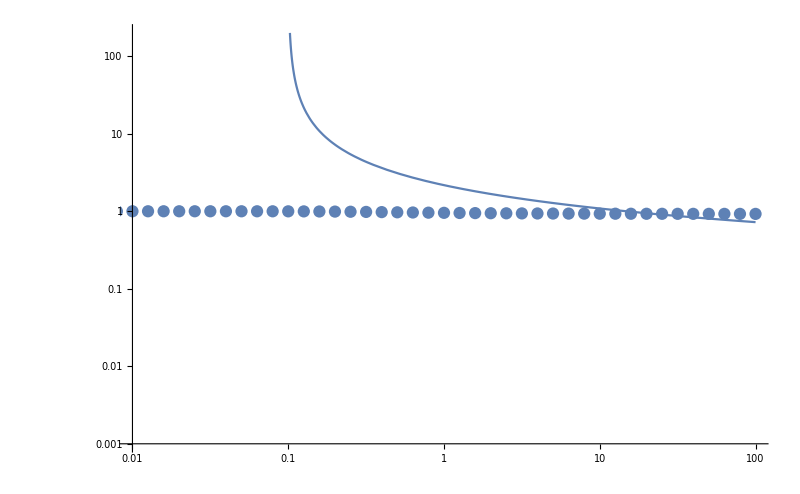

```mathematica
With[{i=3,λmin=10^-2,λmax=10^2},Show[LogLogPlot[(*p^2/Γc2IterE[p,Interpolation[ghostGluLoopItersE[[i]]]]*){(*p^(-2κ),*)10/Log[100p^2]},{p,λmin,λmax},PlotRange->{{λmin,λmax},{.001,200}}],ListLogLinearPlot[ghostDressTest,AxesLabel->{p,"p^2 G(p)"},PlotRange->{{λmin,λmax},All}],ImageSize->800]]
```

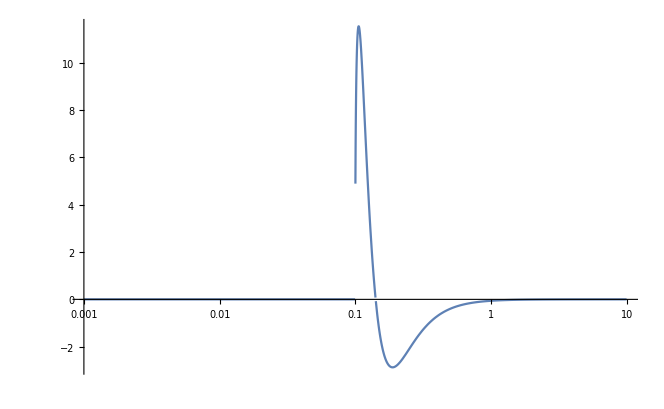

```mathematica
LogLinearPlot[{2Im[1/(λ^2Log[1-100λ^2]^2)](*,1/(λ^2Log[1λ^2])*)},{λ,10^-3,10},PlotRange->All]
```

#### Ghost Spectral function iteration

```mathematica
ghostGluLoopItersSep={};
ghostGluLoopItersSepE={};
DghostGluLoopp0ItersSepE={};
ghostPoleResiduesSep={};
```

```mathematica
Do[
With[{mA=101/100*10^-4,αs=220/100,λAmin=10^-4,λAmax=10,λcmin=10^-4,λcmax=100,μ=2,momRange=10^Range[-3,1,1/10]},

specFuncATmp=ρAIntPolBW;

If[i==1,

(*Use interpolated analytic spectral function in first iteration*)
specFunccTmp=ρcIntPolBW;
ghostPoleResTmp=1/(1+4π*αs*DghostGluLoopp0IntPolE[mA,10^-5]/48*10^8);,

(*Interpolate grid points of gluon polarization diagram*)
ghostGluLoopIterTmp=Interpolation[ghostGluLoopItersSep[[i-1]]];

(*Discretize and interpolate spectral function*)
specFunccDiscrTmp=Table[{λ,N[ρcIter[λ,ghostGluLoopIterTmp],30]},{λ,Join[{0},wRangeGhostGlu]}];
specFunccTmp=Interpolation[specFunccDiscrTmp];
ghostPoleResTmp=ghostPoleResiduesSep[[i-1]];

];

(*Compute iterated gluon polarization diagram employing the updated spectral function*)
iterT=AbsoluteTiming[

(*GHOST SELF ENERGY*)

(*Minkowski*)
AppendTo[
ghostGluLoopItersSep,Table[
{w,ghostPoleResTmp*NIntegrate[ghostGluLoopRegIntPolPole[w,αs,λ1,specFuncATmp],{λ1,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[ghostGluLoopRegIntPol[w,αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,λAmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{w,momRange}
]
];

(*Euclidean*)
AppendTo[
ghostGluLoopItersSepE,Table[
{p,ghostPoleResTmp*NIntegrate[ghostGluLoopRegIntPolPoleE[p,αs,λ1,specFuncATmp],{λ1,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[ghostGluLoopRegIntPolE[p,αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,λAmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{p,momRange}
]
];

(*Extract residue of ghost spectral function*)
AppendTo[
DghostGluLoopp0ItersSepE,
ghostPoleResTmp*NIntegrate[DghostGluLoopp0RegIntPolPoleE[αs,λ1,specFuncATmp],{λ1,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]+NIntegrate[DghostGluLoopp0RegIntPolE[αs,λ1,λ2,specFuncATmp,specFunccTmp],{λ1,λAmin,λAmax},{λ2,λcmin,λcmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]
];

AppendTo[
ghostPoleResiduesSep,1/DΓc2p0IterE[DghostGluLoopp0ItersSepE[[i]]]
];
][[1]];

(*Print iteration time*)
Print[StringForm["Iteration `` complete. (tIter = ``)",i,iterT]];

(*Clean up*)
Clear[ghostGluLoopIterTmp,specFunccDiscrTmp,specFunccTmp,ghostPoleResTmp,iterT];
]
, {i,1,3}
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ1 near {λ1} = {0.0124438}. NIntegrate obtained -7.4667×10^-7-6.75225×10^-10 ⅈ and 1.4531×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ1 near {λ1} = {0.0124438}. NIntegrate obtained -1.18445×10^-6-1.6961×10^-9 ⅈ and 2.30507×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ1 near {λ1} = {0.0124438}. NIntegrate obtained -1.87965×10^-6-4.26044×10^-9 ⅈ and 3.65801×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Iteration 1 complete. (tIter = 348.929)

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/(10000 10^(9/10))} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Iteration 2 complete. (tIter = 677.491)

Iteration 3 complete. (tIter = 743.642)

```mathematica
ghostProp=Table[{p,ghostPoleRes0/p^2+NIntegrate[λ/Pi*ρc0BW[λ]/(p^2+λ^2),{λ,10^-3,10}]},{p,10^Range[-3,1,1/10]}];
```

Check if Euclidean ghost propagators coincide

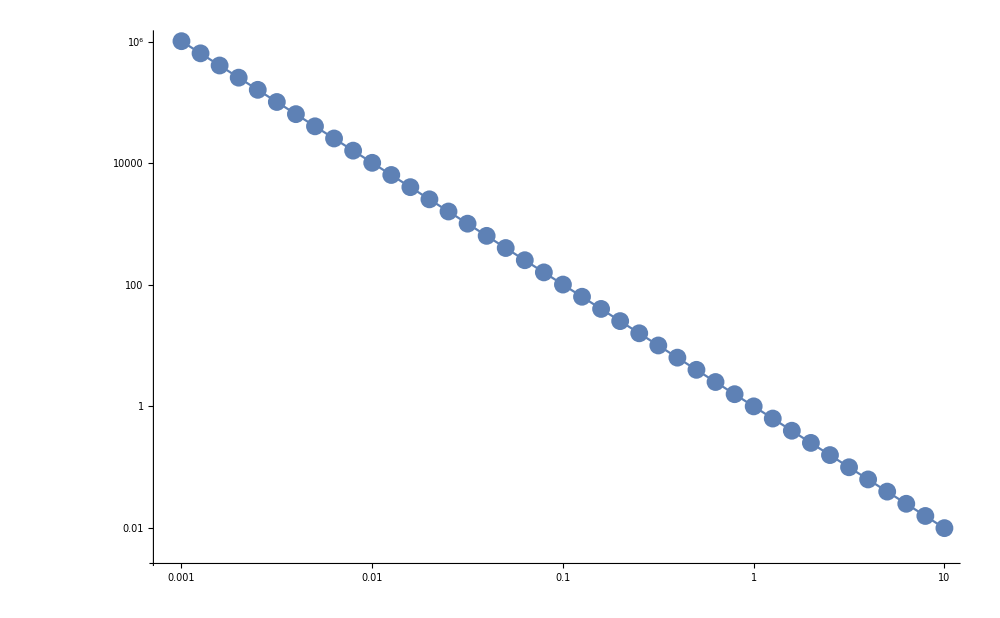

```mathematica
Show[ListLogLogPlot[ghostProp],LogLogPlot[1/(p^2-Interpolation[ghostGluLoopItersSepE[[5]]][p]/24),{p,10^-3,10}],ImageSize->1000]
```

```mathematica
ghostSpecFuncStandalone
```

2 Im[1/(-λ^2-1/24 InterpolatingFunction[…][λ])]

```mathematica
ghostSpecFuncStandalone=ρcIter[λ,Interpolation[ghostGluLoopItersSep[[3]]]];
```

```mathematica
ghostPoleRes0=Re[1/DΓc2p0IterE[DghostGluLoopp0ItersSepE[[5]]]]
```

1.01784

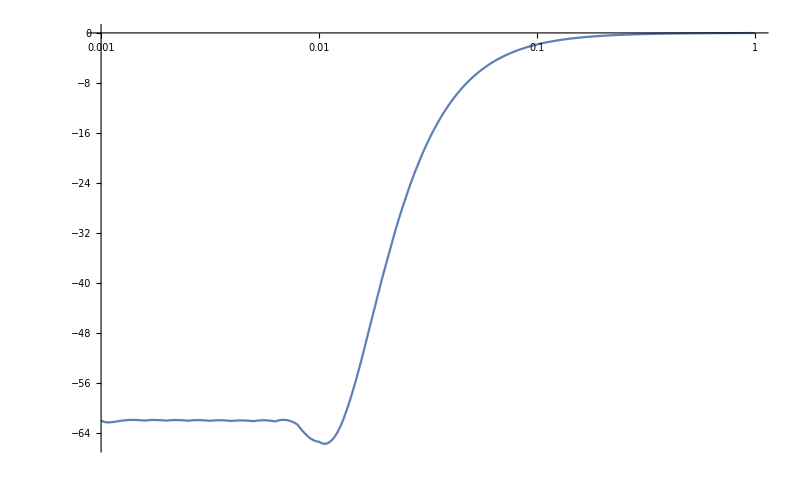

```mathematica
With[{i=3},LogLinearPlot[ρcIter[λ,Interpolation[ghostGluLoopItersSep[[i]]]],{λ,10^-3,10^0},ImageSize->800]]
```

```mathematica
(*DumpSave["realtime_gluon_spectral_function_data.mx",{
(*SPECTRAL FUNCTIONS*)
gluSpecFuncs,ghostSpecFuncs,ghostSpecFuncStandalone,
(*GLUON INTERPOLATING FUNCTIONS*)
gluPolIntPol,gluPolIntPolE,DgluPolμ0IntPolE,DgluPolμ2IntPolE,(*gluPolTbl,DgluPolμ2TblE,gluPolμ2TblE,gluPolTblE,*)
(*GHOST LOOP INTERPOLATING FUNCTIONS*)
ghostPolIntPol,ghostPolIntPolE,DghostPolμ0IntPolE,DghostPolμ2IntPolE,(*ghostPolTbl,ghostPolTblE,ghostPolTblESubtr1,ghostPolTblμ2E,DghostPolTblμ2E,*)
(*GHOST GLUON LOOP INTERPOLATING FUNCTIONS*)
ghostGluLoopIntPol,ghostGluLoopIntPolE,DghostGluLoopμ2IntPolE,DghostGluLoopp0IntPolE(*ghostGluLoopTbl,ghostGluLoopTblE,DghostGluLoopp0TblE,DghostGluLoopTblμ2E,*),
(*RESULTS*)
allBWmA0,allBWmAn0p4,allscal}];*)
```